## Backtesting Report

#### Saturday 19 November 2016

```mathematica
Style[Row[{"Stock: ",{"SAN.MC","ParabolicStopAndReversal",{0.005,0.5},{2007,1,2},{2016,10,21}}[[1]]," between ",DateString[{"SAN.MC","ParabolicStopAndReversal",{0.005,0.5},{2007,1,2},{2016,10,21}}[[4]],"Date"]," and ",DateString[{"SAN.MC","ParabolicStopAndReversal",{0.005,0.5},{2007,1,2},{2016,10,21}}[[5]],"Date"]}],"Subsection"]
```

Stock: SAN.MC between Tuesday 2 January 2007 and Friday 21 October 2016

```mathematica
Style[Row[{"Strategy: ",{"SAN.MC","ParabolicStopAndReversal",{0.005,0.5},{2007,1,2},{2016,10,21}}[[2]]," parameters ",ToString[{"SAN.MC","ParabolicStopAndReversal",{0.005,0.5},{2007,1,2},{2016,10,21}}[[3]]]}],"Subsubsection"]
```

Strategy: ParabolicStopAndReversal parameters {0.005, 0.5}

```mathematica
TabView[{"Overall Performance"-> 
Column[{
Grid[
Transpose[{{{{"Net Profit","2051.35""(""41.03""%)"},{"Gross Profit","11074.54""(""221.49""%)"},{"Gross Loss","9023.18""(""180.46""%)"},{"Maximum Drawdown","2373.90""(""34.27""%)"},{"Profit Factor","1.23"},{"Recovery Factor","0.86"}},{{"Annual Average Return","3.59""%"},{"Days in Market","50.93""%"},{"Risc Adjusted Return","7.04""%"},{"Mar Ratio","0.10"},{"Total commissions","0.00"},{"Commission Index","0.00"}},{{"Buy & Hold Profit","-1661.54""(""-33.23""%)"},{"Annual Average BH Return","-4.06""%"},{"Buy & Hold Index","1.88"}}},{{{"Number of Trades",50},{"Winning Trades",20"(""40.00""%)"},{"Lossing Trades",30"(""60.00""%)"},{"Average Trades/Year","5.13"},{"Sharpe Ratio of Trades","0.11"}},{{"Average Trade","41.03""(""0.69""%)"},{"Average Profit Trade",553.7268262662727"(""10.26""%)"},{"Largest Profit Trade Return","37.80""%"},{"Average Loss Trade",300.77276828075543"(""5.22""%)"},{"Largest Loss Trade Return","17.29""%"},{"Payoff Ratio","1.84"}},{{"Average Days Trade","36.26"},{"Average Days Profit Trade","56.30"},{"Average Days Loss Trade","22.90"},{"Average Eficiency","-15.61""%"}},{{"Average MFE","9.01""%"},{"Average Profit MFE","17.07""%"},{"Average Loss MFE","3.64""%"},{"Average MAE","-5.85""%"},{"Average Profit MAE","-3.77""%"},{"Average Loss MAE","-7.24""%"}}},{{{"Net profit","-1965.39""(""-39.31""%)"},{"Maximum Drawdown","2398.09""(""46.34""%)"},{"Profit Factor","0.76"},{"Recovery Factor","-0.82"},{"Average Trade","-39.31""(""-0.99""%)"},{"Winning Trades",17."(""34.00""%)"},{"Payoff Ratio","1.47"},{"Average Eficiency","-30.06""%"}}}}[[1,1]]],
Background->Lighter[Gray, 0.9],
Frame->All],
Grid[
Transpose[{{{{"Net Profit","2051.35""(""41.03""%)"},{"Gross Profit","11074.54""(""221.49""%)"},{"Gross Loss","9023.18""(""180.46""%)"},{"Maximum Drawdown","2373.90""(""34.27""%)"},{"Profit Factor","1.23"},{"Recovery Factor","0.86"}},{{"Annual Average Return","3.59""%"},{"Days in Market","50.93""%"},{"Risc Adjusted Return","7.04""%"},{"Mar Ratio","0.10"},{"Total commissions","0.00"},{"Commission Index","0.00"}},{{"Buy & Hold Profit","-1661.54""(""-33.23""%)"},{"Annual Average BH Return","-4.06""%"},{"Buy & Hold Index","1.88"}}},{{{"Number of Trades",50},{"Winning Trades",20"(""40.00""%)"},{"Lossing Trades",30"(""60.00""%)"},{"Average Trades/Year","5.13"},{"Sharpe Ratio of Trades","0.11"}},{{"Average Trade","41.03""(""0.69""%)"},{"Average Profit Trade",553.7268262662727"(""10.26""%)"},{"Largest Profit Trade Return","37.80""%"},{"Average Loss Trade",300.77276828075543"(""5.22""%)"},{"Largest Loss Trade Return","17.29""%"},{"Payoff Ratio","1.84"}},{{"Average Days Trade","36.26"},{"Average Days Profit Trade","56.30"},{"Average Days Loss Trade","22.90"},{"Average Eficiency","-15.61""%"}},{{"Average MFE","9.01""%"},{"Average Profit MFE","17.07""%"},{"Average Loss MFE","3.64""%"},{"Average MAE","-5.85""%"},{"Average Profit MAE","-3.77""%"},{"Average Loss MAE","-7.24""%"}}},{{{"Net profit","-1965.39""(""-39.31""%)"},{"Maximum Drawdown","2398.09""(""46.34""%)"},{"Profit Factor","0.76"},{"Recovery Factor","-0.82"},{"Average Trade","-39.31""(""-0.99""%)"},{"Winning Trades",17."(""34.00""%)"},{"Payoff Ratio","1.47"},{"Average Eficiency","-30.06""%"}}}}[[1,2]]],
Background->Lighter[Gray, 0.9],
Frame->All],
Grid[
Transpose[{{{{"Net Profit","2051.35""(""41.03""%)"},{"Gross Profit","11074.54""(""221.49""%)"},{"Gross Loss","9023.18""(""180.46""%)"},{"Maximum Drawdown","2373.90""(""34.27""%)"},{"Profit Factor","1.23"},{"Recovery Factor","0.86"}},{{"Annual Average Return","3.59""%"},{"Days in Market","50.93""%"},{"Risc Adjusted Return","7.04""%"},{"Mar Ratio","0.10"},{"Total commissions","0.00"},{"Commission Index","0.00"}},{{"Buy & Hold Profit","-1661.54""(""-33.23""%)"},{"Annual Average BH Return","-4.06""%"},{"Buy & Hold Index","1.88"}}},{{{"Number of Trades",50},{"Winning Trades",20"(""40.00""%)"},{"Lossing Trades",30"(""60.00""%)"},{"Average Trades/Year","5.13"},{"Sharpe Ratio of Trades","0.11"}},{{"Average Trade","41.03""(""0.69""%)"},{"Average Profit Trade",553.7268262662727"(""10.26""%)"},{"Largest Profit Trade Return","37.80""%"},{"Average Loss Trade",300.77276828075543"(""5.22""%)"},{"Largest Loss Trade Return","17.29""%"},{"Payoff Ratio","1.84"}},{{"Average Days Trade","36.26"},{"Average Days Profit Trade","56.30"},{"Average Days Loss Trade","22.90"},{"Average Eficiency","-15.61""%"}},{{"Average MFE","9.01""%"},{"Average Profit MFE","17.07""%"},{"Average Loss MFE","3.64""%"},{"Average MAE","-5.85""%"},{"Average Profit MAE","-3.77""%"},{"Average Loss MAE","-7.24""%"}}},{{{"Net profit","-1965.39""(""-39.31""%)"},{"Maximum Drawdown","2398.09""(""46.34""%)"},{"Profit Factor","0.76"},{"Recovery Factor","-0.82"},{"Average Trade","-39.31""(""-0.99""%)"},{"Winning Trades",17."(""34.00""%)"},{"Payoff Ratio","1.47"},{"Average Eficiency","-30.06""%"}}}}[[1,3]]],
Background->Lighter[Gray, 0.9],
Frame->All]
},
Frame->True, Alignment->Center,Background->Lighter[Gray, 0.5],BaseStyle->{FontFamily->"Arial"}
],
"Trades Performance"-> 
Column[{
Grid[
Transpose[{{{{"Net Profit","2051.35""(""41.03""%)"},{"Gross Profit","11074.54""(""221.49""%)"},{"Gross Loss","9023.18""(""180.46""%)"},{"Maximum Drawdown","2373.90""(""34.27""%)"},{"Profit Factor","1.23"},{"Recovery Factor","0.86"}},{{"Annual Average Return","3.59""%"},{"Days in Market","50.93""%"},{"Risc Adjusted Return","7.04""%"},{"Mar Ratio","0.10"},{"Total commissions","0.00"},{"Commission Index","0.00"}},{{"Buy & Hold Profit","-1661.54""(""-33.23""%)"},{"Annual Average BH Return","-4.06""%"},{"Buy & Hold Index","1.88"}}},{{{"Number of Trades",50},{"Winning Trades",20"(""40.00""%)"},{"Lossing Trades",30"(""60.00""%)"},{"Average Trades/Year","5.13"},{"Sharpe Ratio of Trades","0.11"}},{{"Average Trade","41.03""(""0.69""%)"},{"Average Profit Trade",553.7268262662727"(""10.26""%)"},{"Largest Profit Trade Return","37.80""%"},{"Average Loss Trade",300.77276828075543"(""5.22""%)"},{"Largest Loss Trade Return","17.29""%"},{"Payoff Ratio","1.84"}},{{"Average Days Trade","36.26"},{"Average Days Profit Trade","56.30"},{"Average Days Loss Trade","22.90"},{"Average Eficiency","-15.61""%"}},{{"Average MFE","9.01""%"},{"Average Profit MFE","17.07""%"},{"Average Loss MFE","3.64""%"},{"Average MAE","-5.85""%"},{"Average Profit MAE","-3.77""%"},{"Average Loss MAE","-7.24""%"}}},{{{"Net profit","-1965.39""(""-39.31""%)"},{"Maximum Drawdown","2398.09""(""46.34""%)"},{"Profit Factor","0.76"},{"Recovery Factor","-0.82"},{"Average Trade","-39.31""(""-0.99""%)"},{"Winning Trades",17."(""34.00""%)"},{"Payoff Ratio","1.47"},{"Average Eficiency","-30.06""%"}}}}[[2,1]]],
Background->Lighter[Gray, 0.9],
Frame->All],
Grid[
Transpose[{{{{"Net Profit","2051.35""(""41.03""%)"},{"Gross Profit","11074.54""(""221.49""%)"},{"Gross Loss","9023.18""(""180.46""%)"},{"Maximum Drawdown","2373.90""(""34.27""%)"},{"Profit Factor","1.23"},{"Recovery Factor","0.86"}},{{"Annual Average Return","3.59""%"},{"Days in Market","50.93""%"},{"Risc Adjusted Return","7.04""%"},{"Mar Ratio","0.10"},{"Total commissions","0.00"},{"Commission Index","0.00"}},{{"Buy & Hold Profit","-1661.54""(""-33.23""%)"},{"Annual Average BH Return","-4.06""%"},{"Buy & Hold Index","1.88"}}},{{{"Number of Trades",50},{"Winning Trades",20"(""40.00""%)"},{"Lossing Trades",30"(""60.00""%)"},{"Average Trades/Year","5.13"},{"Sharpe Ratio of Trades","0.11"}},{{"Average Trade","41.03""(""0.69""%)"},{"Average Profit Trade",553.7268262662727"(""10.26""%)"},{"Largest Profit Trade Return","37.80""%"},{"Average Loss Trade",300.77276828075543"(""5.22""%)"},{"Largest Loss Trade Return","17.29""%"},{"Payoff Ratio","1.84"}},{{"Average Days Trade","36.26"},{"Average Days Profit Trade","56.30"},{"Average Days Loss Trade","22.90"},{"Average Eficiency","-15.61""%"}},{{"Average MFE","9.01""%"},{"Average Profit MFE","17.07""%"},{"Average Loss MFE","3.64""%"},{"Average MAE","-5.85""%"},{"Average Profit MAE","-3.77""%"},{"Average Loss MAE","-7.24""%"}}},{{{"Net profit","-1965.39""(""-39.31""%)"},{"Maximum Drawdown","2398.09""(""46.34""%)"},{"Profit Factor","0.76"},{"Recovery Factor","-0.82"},{"Average Trade","-39.31""(""-0.99""%)"},{"Winning Trades",17."(""34.00""%)"},{"Payoff Ratio","1.47"},{"Average Eficiency","-30.06""%"}}}}[[2,2]]],
Background->Lighter[Gray, 0.9],
Frame->All],
Grid[
Transpose[{{{{"Net Profit","2051.35""(""41.03""%)"},{"Gross Profit","11074.54""(""221.49""%)"},{"Gross Loss","9023.18""(""180.46""%)"},{"Maximum Drawdown","2373.90""(""34.27""%)"},{"Profit Factor","1.23"},{"Recovery Factor","0.86"}},{{"Annual Average Return","3.59""%"},{"Days in Market","50.93""%"},{"Risc Adjusted Return","7.04""%"},{"Mar Ratio","0.10"},{"Total commissions","0.00"},{"Commission Index","0.00"}},{{"Buy & Hold Profit","-1661.54""(""-33.23""%)"},{"Annual Average BH Return","-4.06""%"},{"Buy & Hold Index","1.88"}}},{{{"Number of Trades",50},{"Winning Trades",20"(""40.00""%)"},{"Lossing Trades",30"(""60.00""%)"},{"Average Trades/Year","5.13"},{"Sharpe Ratio of Trades","0.11"}},{{"Average Trade","41.03""(""0.69""%)"},{"Average Profit Trade",553.7268262662727"(""10.26""%)"},{"Largest Profit Trade Return","37.80""%"},{"Average Loss Trade",300.77276828075543"(""5.22""%)"},{"Largest Loss Trade Return","17.29""%"},{"Payoff Ratio","1.84"}},{{"Average Days Trade","36.26"},{"Average Days Profit Trade","56.30"},{"Average Days Loss Trade","22.90"},{"Average Eficiency","-15.61""%"}},{{"Average MFE","9.01""%"},{"Average Profit MFE","17.07""%"},{"Average Loss MFE","3.64""%"},{"Average MAE","-5.85""%"},{"Average Profit MAE","-3.77""%"},{"Average Loss MAE","-7.24""%"}}},{{{"Net profit","-1965.39""(""-39.31""%)"},{"Maximum Drawdown","2398.09""(""46.34""%)"},{"Profit Factor","0.76"},{"Recovery Factor","-0.82"},{"Average Trade","-39.31""(""-0.99""%)"},{"Winning Trades",17."(""34.00""%)"},{"Payoff Ratio","1.47"},{"Average Eficiency","-30.06""%"}}}}[[2,3]]],
Background->Lighter[Gray, 0.9],
Frame->All],
Grid[
Transpose[{{{{"Net Profit","2051.35""(""41.03""%)"},{"Gross Profit","11074.54""(""221.49""%)"},{"Gross Loss","9023.18""(""180.46""%)"},{"Maximum Drawdown","2373.90""(""34.27""%)"},{"Profit Factor","1.23"},{"Recovery Factor","0.86"}},{{"Annual Average Return","3.59""%"},{"Days in Market","50.93""%"},{"Risc Adjusted Return","7.04""%"},{"Mar Ratio","0.10"},{"Total commissions","0.00"},{"Commission Index","0.00"}},{{"Buy & Hold Profit","-1661.54""(""-33.23""%)"},{"Annual Average BH Return","-4.06""%"},{"Buy & Hold Index","1.88"}}},{{{"Number of Trades",50},{"Winning Trades",20"(""40.00""%)"},{"Lossing Trades",30"(""60.00""%)"},{"Average Trades/Year","5.13"},{"Sharpe Ratio of Trades","0.11"}},{{"Average Trade","41.03""(""0.69""%)"},{"Average Profit Trade",553.7268262662727"(""10.26""%)"},{"Largest Profit Trade Return","37.80""%"},{"Average Loss Trade",300.77276828075543"(""5.22""%)"},{"Largest Loss Trade Return","17.29""%"},{"Payoff Ratio","1.84"}},{{"Average Days Trade","36.26"},{"Average Days Profit Trade","56.30"},{"Average Days Loss Trade","22.90"},{"Average Eficiency","-15.61""%"}},{{"Average MFE","9.01""%"},{"Average Profit MFE","17.07""%"},{"Average Loss MFE","3.64""%"},{"Average MAE","-5.85""%"},{"Average Profit MAE","-3.77""%"},{"Average Loss MAE","-7.24""%"}}},{{{"Net profit","-1965.39""(""-39.31""%)"},{"Maximum Drawdown","2398.09""(""46.34""%)"},{"Profit Factor","0.76"},{"Recovery Factor","-0.82"},{"Average Trade","-39.31""(""-0.99""%)"},{"Winning Trades",17."(""34.00""%)"},{"Payoff Ratio","1.47"},{"Average Eficiency","-30.06""%"}}}}[[2,4]]],
Background->Lighter[Gray, 0.9],
Frame->All]
},
Frame->True, Alignment->Center,Background->Lighter[Gray, 0.5],BaseStyle->{FontFamily->"Arial"}
],
"Slippage"-> 
Column[{
Grid[
Transpose@{{{{"Net Profit","2051.35""(""41.03""%)"},{"Gross Profit","11074.54""(""221.49""%)"},{"Gross Loss","9023.18""(""180.46""%)"},{"Maximum Drawdown","2373.90""(""34.27""%)"},{"Profit Factor","1.23"},{"Recovery Factor","0.86"}},{{"Annual Average Return","3.59""%"},{"Days in Market","50.93""%"},{"Risc Adjusted Return","7.04""%"},{"Mar Ratio","0.10"},{"Total commissions","0.00"},{"Commission Index","0.00"}},{{"Buy & Hold Profit","-1661.54""(""-33.23""%)"},{"Annual Average BH Return","-4.06""%"},{"Buy & Hold Index","1.88"}}},{{{"Number of Trades",50},{"Winning Trades",20"(""40.00""%)"},{"Lossing Trades",30"(""60.00""%)"},{"Average Trades/Year","5.13"},{"Sharpe Ratio of Trades","0.11"}},{{"Average Trade","41.03""(""0.69""%)"},{"Average Profit Trade",553.7268262662727"(""10.26""%)"},{"Largest Profit Trade Return","37.80""%"},{"Average Loss Trade",300.77276828075543"(""5.22""%)"},{"Largest Loss Trade Return","17.29""%"},{"Payoff Ratio","1.84"}},{{"Average Days Trade","36.26"},{"Average Days Profit Trade","56.30"},{"Average Days Loss Trade","22.90"},{"Average Eficiency","-15.61""%"}},{{"Average MFE","9.01""%"},{"Average Profit MFE","17.07""%"},{"Average Loss MFE","3.64""%"},{"Average MAE","-5.85""%"},{"Average Profit MAE","-3.77""%"},{"Average Loss MAE","-7.24""%"}}},{{{"Net profit","-1965.39""(""-39.31""%)"},{"Maximum Drawdown","2398.09""(""46.34""%)"},{"Profit Factor","0.76"},{"Recovery Factor","-0.82"},{"Average Trade","-39.31""(""-0.99""%)"},{"Winning Trades",17."(""34.00""%)"},{"Payoff Ratio","1.47"},{"Average Eficiency","-30.06""%"}}}}[[3,1]],
Background->Lighter[Gray, 0.9],Frame->All
]
},
Frame->True, Alignment->Center,Background->Lighter[Gray, 0.5],BaseStyle->{FontFamily->"Arial"}
]
}
]
```

123

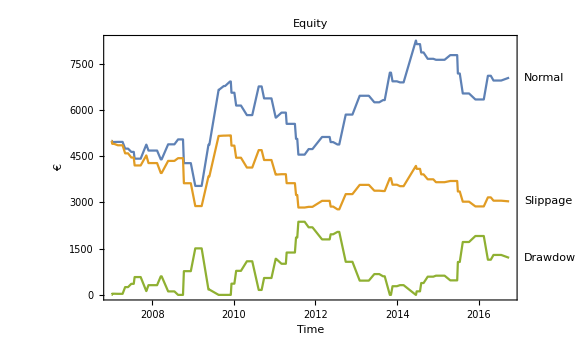

```mathematica
DateListPlot[{{{{2007,1,2},5000},{{2007,1,3},5000},{{2007,1,4},4987.915329970585},{{2007,1,5},4987.915329970585},{{2007,1,8},4962.1287703049475},{{2007,1,24},4962.1287703049475},{{2007,2,27},4965.617422120258},{{2007,4,10},4965.617422120258},{{2007,5,3},4747.384605451302},{{2007,5,29},4747.384605451302},{{2007,6,27},4641.224908678235},{{2007,7,19},4641.224908678235},{{2007,7,27},4421.444681557495},{{2007,9,19},4421.444681557495},{{2007,11,8},4874.899422655352},{{2007,11,9},4874.899422655352},{{2007,11,28},4684.456150252007},{{2008,2,13},4684.456150252007},{{2008,3,17},4398.944555028296},{{2008,3,25},4398.944555028296},{{2008,5,22},4886.676773486445},{{2008,7,17},4886.676773486445},{{2008,8,19},5046.50776287549},{{2008,10,2},5046.50776287549},{{2008,10,10},4276.236388078344},{{2008,12,11},4276.236388078344},{{2009,1,20},3536.662639938504},{{2009,3,18},3536.662639938504},{{2009,5,18},4873.53885155412},{{2009,5,26},4873.53885155412},{{2009,8,17},6659.2586887121015},{{2009,8,21},6659.2586887121015},{{2009,10,2},6778.763092389597},{{2009,10,14},6778.763092389597},{{2009,11,27},6926.151468057422},{{2009,12,4},6926.151468057422},{{2009,12,10},6561.852205850136},{{2010,1,5},6561.852205850136},{{2010,1,21},6145.509363868291},{{2010,3,5},6145.509363868291},{{2010,4,27},5835.384215259252},{{2010,6,14},5835.384215259252},{{2010,8,11},6765.947653125894},{{2010,9,6},6765.947653125894},{{2010,9,28},6377.857787928279},{{2010,12,3},6377.857787928279},{{2011,1,10},5754.290728101595},{{2011,1,13},5754.290728101595},{{2011,3,3},5915.902344008743},{{2011,4,11},5915.902344008743},{{2011,4,18},5551.465525874098},{{2011,7,1},5551.465525874098},{{2011,7,11},5064.589764164493},{{2011,7,22},5064.589764164493},{{2011,8,1},4552.252978790758},{{2011,9,26},4552.252978790758},{{2011,11,1},4732.48975914395},{{2011,12,5},4732.48975914395},{{2012,2,29},5125.157812759513},{{2012,5,7},5125.157812759513},{{2012,5,16},4959.639106864699},{{2012,6,7},4959.639106864699},{{2012,7,16},4881.7014412039725},{{2012,8,1},4881.7014412039725},{{2012,9,28},5852.177991733342},{{2012,11,27},5852.177991733342},{{2013,1,31},6463.15244673312},{{2013,4,23},6463.15244673312},{{2013,6,11},6250.808183452436},{{2013,7,25},6250.808183452436},{{2013,8,28},6322.514680714419},{{2013,9,12},6322.514680714419},{{2013,10,28},7213.327049027161},{{2013,11,7},7213.327049027161},{{2013,11,21},6931.855354054514},{{2013,12,30},6931.855354054514},{{2014,1,27},6897.26791273928},{{2014,2,28},6897.26791273928},{{2014,6,18},8253.99204184349},{{2014,6,19},8253.99204184349},{{2014,6,25},8139.047093530906},{{2014,7,25},8139.047093530906},{{2014,8,5},7868.813640163017},{{2014,8,26},7868.813640163017},{{2014,10,2},7662.6776909525215},{{2014,11,21},7662.6776909525215},{{2014,12,15},7630.5714995099825},{{2015,3,2},7630.5714995099825},{{2015,4,22},7782.412046722029},{{2015,6,23},7782.412046722029},{{2015,6,29},7185.692129765292},{{2015,7,16},7185.692129765292},{{2015,8,12},6537.600236531513},{{2015,10,7},6537.600236531513},{{2015,12,3},6342.75460007804},{{2016,2,16},6342.75460007804},{{2016,3,24},7111.867680499586},{{2016,4,19},7111.867680499586},{{2016,5,13},6957.5398960408365},{{2016,7,21},6957.5398960408365},{{2016,9,30},7051.353476902791}},{{{2007,1,2},5000},{{2007,1,3},5000},{{2007,1,4},4956.106271611142},{{2007,1,5},4956.106271611142},{{2007,1,8},4902.423738047214},{{2007,1,24},4902.423738047214},{{2007,2,27},4855.750035902588},{{2007,4,10},4855.750035902588},{{2007,5,3},4594.331822392467},{{2007,5,29},4594.331822392467},{{2007,6,27},4458.925541115312},{{2007,7,19},4458.925541115312},{{2007,7,27},4201.292729023426},{{2007,9,19},4201.292729023426},{{2007,11,8},4524.719367325731},{{2007,11,9},4524.719367325731},{{2007,11,28},4278.302067691995},{{2008,2,13},4278.302067691995},{{2008,3,17},3956.6132936755625},{{2008,3,25},3956.6132936755625},{{2008,5,22},4348.808926836433},{{2008,7,17},4348.808926836433},{{2008,8,19},4437.1016449677345},{{2008,10,2},4437.1016449677345},{{2008,10,10},3623.807213510085},{{2008,12,11},3623.807213510085},{{2009,1,20},2882.8430232172573},{{2009,3,18},2882.8430232172573},{{2009,5,18},3845.0787078240232},{{2009,5,26},3845.0787078240232},{{2009,8,17},5159.30063060187},{{2009,8,21},5159.30063060187},{{2009,10,2},5169.223144642015},{{2009,10,14},5169.223144642015},{{2009,11,27},5175.054096510069},{{2009,12,4},5175.054096510069},{{2009,12,10},4844.983860111796},{{2010,1,5},4844.983860111796},{{2010,1,21},4451.751420433316},{{2010,3,5},4451.751420433316},{{2010,4,27},4133.481698221998},{{2010,6,14},4133.481698221998},{{2010,8,11},4698.979001709773},{{2010,9,6},4698.979001709773},{{2010,9,28},4377.72960513283},{{2010,12,3},4377.72960513283},{{2011,1,10},3904.5522725642613},{{2011,1,13},3904.5522725642613},{{2011,3,3},3916.833518686539},{{2011,4,11},3916.833518686539},{{2011,4,18},3625.6514435636595},{{2011,7,1},3625.6514435636595},{{2011,7,11},3242.591844403521},{{2011,7,22},3242.591844403521},{{2011,8,1},2835.671082475523},{{2011,9,26},2835.671082475523},{{2011,11,1},2857.556613375481},{{2011,12,5},2857.556613375481},{{2012,2,29},3052.3374126086082},{{2012,5,7},3052.3374126086082},{{2012,5,16},2866.398921158967},{{2012,6,7},2866.398921158967},{{2012,7,16},2776.9677405388284},{{2012,8,1},2776.9677405388284},{{2012,9,28},3270.704534012231},{{2012,11,27},3270.704534012231},{{2013,1,31},3570.8378052609814},{{2013,4,23},3570.8378052609814},{{2013,6,11},3381.659964024375},{{2013,7,25},3381.659964024375},{{2013,8,28},3370.937050638799},{{2013,9,12},3370.937050638799},{{2013,10,28},3787.58282843136},{{2013,11,7},3787.58282843136},{{2013,11,21},3576.5000066806933},{{2013,12,30},3576.5000066806933},{{2014,1,27},3528.444595650378},{{2014,2,28},3528.444595650378},{{2014,6,18},4185.217019487837},{{2014,6,19},4185.217019487837},{{2014,6,25},4090.9840313044233},{{2014,7,25},4090.9840313044233},{{2014,8,5},3912.3711337285176},{{2014,8,26},3912.3711337285176},{{2014,10,2},3751.203579593348},{{2014,11,21},3751.203579593348},{{2014,12,15},3657.505322642336},{{2015,3,2},3657.505322642336},{{2015,4,22},3696.803368096315},{{2015,6,23},3696.803368096315},{{2015,6,29},3356.32249828622},{{2015,7,16},3356.32249828622},{{2015,8,12},3025.2668257488735},{{2015,10,7},3025.2668257488735},{{2015,12,3},2871.6500237058967},{{2016,2,16},2871.6500237058967},{{2016,3,24},3164.925761269139},{{2016,4,19},3164.925761269139},{{2016,5,13},3057.4191790852606},{{2016,7,21},3057.4191790852606},{{2016,9,30},3034.609955033947}},{{{2007,1,2},0},{{2007,1,3},0},{{2007,1,4},12.084670029415065},{{2007,1,5},12.084670029415065},{{2007,1,8},37.871229695052534},{{2007,1,24},37.871229695052534},{{2007,2,27},34.3825778797418},{{2007,4,10},34.3825778797418},{{2007,5,3},252.61539454869762},{{2007,5,29},252.61539454869762},{{2007,6,27},358.7750913217651},{{2007,7,19},358.7750913217651},{{2007,7,27},578.5553184425053},{{2007,9,19},578.5553184425053},{{2007,11,8},125.10057734464772},{{2007,11,9},125.10057734464772},{{2007,11,28},315.5438497479927},{{2008,2,13},315.5438497479927},{{2008,3,17},601.0554449717038},{{2008,3,25},601.0554449717038},{{2008,5,22},113.3232265135548},{{2008,7,17},113.3232265135548},{{2008,8,19},0.},{{2008,10,2},0.},{{2008,10,10},770.2713747971457},{{2008,12,11},770.2713747971457},{{2009,1,20},1509.8451229369857},{{2009,3,18},1509.8451229369857},{{2009,5,18},172.9689113213699},{{2009,5,26},172.9689113213699},{{2009,8,17},0.},{{2009,8,21},0.},{{2009,10,2},0.},{{2009,10,14},0.},{{2009,11,27},0.},{{2009,12,4},0.},{{2009,12,10},364.2992622072861},{{2010,1,5},364.2992622072861},{{2010,1,21},780.6421041891308},{{2010,3,5},780.6421041891308},{{2010,4,27},1090.7672527981695},{{2010,6,14},1090.7672527981695},{{2010,8,11},160.20381493152763},{{2010,9,6},160.20381493152763},{{2010,9,28},548.2936801291426},{{2010,12,3},548.2936801291426},{{2011,1,10},1171.8607399558268},{{2011,1,13},1171.8607399558268},{{2011,3,3},1010.2491240486788},{{2011,4,11},1010.2491240486788},{{2011,4,18},1374.6859421833242},{{2011,7,1},1374.6859421833242},{{2011,7,11},1861.5617038929286},{{2011,7,22},1861.5617038929286},{{2011,8,1},2373.898489266664},{{2011,9,26},2373.898489266664},{{2011,11,1},2193.6617089134716},{{2011,12,5},2193.6617089134716},{{2012,2,29},1800.9936552979088},{{2012,5,7},1800.9936552979088},{{2012,5,16},1966.512361192723},{{2012,6,7},1966.512361192723},{{2012,7,16},2044.4500268534493},{{2012,8,1},2044.4500268534493},{{2012,9,28},1073.9734763240795},{{2012,11,27},1073.9734763240795},{{2013,1,31},462.9990213243018},{{2013,4,23},462.9990213243018},{{2013,6,11},675.3432846049855},{{2013,7,25},675.3432846049855},{{2013,8,28},603.6367873430027},{{2013,9,12},603.6367873430027},{{2013,10,28},0.},{{2013,11,7},0.},{{2013,11,21},281.47169497264713},{{2013,12,30},281.47169497264713},{{2014,1,27},316.0591362878804},{{2014,2,28},316.0591362878804},{{2014,6,18},0.},{{2014,6,19},0.},{{2014,6,25},114.94494831258453},{{2014,7,25},114.94494831258453},{{2014,8,5},385.17840168047314},{{2014,8,26},385.17840168047314},{{2014,10,2},591.3143508909689},{{2014,11,21},591.3143508909689},{{2014,12,15},623.4205423335079},{{2015,3,2},623.4205423335079},{{2015,4,22},471.57999512146125},{{2015,6,23},471.57999512146125},{{2015,6,29},1068.2999120781988},{{2015,7,16},1068.2999120781988},{{2015,8,12},1716.3918053119778},{{2015,10,7},1716.3918053119778},{{2015,12,3},1911.23744176545},{{2016,2,16},1911.23744176545},{{2016,3,24},1142.1243613439046},{{2016,4,19},1142.1243613439046},{{2016,5,13},1296.4521458026538},{{2016,7,21},1296.4521458026538},{{2016,9,30},1202.6385649406993}}},ImageSize->Large,PlotLabel-> "Equity",AxesLabel-> {"Time","€"},PlotLabels->{"Normal","Slippage","Drawdown"}]
```

```mathematica
{daysTrade,netTradeReturns,mfe,mae,win}={{2,4,35,24,30,9,51,20,34,59,34,9,41,62,84,43,45,7,17,54,59,23,39,50,8,11,11,37,87,10,40,59,66,50,35,47,15,29,111,7,12,38,25,52,7,28,58,38,25,72},{-0.0024169340058830535,-0.005169807015507066,0.0007030554781624065,-0.04394877778879969,-0.022361722421049834,-0.04735392734572974,0.10255804918000777,-0.0390660926291706,-0.060948717645345374,0.1108748274402862,0.03270750180495585,-0.15263453679069483,-0.1729496877678901,0.3780050142523237,0.3664113268715474,0.017945601644829168,0.021742665093768432,-0.052597645876991006,-0.06344898192169879,-0.05046370125678723,0.15946909467130932,-0.05735927694006271,-0.09777061210222404,0.02808541026922806,-0.06160291312173616,-0.08770220393883177,-0.1011605696080018,0.03959287438394288,0.08297282690509022,-0.03229533839577403,-0.015714382434167895,0.19879883319739067,0.10440120855223922,-0.032854596117103174,0.011471556182416354,0.14089526292916132,-0.03902106379754511,-0.004989636907960504,0.196704571472182,-0.013925982449446761,-0.03320209973753263,-0.0261965727792004,-0.0041899441340782495,0.01989897443747135,-0.07667544629792211,-0.0901919928560797,-0.02980384688630744,0.12125852707782259,-0.021700035966910503,0.013483728769609904},{0.0058630486647770486,0.004480254060617028,0.026444787788218793,0.013358673603694138,0.042911420096078956,0.009469968417551433,0.13305965284445165,0.01702571016075538,0.03993713783777508,0.16184098600415187,0.10526127586535727,0.054481588046301876,0.08203974906653166,0.4441197610212624,0.41785570147871254,0.09408437657097557,0.058145629153506295,0.01505765913385737,0.023184139575402662,0.06356836389869769,0.21683047992665716,0.024233987544977964,0.029669650366383804,0.10495179604370497,0.008213646892905935,0.018134677675147426,0.02351818282532303,0.12438623702493623,0.12687440721062204,0.055198220872784365,0.11254513173464509,0.2880252636069367,0.15137777800090202,0.03761295210821736,0.09562764456981654,0.1780964797913953,0.024397636005455192,0.051968987487525764,0.20873082500190798,0.008012209080503707,0.020341207349081625,0.04523668833300487,0.09026756836224648,0.09735190570947494,0.00819432250512131,0.011162375353475307,0.028375547514759125,0.2721704023388556,0.1233665028174078,0.10955529625307925},{-0.010696916676543267,-0.012061656272071342,-0.01878473189635521,-0.06970548946108568,-0.029934284789247645,-0.059281518871679095,-0.014536080460327283,-0.05375590011488307,-0.07271619781834682,-0.009663343960107373,-0.016673704859077154,-0.19225659617462076,-0.22246923410772645,-0.043732278919200396,-0.018404843031526008,-0.025217512459542957,-0.05145937044865645,-0.060867130794217905,-0.09190713577528098,-0.07481584842616862,-0.03404787259708464,-0.07402350270250013,-0.10616981869068343,-0.026311504677569264,-0.0794764375566338,-0.10738434847800382,-0.1292574813703803,-0.04014437457292097,-0.08687114969674692,-0.05435413932877087,-0.06277972075670746,-0.08352868916402201,-0.02793208210859055,-0.04822931776171613,-0.01645510108133519,-0.010864841373315781,-0.04940142445825135,-0.039686804329469694,-0.04327253300770817,-0.02327355971003431,-0.046587926509186195,-0.046812422034009704,-0.024551602469861877,-0.03551201591917941,-0.10008779631255482,-0.10700997172198234,-0.06455913159398208,-0.046916330224140324,-0.05766694640930348,-0.1043692467263061},{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1]}};
TabView[
{"MFE-MAE"-> ListPlot[Apply[Style,Transpose@{Transpose@{mfe,-mae},win},1],
ImageSize->Large,PlotLabel-> "MFE-MAE",AxesLabel-> {"MFE","MAE"}],
"Returns-ETD"-> ListPlot[Apply[Style,Transpose@{Transpose@{netTradeReturns,mfe-netTradeReturns},win},1],
ImageSize->Large,PlotLabel-> "Returns-ETD",AxesLabel-> {"Returns","ETD"}],
"Days-Eficiency"-> ListPlot[Apply[Style,Transpose@{Transpose@{daysTrade,netTradeReturns/(mfe-mae)},win},1],
ImageSize->Large,PlotLabel-> "Days-Eficiency",AxesLabel-> {"Days","Eficiency"}]}
]
```

123

```mathematica
Manipulate[
TradingChart[s[[If[index[[i,1]]-5>0,index[[i,1]]-5,1];;index[[i,2]]+5]],ImageSize->Large],
{{i,3},Range[long]},
Initialization:> (
s={{{2007,1,1},{14.56848,14.56848,14.56848,14.56848,0.}},{{2007,1,2},{14.72299,14.92898,14.67142,14.92898,5.43512*^7}},{{2007,1,3},{14.92898,15.00116,14.86726,14.93934,5.88321*^7}},{{2007,1,4},{14.83629,15.02177,14.77446,15.02177,6.21218*^7}},{{2007,1,5},{14.92898,15.01142,14.87751,14.92898,4.45893*^7}},{{2007,1,8},{14.91873,14.9702,14.76421,14.86726,6.63954*^7}},{{2007,1,9},{14.90847,14.99081,14.80543,14.86726,9.22505*^7}},{{2007,1,10},{14.78482,14.79507,14.49629,14.54787,7.17233*^7}},{{2007,1,11},{14.6302,14.73324,14.42421,14.73324,8.77054*^7}},{{2007,1,12},{14.73324,14.75385,14.61995,14.72299,5.73913*^7}},{{2007,1,15},{14.82604,14.8569,14.75385,14.75385,4.41157*^7}},{{2007,1,16},{14.7436,14.81568,14.59934,14.6302,1.495281*^8}},{{2007,1,17},{14.64056,14.70238,14.46543,14.52726,4.11227*^7}},{{2007,1,18},{14.61995,14.69203,14.46543,14.49629,4.12495*^7}},{{2007,1,19},{14.49629,14.77446,14.39324,14.73324,5.78965*^7}},{{2007,1,22},{14.77446,14.83629,14.55812,14.60959,1.000621*^8}},{{2007,1,23},{14.65081,14.67142,14.54787,14.58898,9.83079*^7}},{{2007,1,24},{14.69203,14.92898,14.68177,14.92898,1.196365*^8}},{{2007,1,25},{14.92898,14.94959,14.79507,14.87751,1.662853*^8}},{{2007,1,26},{14.81568,14.81568,14.66116,14.70238,1.150445*^8}},{{2007,1,29},{14.88786,14.88786,14.7436,14.87751,9.60744*^7}},{{2007,1,30},{14.82604,14.98055,14.81568,14.9702,9.58485*^7}},{{2007,1,31},{14.90847,15.06299,14.88786,15.03202,8.98394*^7}},{{2007,2,1},{15.01142,15.02177,14.80543,14.83629,7.49324*^7}},{{2007,2,2},{14.80543,14.83629,14.71263,14.83629,7.05024*^7}},{{2007,2,5},{14.8569,14.86726,14.71263,14.72299,1.959315*^8}},{{2007,2,6},{14.77446,14.86726,14.73324,14.81568,7.60903*^7}},{{2007,2,7},{14.83629,14.84665,14.7436,14.84665,1.067241*^8}},{{2007,2,8},{14.84665,14.91873,14.80543,14.89812,7.3811*^7}},{{2007,2,9},{14.92898,15.01142,14.88786,14.9702,7.66691*^7}},{{2007,2,12},{14.94959,14.9702,14.77446,14.81568,9.43311*^7}},{{2007,2,13},{14.86726,14.95994,14.8569,14.95994,3.74984*^7}},{{2007,2,14},{14.99081,15.06299,14.91873,15.04238,6.96352*^7}},{{2007,2,15},{15.04238,15.07324,14.94959,15.02177,1.007931*^8}},{{2007,2,16},{14.92898,15.03202,14.87751,14.93934,7.337*^7}},{{2007,2,19},{14.9702,15.09385,14.94959,15.04238,3.26965*^7}},{{2007,2,20},{15.09385,15.12482,15.02177,15.09385,7.08849*^7}},{{2007,2,21},{15.13507,15.1969,14.92898,14.95994,4.52508*^7}},{{2007,2,22},{15.04238,15.13507,14.9702,15.04238,3.52422*^7}},{{2007,2,23},{15.05263,15.0836,14.87751,14.98055,3.96279*^7}},{{2007,2,26},{15.01142,15.04238,14.94959,15.01142,4.43979*^7}},{{2007,2,27},{14.87751,14.88786,14.52726,14.56848,7.62362*^7}},{{2007,2,28},{14.27995,14.56848,14.16665,14.43446,1.923057*^8}},{{2007,3,1},{14.35203,14.48604,13.80604,14.13568,1.381157*^8}},{{2007,3,2},{14.23873,14.27995,13.91934,14.05325,7.55257*^7}},{{2007,3,5},{13.75447,13.95031,13.68239,13.80604,1.142495*^8}},{{2007,3,6},{13.89873,13.9297,13.79568,13.91934,6.26395*^7}},{{2007,3,7},{13.99142,14.02238,13.84726,13.96056,6.24776*^7}},{{2007,3,8},{14.02238,14.25934,13.99142,14.22848,5.00696*^7}},{{2007,3,9},{14.21812,14.33142,14.07386,14.2903,1.144102*^8}},{{2007,3,12},{14.33142,14.37264,14.05325,14.09446,5.55342*^7}},{{2007,3,13},{14.0636,14.09446,13.81629,13.82665,6.92237*^7}},{{2007,3,14},{13.54848,13.5897,13.19812,13.21873,1.307561*^8}},{{2007,3,15},{13.4969,13.57934,13.39386,13.56909,9.29491*^7}},{{2007,3,16},{13.54848,13.56909,13.34239,13.48665,1.757802*^8}},{{2007,3,19},{13.65142,13.77508,13.59995,13.76482,9.42085*^7}},{{2007,3,20},{13.73386,13.88848,13.63081,13.87812,7.88964*^7}},{{2007,3,21},{13.87812,13.98117,13.7236,13.76482,6.61119*^7}},{{2007,3,22},{14.00178,14.08421,13.89873,14.04299,6.82685*^7}},{{2007,3,23},{13.97091,14.02238,13.86787,13.95031,4.71718*^7}},{{2007,3,26},{13.95031,13.97091,13.62056,13.703,5.99268*^7}},{{2007,3,27},{13.78543,14.02238,13.71325,13.86787,6.71364*^7}},{{2007,3,28},{13.76482,13.80604,13.48665,13.68239,4.74978*^7}},{{2007,3,29},{13.71325,13.76482,13.65142,13.73386,5.70535*^7}},{{2007,3,30},{13.74421,14.03264,13.65142,13.76482,7.59863*^7}},{{2007,4,2},{13.75447,13.80604,13.68239,13.77508,5.34601*^7}},{{2007,4,3},{13.78543,14.04299,13.77508,14.03264,7.25203*^7}},{{2007,4,4},{14.05325,14.1769,14.03264,14.15629,7.11847*^7}},{{2007,4,5},{14.12543,14.1769,14.09446,14.1769,1.038749*^8}},{{2007,4,6},{14.1769,14.1769,14.1769,14.1769,0.}},{{2007,4,9},{14.1769,14.1769,14.1769,14.1769,0.}},{{2007,4,10},{14.26969,14.38299,14.14604,14.34177,4.99644*^7}},{{2007,4,11},{14.32117,14.45507,14.24909,14.31091,4.17037*^7}},{{2007,4,12},{14.26969,14.27995,14.05325,14.18726,7.53362*^7}},{{2007,4,13},{14.21812,14.2903,14.14604,14.21812,7.24807*^7}},{{2007,4,16},{14.15629,14.37264,14.13568,14.34177,7.2869*^7}},{{2007,4,17},{14.31091,14.32117,14.11507,14.22848,7.44246*^7}},{{2007,4,18},{14.13568,14.19751,14.03264,14.12543,5.19279*^7}},{{2007,4,19},{13.97091,14.03264,13.81629,14.03264,9.29524*^7}},{{2007,4,20},{14.04299,14.33142,14.03264,14.26969,1.003586*^8}},{{2007,4,23},{14.31091,14.33142,14.14604,14.19751,9.18335*^7}},{{2007,4,24},{14.14604,14.20787,13.703,13.76482,1.333088*^8}},{{2007,4,25},{13.59995,13.95031,13.52787,13.91934,1.187464*^8}},{{2007,4,26},{14.14604,14.14604,13.84726,13.93995,1.465983*^8}},{{2007,4,27},{13.93995,13.93995,13.55873,13.6102,1.7673*^8}},{{2007,4,30},{13.55873,13.75447,13.54848,13.5897,1.72233*^8}},{{2007,5,1},{13.5897,13.5897,13.5897,13.5897,0.}},{{2007,5,2},{13.54848,13.56909,13.39386,13.45569,7.91644*^7}},{{2007,5,3},{13.53812,13.6102,13.2702,13.59995,1.754037*^8}},{{2007,5,4},{13.59995,13.9297,13.59995,13.87812,1.771793*^8}},{{2007,5,7},{13.96056,13.98117,13.76482,13.81629,5.13027*^7}},{{2007,5,8},{13.78543,13.78543,13.68239,13.73386,1.042241*^8}},{{2007,5,9},{13.81629,13.90909,13.67203,13.85751,6.82165*^7}},{{2007,5,10},{13.82665,13.95031,13.703,13.80604,5.33807*^7}},{{2007,5,11},{13.703,13.99142,13.67203,13.97091,1.611895*^8}},{{2007,5,14},{14.01203,14.01203,13.76482,13.78543,8.26092*^7}},{{2007,5,15},{13.75447,13.90909,13.68239,13.90909,7.05786*^7}},{{2007,5,16},{13.84726,13.99142,13.82665,13.91934,4.59931*^7}},{{2007,5,17},{13.99142,13.99142,13.8369,13.86787,4.82633*^7}},{{2007,5,18},{13.90909,14.19751,13.84726,14.16665,1.859159*^8}},{{2007,5,21},{14.20787,14.22848,14.02238,14.02238,6.31706*^7}},{{2007,5,22},{14.04299,14.16665,14.00178,14.0636,4.33137*^7}},{{2007,5,23},{14.03264,14.19751,14.00178,14.19751,7.52948*^7}},{{2007,5,24},{14.0636,14.23873,14.04299,14.04299,5.41747*^7}},{{2007,5,25},{13.99142,14.10482,13.90909,14.08421,1.255945*^8}},{{2007,5,28},{14.12543,14.19751,14.04299,14.16665,2.3148*^7}},{{2007,5,29},{14.2903,14.38299,14.18726,14.35203,5.49003*^7}},{{2007,5,30},{14.36238,14.39324,14.20787,14.32117,5.06257*^7}},{{2007,5,31},{14.39324,14.71263,14.36238,14.71263,1.257432*^8}},{{2007,6,1},{14.71263,14.71263,14.71263,14.71263,0.}},{{2007,6,4},{14.84665,14.87751,14.73324,14.80543,8.30126*^7}},{{2007,6,5},{14.83629,14.89812,14.66116,14.73324,1.758126*^8}},{{2007,6,6},{14.66116,14.68177,14.44482,14.48604,1.126892*^8}},{{2007,6,7},{14.57873,14.61995,14.11507,14.21812,1.531035*^8}},{{2007,6,8},{14.1769,14.37264,14.09446,14.33142,9.47915*^7}},{{2007,6,11},{14.42421,14.57873,14.38299,14.44482,5.79636*^7}},{{2007,6,12},{14.43446,14.43446,14.05325,14.11507,8.18244*^7}},{{2007,6,13},{14.0636,14.13568,13.95031,14.11507,9.327*^7}},{{2007,6,14},{14.24909,14.37264,14.16665,14.37264,1.162985*^8}},{{2007,6,15},{14.38299,14.49629,14.33142,14.42421,1.538456*^8}},{{2007,6,18},{14.32117,14.43446,14.21812,14.2903,1.17278*^8}},{{2007,6,19},{14.30056,14.34177,14.15629,14.23873,6.43724*^7}},{{2007,6,20},{14.27995,14.38299,14.23873,14.32117,5.01904*^7}},{{2007,6,21},{14.18726,14.24909,13.99142,14.07386,7.08404*^7}},{{2007,6,22},{14.15629,14.18726,14.01203,14.08421,4.68619*^7}},{{2007,6,25},{13.96056,14.18726,13.87812,14.15629,5.08777*^7}},{{2007,6,26},{14.04299,14.23873,14.02238,14.03264,6.79274*^7}},{{2007,6,27},{13.93995,14.07386,13.85751,14.00178,6.86485*^7}},{{2007,6,28},{14.10482,14.19751,14.05325,14.10482,4.89373*^7}},{{2007,6,29},{14.16665,14.1769,13.99142,14.10482,8.59646*^7}},{{2007,7,2},{14.08421,14.14604,14.02238,14.05325,6.47971*^7}},{{2007,7,3},{14.10482,14.20787,14.10482,14.18726,7.73575*^7}},{{2007,7,4},{14.20787,14.36238,14.18726,14.30056,3.74205*^7}},{{2007,7,5},{14.36238,14.37264,14.18726,14.24909,8.7387*^7}},{{2007,7,6},{14.18726,14.47568,14.1769,14.47568,4.68753*^7}},{{2007,7,9},{14.49629,14.59934,14.41385,14.43446,6.57349*^7}},{{2007,7,10},{14.43446,14.56848,14.21812,14.31091,5.991*^7}},{{2007,7,11},{14.14604,14.30056,13.99142,14.22848,8.84363*^7}},{{2007,7,12},{14.2903,14.44482,14.11507,14.44482,5.77905*^7}},{{2007,7,13},{14.56848,14.64056,14.5169,14.58898,7.77341*^7}},{{2007,7,16},{14.60959,14.67142,14.54787,14.66116,2.87831*^7}},{{2007,7,17},{14.6302,14.7436,14.60959,14.72299,2.429698*^8}},{{2007,7,18},{14.52726,14.72299,14.5169,14.5169,4.66398*^7}},{{2007,7,19},{14.60959,14.82604,14.54787,14.77446,1.810878*^8}},{{2007,7,20},{14.71263,14.80543,14.4036,14.4036,5.5837*^7}},{{2007,7,23},{14.4036,14.54787,14.2903,14.54787,1.352826*^8}},{{2007,7,24},{14.46543,14.64056,14.30056,14.35203,4.64881*^7}},{{2007,7,25},{14.27995,14.54787,14.18726,14.32117,1.333264*^8}},{{2007,7,26},{14.45507,14.52726,13.90909,13.90909,1.496976*^8}},{{2007,7,27},{13.8369,14.16665,13.81629,14.11507,1.223369*^8}},{{2007,7,30},{14.07386,14.16665,13.87812,13.96056,8.83343*^7}},{{2007,7,31},{14.0636,14.34177,14.05325,14.34177,7.76613*^7}},{{2007,8,1},{13.90909,14.16665,13.80604,14.01203,1.260436*^8}},{{2007,8,2},{14.12543,14.14604,13.97091,14.08421,2.483086*^8}},{{2007,8,3},{14.08421,14.10482,13.90909,13.91934,5.7805*^7}},{{2007,8,6},{13.80604,13.85751,13.69264,13.76482,1.103674*^8}},{{2007,8,7},{13.98117,14.16665,13.97091,14.16665,5.90418*^7}},{{2007,8,8},{14.1769,14.52726,14.1769,14.49629,6.57045*^7}},{{2007,8,9},{14.38299,14.45507,14.1769,14.30056,6.29973*^7}},{{2007,8,10},{14.02238,14.20787,13.78543,13.8369,1.192185*^8}},{{2007,8,13},{13.97091,14.20787,13.9297,14.16665,4.41503*^7}},{{2007,8,14},{14.02238,14.09446,13.87812,13.9297,7.64599*^7}},{{2007,8,15},{13.78543,13.97091,13.67203,13.91934,5.37358*^7}},{{2007,8,16},{13.65142,13.71325,13.40421,13.40421,7.83193*^7}},{{2007,8,17},{13.39386,14.32117,13.34239,13.96056,3.318602*^8}},{{2007,8,20},{14.08421,14.19751,13.85751,13.86787,7.17872*^7}},{{2007,8,21},{13.89873,13.93995,13.63081,13.79568,4.44389*^7}},{{2007,8,22},{13.8369,13.97091,13.82665,13.88848,4.40058*^7}},{{2007,8,23},{14.01203,14.05325,13.80604,13.80604,2.83564*^7}},{{2007,8,24},{13.703,13.8369,13.67203,13.81629,2.40666*^7}},{{2007,8,27},{13.88848,13.90909,13.77508,13.81629,1.70738*^7}},{{2007,8,28},{13.81629,13.81629,13.47629,13.53812,5.83439*^7}},{{2007,8,29},{13.45569,13.62056,13.38361,13.57934,6.99842*^7}},{{2007,8,30},{13.66178,13.703,13.47629,13.68239,4.63239*^7}},{{2007,8,31},{13.75447,13.86787,13.73386,13.80604,8.74392*^7}},{{2007,9,3},{13.85751,13.89873,13.76482,13.86787,2.46025*^7}},{{2007,9,4},{13.81629,13.98117,13.74421,13.98117,8.44256*^7}},{{2007,9,5},{13.91934,13.93995,13.59995,13.59995,6.55406*^7}},{{2007,9,6},{13.65142,13.78543,13.44543,13.64117,8.05843*^7}},{{2007,9,7},{13.57934,13.59995,13.1363,13.24959,9.23592*^7}},{{2007,9,10},{13.23934,13.31142,13.01264,13.06422,6.9619*^7}},{{2007,9,11},{13.18787,13.32178,13.06422,13.25995,4.1653*^7}},{{2007,9,12},{13.20848,13.2702,13.023,13.15691,4.38898*^7}},{{2007,9,13},{13.11569,13.37325,12.84787,13.29081,6.62683*^7}},{{2007,9,14},{13.24959,13.24959,12.98178,13.15691,5.36189*^7}},{{2007,9,17},{13.10543,13.11569,12.74483,12.94056,7.89887*^7}},{{2007,9,18},{12.7963,13.39386,12.7963,13.34239,7.63277*^7}},{{2007,9,19},{13.69264,13.97091,13.67203,13.85751,1.10783*^8}},{{2007,9,20},{13.73386,13.81629,13.67203,13.80604,7.39563*^7}},{{2007,9,21},{13.75447,13.95031,13.74421,13.82665,1.155886*^8}},{{2007,9,24},{13.82665,13.98117,13.74421,13.85751,7.64377*^7}},{{2007,9,25},{13.74421,13.85751,13.62056,13.79568,4.20739*^7}},{{2007,9,26},{13.88848,14.00178,13.86787,13.9297,5.79209*^7}},{{2007,9,27},{13.99142,14.13568,13.98117,14.09446,5.90955*^7}},{{2007,9,28},{14.03264,14.19751,13.95031,14.04299,4.7387*^7}},{{2007,10,1},{13.91934,14.07386,13.81629,14.05325,5.33459*^7}},{{2007,10,2},{14.18726,14.38299,14.16665,14.30056,7.09589*^7}},{{2007,10,3},{14.21812,14.34177,14.19751,14.24909,6.90075*^7}},{{2007,10,4},{14.26969,14.44482,14.20787,14.23873,9.51178*^7}},{{2007,10,5},{14.2903,14.42421,14.23873,14.36238,5.00902*^7}},{{2007,10,8},{14.37264,14.39324,14.22848,14.27995,6.1704*^7}},{{2007,10,9},{14.23873,14.26969,14.16665,14.18726,4.73188*^7}},{{2007,10,10},{14.18726,14.25934,14.0636,14.11507,8.07661*^7}},{{2007,10,11},{14.07386,14.1769,14.03264,14.13568,1.310393*^8}},{{2007,10,12},{14.09446,14.2903,13.96056,14.23873,8.62378*^7}},{{2007,10,15},{14.37264,14.56848,14.34177,14.35203,2.527745*^8}},{{2007,10,16},{14.2903,14.37264,14.25934,14.33142,1.113245*^8}},{{2007,10,17},{14.39324,14.69203,14.31091,14.59934,1.266498*^8}},{{2007,10,18},{14.60959,14.79507,14.56848,14.65081,9.56389*^7}},{{2007,10,19},{14.58898,14.80543,14.56848,14.64056,1.121483*^8}},{{2007,10,22},{14.34177,14.44482,14.27995,14.41385,1.608015*^8}},{{2007,10,23},{14.5169,14.57873,14.42421,14.49629,1.394221*^8}},{{2007,10,24},{14.54787,14.54787,14.1769,14.23873,8.01278*^7}},{{2007,10,25},{14.48604,14.6302,14.4036,14.57873,1.165473*^8}},{{2007,10,26},{14.70238,14.93934,14.66116,14.81568,1.387654*^8}},{{2007,10,29},{14.93934,15.24847,14.91873,15.07324,8.28911*^7}},{{2007,10,30},{15.07324,15.44421,15.07324,15.37202,1.275978*^8}},{{2007,10,31},{15.4236,15.49568,15.37202,15.45446,7.59703*^7}},{{2007,11,1},{15.29994,15.40299,14.8569,15.0836,7.12335*^7}},{{2007,11,2},{14.94959,15.18665,14.94959,15.14543,1.413765*^8}},{{2007,11,5},{14.98055,15.10421,14.82604,14.9702,2.015273*^8}},{{2007,11,6},{15.07324,15.10421,14.95994,14.98055,8.52096*^7}},{{2007,11,7},{14.98055,15.02177,14.69203,14.87751,8.01276*^7}},{{2007,11,8},{14.64056,15.66055,14.56848,15.45446,1.753299*^8}},{{2007,11,9},{15.63994,15.69141,15.16604,15.22786,8.65263*^7}},{{2007,11,12},{15.14543,15.38238,15.07324,15.25872,1.371082*^8}},{{2007,11,13},{15.17629,15.37202,15.0836,15.29994,8.72105*^7}},{{2007,11,14},{15.45446,15.56786,15.24847,15.26908,1.31751*^8}},{{2007,11,15},{15.3102,15.38238,15.0836,15.18665,1.61327*^8}},{{2007,11,16},{15.09385,15.32055,14.99081,15.22786,1.951056*^8}},{{2007,11,19},{15.27933,15.40299,15.00116,15.05263,1.299832*^8}},{{2007,11,20},{15.1969,15.25872,15.01142,15.22786,7.78251*^7}},{{2007,11,21},{15.04238,15.09385,14.7436,14.89812,7.87524*^7}},{{2007,11,22},{14.94959,15.03202,14.7436,14.78482,5.53569*^7}},{{2007,11,23},{14.7436,14.95994,14.70238,14.92898,5.99489*^7}},{{2007,11,26},{15.00116,15.06299,14.77446,14.78482,9.04692*^7}},{{2007,11,27},{14.73324,14.91873,14.65081,14.80543,8.15292*^7}},{{2007,11,28},{14.89812,15.05263,14.59934,14.99081,9.37533*^7}},{{2007,11,29},{15.11446,15.20725,14.7436,14.98055,8.16158*^7}},{{2007,11,30},{15.00116,15.17629,14.95994,15.0836,8.42588*^7}},{{2007,12,3},{15.07324,15.17629,15.00116,15.07324,4.11075*^7}},{{2007,12,4},{15.06299,15.16604,14.95994,15.02177,5.95416*^7}},{{2007,12,5},{15.12482,15.1969,15.0836,15.14543,5.24342*^7}},{{2007,12,6},{15.24847,15.37202,15.05263,15.13507,4.92429*^7}},{{2007,12,7},{15.25872,15.40299,15.1969,15.3308,5.75402*^7}},{{2007,12,10},{15.28969,15.47507,15.26908,15.44421,3.83566*^7}},{{2007,12,11},{15.49568,15.5369,15.35141,15.45446,5.70388*^7}},{{2007,12,12},{15.26908,15.57811,15.16604,15.40299,6.64031*^7}},{{2007,12,13},{15.26908,15.28969,15.01142,15.07324,7.11782*^7}},{{2007,12,14},{15.13507,15.17629,14.82604,15.13507,7.26968*^7}},{{2007,12,17},{14.86726,14.95994,14.78482,14.82604,6.30527*^7}},{{2007,12,18},{14.79507,14.9702,14.76421,14.78482,6.25403*^7}},{{2007,12,19},{14.83629,15.00116,14.7436,14.79507,7.09852*^7}},{{2007,12,20},{14.84665,14.94959,14.79507,14.88786,6.19928*^7}},{{2007,12,21},{15.03202,15.16604,14.94959,15.16604,1.578497*^8}},{{2007,12,24},{15.16604,15.16604,15.16604,15.16604,0.}},{{2007,12,25},{15.16604,15.16604,15.16604,15.16604,0.}},{{2007,12,26},{15.16604,15.16604,15.16604,15.16604,0.}},{{2007,12,27},{15.1969,15.3102,15.12482,15.20725,8.92265*^7}},{{2007,12,28},{15.22786,15.25872,15.17629,15.23812,4.17352*^7}},{{2007,12,31},{15.23812,15.23812,15.23812,15.23812,0.}},{{2008,1,1},{15.23812,15.23812,15.23812,15.23812,0.}},{{2008,1,2},{15.11446,15.20725,14.93934,15.03202,9.53684*^7}},{{2008,1,3},{14.99081,15.06299,14.79507,14.88786,1.038276*^8}},{{2008,1,4},{14.83629,14.92898,14.49629,14.67142,9.22008*^7}},{{2008,1,7},{14.61995,14.72299,14.47568,14.57873,6.60212*^7}},{{2008,1,8},{14.58898,14.60959,14.25934,14.35203,7.62048*^7}},{{2008,1,9},{14.22848,14.2903,14.04299,14.0636,1.103176*^8}},{{2008,1,10},{14.10482,14.13568,13.79568,13.89873,1.212485*^8}},{{2008,1,11},{13.85751,14.19751,13.82665,14.12543,9.51317*^7}},{{2008,1,14},{13.97091,14.15629,13.82665,13.9297,1.511796*^8}},{{2008,1,15},{13.82665,13.87812,13.39386,13.39386,1.26372*^8}},{{2008,1,16},{13.35264,13.42482,13.04361,13.23934,1.921633*^8}},{{2008,1,17},{13.43508,13.55873,13.03325,13.1363,1.403598*^8}},{{2008,1,18},{13.08483,13.22898,12.78605,12.81691,2.893349*^8}},{{2008,1,21},{12.74483,12.76544,11.50849,11.663,2.564301*^8}},{{2008,1,22},{10.81813,12.30178,10.81813,12.19874,2.080455*^8}},{{2008,1,23},{12.38422,12.43569,11.34361,11.61143,1.334191*^8}},{{2008,1,24},{12.26056,12.4563,12.15752,12.37386,1.893285*^8}},{{2008,1,25},{12.57995,12.78605,12.343,12.4563,1.591438*^8}},{{2008,1,28},{12.21935,12.36361,12.04422,12.35325,1.386456*^8}},{{2008,1,29},{12.41508,12.50787,12.26056,12.42544,9.16879*^7}},{{2008,1,30},{12.36361,12.4563,12.26056,12.37386,9.12378*^7}},{{2008,1,31},{12.37386,12.37386,11.86909,12.18848,1.580779*^8}},{{2008,2,1},{12.26056,12.43569,12.10605,12.43569,6.74611*^7}},{{2008,2,4},{12.49752,12.50787,12.27092,12.35325,5.56796*^7}},{{2008,2,5},{12.23995,12.26056,11.65265,11.69386,8.69298*^7}},{{2008,2,6},{11.51874,12.03386,11.46727,11.95143,1.016395*^8}},{{2008,2,7},{12.06483,12.06483,11.59082,11.95143,9.99083*^7}},{{2008,2,8},{12.07508,12.16787,11.84849,11.98239,7.23876*^7}},{{2008,2,11},{11.79691,12.003,11.67326,11.7763,4.67452*^7}},{{2008,2,12},{11.93082,12.21935,11.63204,12.21935,7.56038*^7}},{{2008,2,13},{12.12666,12.47691,12.03386,12.32239,6.34634*^7}},{{2008,2,14},{12.46666,12.48726,12.18848,12.26056,4.98009*^7}},{{2008,2,15},{12.19874,12.31203,11.86909,11.97204,7.52763*^7}},{{2008,2,18},{12.05447,12.30178,12.03386,12.27092,3.03576*^7}},{{2008,2,19},{12.16787,12.37386,11.99264,12.21935,5.17593*^7}},{{2008,2,20},{12.03386,12.05447,11.87935,12.003,7.64808*^7}},{{2008,2,21},{12.10605,12.27092,12.03386,12.10605,3.66179*^7}},{{2008,2,22},{12.01325,12.27092,11.98239,12.07508,6.01355*^7}},{{2008,2,25},{12.2297,12.38422,12.17813,12.35325,4.44902*^7}},{{2008,2,26},{12.46666,12.67264,12.39447,12.67264,5.71387*^7}},{{2008,2,27},{12.72422,12.74483,12.4563,12.69325,4.99052*^7}},{{2008,2,28},{12.61092,12.62117,12.41508,12.41508,4.38443*^7}},{{2008,2,29},{12.33264,12.36361,12.17813,12.29143,5.10618*^7}},{{2008,3,3},{12.10605,12.17813,11.97204,12.05447,4.60577*^7}},{{2008,3,4},{12.10605,12.14727,11.71447,11.84849,4.8865*^7}},{{2008,3,5},{11.94117,12.10605,11.81752,12.08544,4.72501*^7}},{{2008,3,6},{12.08544,12.09569,11.71447,11.78666,5.0318*^7}},{{2008,3,7},{11.65265,11.84849,11.5496,11.65265,7.67829*^7}},{{2008,3,10},{11.65265,11.72483,11.48788,11.55996,4.4628*^7}},{{2008,3,11},{11.55996,12.12666,11.55996,11.94117,6.52213*^7}},{{2008,3,12},{12.21935,12.26056,11.98239,12.09569,5.1392*^7}},{{2008,3,13},{11.85874,11.92057,11.62178,11.87935,5.90795*^7}},{{2008,3,14},{11.96178,12.26056,11.74544,11.85874,6.21555*^7}},{{2008,3,17},{11.53935,11.65265,11.36422,11.50849,8.66277*^7}},{{2008,3,18},{11.72483,11.99264,11.58057,11.97204,6.52538*^7}},{{2008,3,19},{12.09569,12.25031,11.87935,12.13691,7.26128*^7}},{{2008,3,20},{12.02361,12.41508,11.89996,12.38422,1.051784*^8}},{{2008,3,21},{12.38422,12.38422,12.38422,12.38422,0.}},{{2008,3,24},{12.38422,12.38422,12.38422,12.38422,0.}},{{2008,3,25},{12.67264,12.91995,12.67264,12.9096,9.17249*^7}},{{2008,3,26},{12.86848,12.9302,12.71386,12.9302,6.10033*^7}},{{2008,3,27},{12.82726,13.17751,12.82726,13.14665,6.63117*^7}},{{2008,3,28},{13.14665,13.17751,13.01264,13.09508,4.42063*^7}},{{2008,3,31},{13.023,13.05386,12.78605,13.00239,5.71547*^7}},{{2008,4,1},{12.98178,13.73386,12.9302,13.59995,7.25574*^7}},{{2008,4,2},{13.86787,13.87812,13.69264,13.84726,6.81684*^7}},{{2008,4,3},{13.89873,13.89873,13.63081,13.77508,5.97557*^7}},{{2008,4,4},{13.79568,13.82665,13.55873,13.76482,6.26984*^7}},{{2008,4,7},{13.82665,14.00178,13.74421,13.86787,4.73303*^7}},{{2008,4,8},{13.75447,13.77508,13.45569,13.703,4.84176*^7}},{{2008,4,9},{13.6102,13.703,13.50726,13.52787,4.26336*^7}},{{2008,4,10},{13.54848,13.56909,13.19812,13.46604,5.17389*^7}},{{2008,4,11},{13.52787,13.56909,13.14665,13.25995,4.7667*^7}},{{2008,4,14},{13.18787,13.18787,13.023,13.11569,8.1396*^7}},{{2008,4,15},{13.12604,13.44543,13.12604,13.35264,5.03276*^7}},{{2008,4,16},{13.55873,13.703,13.37325,13.66178,6.66554*^7}},{{2008,4,17},{13.68239,13.85751,13.67203,13.74421,4.26394*^7}},{{2008,4,18},{13.79568,14.22848,13.79568,14.18726,6.65975*^7}},{{2008,4,21},{14.19751,14.26969,13.93995,14.03264,5.53943*^7}},{{2008,4,22},{13.97091,14.03264,13.85751,13.90909,5.0364*^7}},{{2008,4,23},{13.97091,13.99142,13.48665,13.82665,8.01618*^7}},{{2008,4,24},{13.75447,13.9297,13.56909,13.9297,6.04704*^7}},{{2008,4,25},{14.01203,14.09446,13.88848,13.95031,5.52273*^7}},{{2008,4,28},{13.98117,14.16665,13.98117,14.11507,5.13374*^7}},{{2008,4,29},{14.04299,14.15629,13.89873,14.11507,5.52677*^7}},{{2008,4,30},{14.0636,14.2903,13.95031,14.26969,4.28717*^7}},{{2008,5,1},{14.26969,14.26969,14.26969,14.26969,0.}},{{2008,5,2},{14.52726,14.70238,14.47568,14.52726,8.75751*^7}},{{2008,5,5},{14.53751,14.53751,14.36238,14.46543,3.20018*^7}},{{2008,5,6},{14.46543,14.49629,14.25934,14.48604,5.59326*^7}},{{2008,5,7},{14.52726,14.61995,14.42421,14.53751,4.42038*^7}},{{2008,5,8},{14.38299,14.60959,14.34177,14.59934,4.90407*^7}},{{2008,5,9},{14.50665,14.5169,14.37264,14.43446,4.5218*^7}},{{2008,5,12},{14.49629,14.56848,14.45507,14.5169,2.7449*^7}},{{2008,5,13},{14.57873,14.6302,14.38299,14.43446,4.0084*^7}},{{2008,5,14},{14.50665,14.66116,14.47568,14.58898,4.04426*^7}},{{2008,5,15},{14.5169,14.68177,14.48604,14.65081,2.77813*^7}},{{2008,5,16},{14.73324,14.86726,14.5169,14.61995,5.51181*^7}},{{2008,5,19},{14.64056,14.66116,14.5169,14.61995,3.6397*^7}},{{2008,5,20},{14.54787,14.56848,14.36238,14.41385,3.81678*^7}},{{2008,5,21},{14.47568,14.48604,14.09446,14.19751,4.61*^7}},{{2008,5,22},{14.04299,14.09446,13.76482,14.04299,7.34651*^7}},{{2008,5,23},{14.05325,14.07386,13.703,13.73386,4.53486*^7}},{{2008,5,26},{13.57934,13.68239,13.50726,13.5897,2.56877*^7}},{{2008,5,27},{13.5897,13.68239,13.44543,13.47629,4.88638*^7}},{{2008,5,28},{13.57934,13.80604,13.50726,13.65142,4.68291*^7}},{{2008,5,29},{13.82665,13.82665,13.48665,13.65142,3.84006*^7}},{{2008,5,30},{13.75447,13.82665,13.67203,13.79568,3.73031*^7}},{{2008,6,2},{13.79568,13.79568,13.42482,13.48665,4.19893*^7}},{{2008,6,3},{13.41447,13.52787,13.25995,13.47629,4.78095*^7}},{{2008,6,4},{13.32178,13.42482,13.15691,13.35264,5.20146*^7}},{{2008,6,5},{13.47629,13.47629,13.08483,13.19812,4.19569*^7}},{{2008,6,6},{13.34239,13.39386,12.75508,12.81691,6.27214*^7}},{{2008,6,9},{12.72422,12.84787,12.49752,12.64178,5.66218*^7}},{{2008,6,10},{12.48726,12.95081,12.38422,12.83752,6.53364*^7}},{{2008,6,11},{12.96117,13.03325,12.37386,12.4563,8.47191*^7}},{{2008,6,12},{12.47691,12.80665,12.40483,12.70361,6.78866*^7}},{{2008,6,13},{12.67264,12.95081,12.53874,12.87873,5.14483*^7}},{{2008,6,16},{12.9302,13.03325,12.55934,12.67264,5.49964*^7}},{{2008,6,17},{12.77569,12.95081,12.683,12.7963,5.19171*^7}},{{2008,6,18},{12.69325,12.74483,12.42544,12.49752,5.66706*^7}},{{2008,6,19},{12.41508,12.54909,12.33264,12.38422,6.36044*^7}},{{2008,6,20},{12.46666,12.50787,12.07508,12.32239,1.023276*^8}},{{2008,6,23},{12.343,12.54909,12.23995,12.32239,6.73725*^7}},{{2008,6,24},{12.32239,12.42544,12.09569,12.19874,6.10365*^7}},{{2008,6,25},{12.29143,12.5697,12.2297,12.52848,6.43016*^7}},{{2008,6,26},{12.44605,12.44605,12.12666,12.14727,5.29554*^7}},{{2008,6,27},{12.09569,12.14727,11.87935,12.04422,6.04409*^7}},{{2008,6,30},{12.06483,12.12666,11.79691,12.02361,5.78653*^7}},{{2008,7,1},{11.97204,11.97204,11.69386,11.82788,6.03115*^7}},{{2008,7,2},{11.95143,12.17813,11.69386,12.02361,7.13666*^7}},{{2008,7,3},{11.84849,12.26056,11.7763,12.20909,6.99125*^7}},{{2008,7,4},{12.25031,12.26056,11.59082,11.68361,6.50268*^7}},{{2008,7,7},{11.82788,11.82788,11.49813,11.69386,5.19671*^7}},{{2008,7,8},{11.44666,11.75569,11.36422,11.70422,5.41698*^7}},{{2008,7,9},{11.85874,12.16787,11.78666,12.08544,6.91817*^7}},{{2008,7,10},{11.79691,12.04422,11.7763,11.85874,5.8425*^7}},{{2008,7,11},{11.95143,11.96178,11.50849,11.57021,5.21554*^7}},{{2008,7,14},{11.62178,11.76605,11.33326,11.58057,6.66894*^7}},{{2008,7,15},{11.36422,11.41569,10.92118,11.29204,8.23558*^7}},{{2008,7,16},{11.24057,11.51874,11.01387,11.39508,7.18624*^7}},{{2008,7,17},{11.62178,11.8897,11.60118,11.73508,8.34535*^7}},{{2008,7,18},{11.73508,12.15752,11.5496,12.10605,6.49422*^7}},{{2008,7,21},{12.12666,12.20909,11.83813,12.05447,5.50315*^7}},{{2008,7,22},{11.96178,12.03386,11.67326,11.93082,6.27042*^7}},{{2008,7,23},{12.15752,12.63142,12.13691,12.59031,8.51851*^7}},{{2008,7,24},{12.82726,12.83752,12.47691,12.50787,6.07958*^7}},{{2008,7,25},{12.31203,12.48726,12.16787,12.48726,5.06002*^7}},{{2008,7,28},{12.55934,12.62117,12.27092,12.33264,4.52493*^7}},{{2008,7,29},{12.10605,12.72422,12.06483,12.65203,6.99054*^7}},{{2008,7,30},{12.7963,12.94056,12.70361,12.76544,5.55754*^7}},{{2008,7,31},{12.74483,12.98178,12.70361,12.85812,4.32529*^7}},{{2008,8,1},{12.50787,12.62117,12.35325,12.41508,3.96782*^7}},{{2008,8,4},{12.51813,12.51813,12.12666,12.21935,3.40752*^7}},{{2008,8,5},{12.33264,12.683,12.26056,12.65203,4.282*^7}},{{2008,8,6},{12.78605,12.82726,12.52848,12.65203,4.00263*^7}},{{2008,8,7},{12.5697,12.77569,12.42544,12.42544,4.22951*^7}},{{2008,8,8},{12.40483,12.60056,12.23995,12.47691,3.11595*^7}},{{2008,8,11},{12.4563,12.80665,12.38422,12.80665,3.06779*^7}},{{2008,8,12},{12.75508,12.91995,12.64178,12.83752,4.2135*^7}},{{2008,8,13},{12.73447,12.75508,12.37386,12.38422,4.64817*^7}},{{2008,8,14},{12.41508,12.44605,12.16787,12.27092,4.51298*^7}},{{2008,8,15},{12.35325,12.41508,12.21935,12.32239,3.5043*^7}},{{2008,8,18},{12.33264,12.41508,12.12666,12.28117,2.3861*^7}},{{2008,8,19},{12.09569,12.13691,11.84849,11.89996,4.3648*^7}},{{2008,8,20},{11.89996,11.97204,11.663,11.86909,4.33725*^7}},{{2008,8,21},{11.80727,11.82788,11.57021,11.61143,3.08745*^7}},{{2008,8,22},{11.58057,11.97204,11.51874,11.96178,3.63726*^7}},{{2008,8,25},{11.85874,11.87935,11.64239,11.65265,2.70918*^7}},{{2008,8,26},{11.5496,11.74544,11.47752,11.69386,3.54111*^7}},{{2008,8,27},{11.59082,11.79691,11.53935,11.62178,4.41261*^7}},{{2008,8,28},{11.65265,11.98239,11.55996,11.95143,4.87108*^7}},{{2008,8,29},{11.99264,12.06483,11.87935,11.99264,3.19563*^7}},{{2008,9,1},{11.84849,12.05447,11.79691,11.97204,1.75508*^7}},{{2008,9,2},{12.03386,12.29143,11.91021,12.26056,4.56612*^7}},{{2008,9,3},{12.16787,12.33264,12.06483,12.27092,4.28653*^7}},{{2008,9,4},{12.25031,12.31203,11.74544,11.7763,6.42431*^7}},{{2008,9,5},{11.64239,11.69386,11.29204,11.44666,7.40781*^7}},{{2008,9,8},{11.84849,12.31203,11.84849,12.07508,8.34758*^7}},{{2008,9,9},{12.02361,12.26056,11.81752,11.96178,7.25392*^7}},{{2008,9,10},{11.8897,11.92057,11.49813,11.58057,8.6226*^7}},{{2008,9,11},{11.48788,11.57021,11.27143,11.45691,4.83254*^7}},{{2008,9,12},{11.49813,11.68361,11.31265,11.68361,5.66916*^7}},{{2008,9,15},{11.26118,11.50849,10.79752,10.87996,1.349399*^8}},{{2008,9,16},{10.7357,11.03448,10.07633,10.90057,1.591395*^8}},{{2008,9,17},{11.05509,11.06544,10.25147,10.29269,1.103584*^8}},{{2008,9,18},{10.26178,10.71509,10.15875,10.25147,9.17151*^7}},{{2008,9,19},{11.59082,11.94117,10.79752,11.58057,1.888771*^8}},{{2008,9,22},{11.74544,11.74544,11.12727,11.12727,7.84213*^7}},{{2008,9,23},{11.0963,11.18899,10.7357,10.82849,8.4645*^7}},{{2008,9,24},{10.99326,11.00361,10.79752,10.85935,3.89746*^7}},{{2008,9,25},{10.93143,11.29204,10.79752,11.24057,4.31699*^7}},{{2008,9,26},{11.12727,11.38483,10.95204,11.25082,4.31775*^7}},{{2008,9,29},{11.24057,11.24057,10.75631,10.77691,5.05269*^7}},{{2008,9,30},{10.5091,10.97265,10.38541,10.81813,6.29576*^7}},{{2008,10,1},{11.10666,11.24057,10.87996,11.24057,5.88443*^7}},{{2008,10,2},{11.23021,11.74544,11.13752,11.18899,6.96419*^7}},{{2008,10,3},{11.38483,12.06483,11.18899,12.04422,7.49091*^7}},{{2008,10,6},{11.35387,11.83813,11.31265,11.31265,7.71059*^7}},{{2008,10,7},{11.5496,11.97204,10.97265,11.64239,9.5886*^7}},{{2008,10,8},{11.17874,11.69386,10.66362,10.97265,1.120972*^8}},{{2008,10,9},{11.18899,11.323,10.45753,10.61204,9.03691*^7}},{{2008,10,10},{10.14845,10.14845,9.24178,9.34482,1.345679*^8}},{{2008,10,13},{10.09694,10.49874,9.70542,10.49874,9.60483*^7}},{{2008,10,14},{10.76666,11.29204,10.42663,10.59143,1.089572*^8}},{{2008,10,15},{10.5091,10.52971,9.79815,10.02482,8.83908*^7}},{{2008,10,16},{9.47876,9.79815,9.22117,9.37572,1.063774*^8}},{{2008,10,17},{9.84966,9.92178,9.28299,9.56117,8.71961*^7}},{{2008,10,20},{9.81876,9.85996,9.57148,9.73633,5.75895*^7}},{{2008,10,21},{9.88057,9.89088,9.38603,9.56117,5.72343*^7}},{{2008,10,22},{9.2727,9.33451,8.49997,8.6133,1.062823*^8}},{{2008,10,23},{8.60299,8.63391,7.75815,8.20118,1.264974*^8}},{{2008,10,24},{7.73755,7.75815,6.79997,7.36664,1.236607*^8}},{{2008,10,27},{7.17089,7.52118,6.50118,7.07816,9.6459*^7}},{{2008,10,28},{7.69634,7.69634,6.82058,6.903,9.32639*^7}},{{2008,10,29},{7.5933,7.89209,7.38724,7.89209,1.208663*^8}},{{2008,10,30},{8.08785,8.53088,7.95391,8.18058,9.56086*^7}},{{2008,10,31},{8.2424,8.68542,8.13936,8.6236,5.81629*^7}},{{2008,11,3},{8.6133,8.65452,8.15997,8.49997,6.04139*^7}},{{2008,11,4},{8.58239,8.88118,8.46906,8.88118,7.03182*^7}},{{2008,11,5},{8.80905,9.08724,8.6133,8.91209,5.49174*^7}},{{2008,11,6},{8.43815,8.81936,8.32482,8.35573,6.15088*^7}},{{2008,11,7},{8.35573,8.5927,8.07754,8.5927,4.62522*^7}},{{2008,11,10},{8.29391,8.39694,7.95391,8.15997,7.98353*^7}},{{2008,11,11},{7.83028,7.923,7.50058,7.583,6.8893*^7}},{{2008,11,12},{7.77876,7.79936,7.00603,7.00603,1.090307*^8}},{{2008,11,13},{6.70724,7.03695,6.55271,6.82058,9.67135*^7}},{{2008,11,14},{7.10906,7.12967,6.69695,6.72785,8.28622*^7}},{{2008,11,17},{6.70724,6.72785,6.10967,6.26422,1.311447*^8}},{{2008,11,18},{6.2024,6.2024,5.8624,6.1921,1.196548*^8}},{{2008,11,19},{6.18179,6.18179,5.57392,5.57392,1.253662*^8}},{{2008,11,20},{5.29574,5.39877,5.04847,5.26483,1.878168*^8}},{{2008,11,21},{5.35755,5.62543,5.27513,5.35755,1.737757*^8}},{{2008,11,24},{5.56361,5.8521,5.40907,5.8521,1.375536*^8}},{{2008,11,25},{5.76967,6.15089,5.64604,6.02725,1.495061*^8}},{{2008,11,26},{5.82119,6.17149,5.69755,6.15089,1.325198*^8}},{{2008,11,27},{6.13028,6.60422,6.11998,6.5321,1.318383*^8}},{{2008,11,28},{6.58361,6.67634,6.34665,6.62483,7.23097*^7}},{{2008,12,1},{6.66604,6.66604,6.14059,6.18179,7.97399*^7}},{{2008,12,2},{5.99634,6.58361,5.93453,6.58361,1.003047*^8}},{{2008,12,3},{6.50118,6.563,6.29512,6.563,6.22075*^7}},{{2008,12,4},{6.42906,6.70724,6.30543,6.44967,9.04551*^7}},{{2008,12,5},{6.32604,6.41877,6.23331,6.28483,8.35821*^7}},{{2008,12,8},{6.65573,6.96483,6.58361,6.95452,6.95914*^7}},{{2008,12,9},{6.92361,7.04724,6.72785,7.01634,1.32222*^8}},{{2008,12,10},{6.99573,7.07816,6.85149,7.02664,7.27369*^7}},{{2008,12,11},{6.96483,7.08846,6.85149,7.03695,6.38517*^7}},{{2008,12,12},{6.66604,6.73816,6.30543,6.73816,1.04517*^8}},{{2008,12,15},{6.40846,6.77937,6.40846,6.73816,9.63685*^7}},{{2008,12,16},{6.69695,6.94422,6.67634,6.92361,6.10577*^7}},{{2008,12,17},{7.05755,7.06785,6.73816,6.903,7.73335*^7}},{{2008,12,18},{6.9133,7.01634,6.83089,6.93391,6.99293*^7}},{{2008,12,19},{6.82058,7.05755,6.79997,7.05755,7.48175*^7}},{{2008,12,22},{6.92361,6.97512,6.83089,6.86179,5.03994*^7}},{{2008,12,23},{6.81028,6.95452,6.79997,6.8824,3.41355*^7}},{{2008,12,24},{6.8824,6.8824,6.8824,6.8824,0.}},{{2008,12,25},{6.9133,6.9133,6.8721,6.8721,0.}},{{2008,12,26},{6.8824,6.8824,6.8824,6.8824,0.}},{{2008,12,29},{6.83089,6.92361,6.73816,6.79997,3.66555*^7}},{{2008,12,30},{6.83089,6.95452,6.79997,6.95452,3.88083*^7}},{{2008,12,31},{6.84118,6.84118,6.83089,6.83089,0.}},{{2009,1,1},{6.95452,6.95452,6.95452,6.95452,0.}},{{2009,1,2},{6.99573,7.2121,6.93391,7.2121,5.3919*^7}},{{2009,1,5},{7.28422,7.36664,7.2327,7.36664,5.75075*^7}},{{2009,1,6},{7.39755,7.54179,7.31512,7.45936,3.21939*^7}},{{2009,1,7},{7.40785,7.44906,7.28422,7.36664,4.97549*^7}},{{2009,1,8},{7.2224,7.30483,7.12967,7.2121,6.31531*^7}},{{2009,1,9},{7.2533,7.28422,7.04724,7.15028,4.6577*^7}},{{2009,1,12},{7.06785,7.17089,6.97512,7.04724,6.00935*^7}},{{2009,1,13},{6.92361,6.93391,6.69695,6.81028,8.00246*^7}},{{2009,1,14},{6.79997,6.83089,6.1921,6.28483,1.173209*^8}},{{2009,1,15},{6.30543,6.39816,6.11998,6.26422,9.33177*^7}},{{2009,1,16},{6.50118,6.62483,6.29512,6.29512,7.58769*^7}},{{2009,1,19},{6.39816,6.42906,5.81089,5.98604,8.56486*^7}},{{2009,1,20},{5.99634,6.10967,5.41937,5.53271,1.244449*^8}},{{2009,1,21},{5.45028,5.74906,5.23392,5.55331,1.348673*^8}},{{2009,1,22},{5.81089,5.8418,5.40907,5.52241,8.16244*^7}},{{2009,1,23},{5.52241,5.60483,5.28543,5.5121,7.47362*^7}},{{2009,1,26},{5.46059,5.90361,5.42968,5.83149,9.83911*^7}},{{2009,1,27},{5.8418,5.93453,5.70786,5.92422,6.95018*^7}},{{2009,1,28},{5.92422,6.76906,5.883,6.71755,1.349206*^8}},{{2009,1,29},{6.63512,6.68665,6.37755,6.55271,8.72618*^7}},{{2009,1,30},{6.34665,6.5424,6.27452,6.51149,9.38377*^7}},{{2009,2,2},{6.21271,6.26422,5.94483,6.09937,8.15994*^7}},{{2009,2,3},{6.14059,6.223,5.98604,6.2024,7.3085*^7}},{{2009,2,4},{6.24361,6.41877,6.10967,6.33634,6.68927*^7}},{{2009,2,5},{6.10967,6.30543,5.94483,6.26422,8.2613*^7}},{{2009,2,6},{6.28483,6.39816,6.2024,6.26422,7.7589*^7}},{{2009,2,9},{6.18179,6.30543,6.18179,6.26422,5.71811*^7}},{{2009,2,10},{6.2024,6.35695,6.05816,6.06846,7.27815*^7}},{{2009,2,11},{5.96543,6.14059,5.90361,6.04786,8.69248*^7}},{{2009,2,12},{5.98604,6.03755,5.79028,5.883,6.68089*^7}},{{2009,2,13},{5.97573,6.06846,5.82119,5.89331,5.73765*^7}},{{2009,2,16},{5.82119,5.8418,5.65634,5.65634,5.37843*^7}},{{2009,2,17},{5.543,5.55331,5.21331,5.27513,1.138886*^8}},{{2009,2,18},{5.35755,5.40907,5.18241,5.37816,8.42793*^7}},{{2009,2,19},{5.43998,5.48119,5.25453,5.35755,7.52514*^7}},{{2009,2,20},{5.22361,5.24422,5.04847,5.06907,1.128465*^8}},{{2009,2,23},{5.24422,5.28543,4.94543,4.98665,8.99864*^7}},{{2009,2,24},{4.89392,5.03816,4.74968,4.84241,1.093065*^8}},{{2009,2,25},{5.05877,5.12059,4.81149,4.97635,1.095405*^8}},{{2009,2,26},{4.99696,5.31635,4.98665,5.29574,1.000055*^8}},{{2009,2,27},{5.19271,5.20301,4.94543,5.04847,6.8289*^7}},{{2009,3,2},{4.86301,4.89392,4.63635,4.63635,9.65263*^7}},{{2009,3,3},{4.68786,4.75998,4.55392,4.55392,8.90906*^7}},{{2009,3,4},{4.59513,4.73937,4.59513,4.72907,7.17445*^7}},{{2009,3,5},{4.65696,4.68786,4.35817,4.36847,9.73493*^7}},{{2009,3,6},{4.4715,4.4818,4.10059,4.26544,1.165293*^8}},{{2009,3,9},{4.33756,4.33756,4.03878,4.12119,1.087347*^8}},{{2009,3,10},{4.1315,4.63635,4.06968,4.63635,1.24402*^8}},{{2009,3,11},{4.64665,4.94543,4.52301,4.77029,1.104564*^8}},{{2009,3,12},{4.64665,4.94543,4.4818,4.92483,8.909*^7}},{{2009,3,13},{5.04847,5.21331,4.98665,5.07937,1.080144*^8}},{{2009,3,16},{5.18241,5.34725,5.1721,5.28543,1.019072*^8}},{{2009,3,17},{5.20301,5.31635,5.09998,5.26483,9.94942*^7}},{{2009,3,18},{5.39877,5.47089,5.13089,5.25453,8.98227*^7}},{{2009,3,19},{5.36786,5.5121,5.28543,5.35755,9.30456*^7}},{{2009,3,20},{5.29574,5.35755,5.06907,5.35755,1.201552*^8}},{{2009,3,23},{5.47089,5.60483,5.43998,5.60483,1.042628*^8}},{{2009,3,24},{5.72847,5.81089,5.52241,5.63574,1.087566*^8}},{{2009,3,25},{5.55331,5.73877,5.5121,5.63574,1.011293*^8}},{{2009,3,26},{5.66665,5.73877,5.55331,5.68725,7.35828*^7}},{{2009,3,27},{5.66665,5.75937,5.5018,5.5018,6.66981*^7}},{{2009,3,30},{5.29574,5.32665,5.06907,5.08968,8.91994*^7}},{{2009,3,31},{5.14119,5.34725,5.12059,5.34725,6.42621*^7}},{{2009,4,1},{5.25453,5.60483,5.14119,5.55331,1.007072*^8}},{{2009,4,2},{5.71816,6.08906,5.69755,6.07877,1.535279*^8}},{{2009,4,3},{5.98604,6.23331,5.94483,6.07877,1.033833*^8}},{{2009,4,6},{6.223,6.32604,5.883,6.03755,9.88414*^7}},{{2009,4,7},{6.10967,6.2024,5.90361,6.06846,9.4936*^7}},{{2009,4,8},{5.95513,6.2024,5.89331,6.18179,5.98311*^7}},{{2009,4,9},{6.28483,6.73816,6.26422,6.71755,7.87555*^7}},{{2009,4,10},{6.64543,6.64543,6.64543,6.64543,0.}},{{2009,4,13},{6.71755,6.71755,6.71755,6.71755,0.}},{{2009,4,14},{6.69695,6.99573,6.60422,6.8721,1.605935*^8}},{{2009,4,15},{6.73816,6.84118,6.60422,6.67634,9.37287*^7}},{{2009,4,16},{6.79997,6.95452,6.68665,6.903,9.97452*^7}},{{2009,4,17},{6.96483,7.10906,6.84118,7.10906,1.287246*^8}},{{2009,4,20},{7.07816,7.12967,6.68665,6.74846,1.204279*^8}},{{2009,4,21},{6.72785,6.78967,6.38785,6.60422,1.213936*^8}},{{2009,4,22},{6.64543,6.8824,6.51149,6.8824,1.073939*^8}},{{2009,4,23},{6.76906,6.8824,6.63512,6.71755,7.65967*^7}},{{2009,4,24},{6.77937,6.92361,6.73816,6.92361,6.63983*^7}},{{2009,4,27},{6.76906,6.8824,6.66604,6.85149,6.98749*^7}},{{2009,4,28},{6.67634,6.8721,6.58361,6.75877,7.06218*^7}},{{2009,4,29},{6.93391,7.2224,6.8824,7.17089,1.018611*^8}},{{2009,4,30},{7.28422,7.55209,7.2533,7.49028,1.034408*^8}},{{2009,5,1},{7.49028,7.49028,7.49028,7.49028,0.}},{{2009,5,4},{7.2121,7.31512,7.03695,7.19149,8.75344*^7}},{{2009,5,5},{7.20179,7.35634,7.13997,7.29452,1.028978*^8}},{{2009,5,6},{7.18118,7.38724,7.18118,7.32542,8.62046*^7}},{{2009,5,7},{7.41816,7.53148,7.20179,7.2327,1.112114*^8}},{{2009,5,8},{7.38724,7.61391,7.32542,7.5727,8.50851*^7}},{{2009,5,11},{7.61391,7.65512,7.39755,7.53148,9.40632*^7}},{{2009,5,12},{7.40785,7.55209,7.37695,7.42846,9.68506*^7}},{{2009,5,13},{7.46967,7.50058,7.04724,7.04724,1.12355*^8}},{{2009,5,14},{6.96483,7.08846,6.85149,7.08846,8.51674*^7}},{{2009,5,15},{7.19149,7.2121,6.95452,7.01634,7.36559*^7}},{{2009,5,18},{6.8721,7.33573,6.85149,7.31512,7.86527*^7}},{{2009,5,19},{7.41816,7.61391,7.39755,7.5624,9.79699*^7}},{{2009,5,20},{7.50058,7.62422,7.39755,7.53148,8.85568*^7}},{{2009,5,21},{7.38724,7.43876,7.28422,7.34603,5.71956*^7}},{{2009,5,22},{7.36664,7.55209,7.32542,7.50058,7.13327*^7}},{{2009,5,25},{7.53148,7.55209,7.38724,7.53148,2.85386*^7}},{{2009,5,26},{7.45936,7.69634,7.41816,7.62422,7.73071*^7}},{{2009,5,27},{7.70664,7.81997,7.65512,7.79936,9.09736*^7}},{{2009,5,28},{7.66542,7.77876,7.63452,7.73755,5.79001*^7}},{{2009,5,29},{7.85088,7.86118,7.70664,7.71695,6.68769*^7}},{{2009,6,1},{7.9024,8.07754,7.86118,8.03634,6.62536*^7}},{{2009,6,2},{7.9333,8.05694,7.87148,7.98482,7.6225*^7}},{{2009,6,3},{8.00542,8.04664,7.70664,7.75815,7.95517*^7}},{{2009,6,4},{7.76846,7.83028,7.67573,7.79936,6.59436*^7}},{{2009,6,5},{7.87148,8.05694,7.86118,7.96421,7.80046*^7}},{{2009,6,8},{7.923,7.95391,7.76846,7.84058,6.26786*^7}},{{2009,6,9},{7.923,8.02603,7.89209,7.97452,6.72806*^7}},{{2009,6,10},{8.07754,8.2527,8.07754,8.18058,9.09579*^7}},{{2009,6,11},{8.17027,8.32482,8.14967,8.26299,8.80188*^7}},{{2009,6,12},{8.2424,8.30421,8.19088,8.30421,4.49162*^7}},{{2009,6,15},{8.26299,8.26299,8.08785,8.08785,6.3988*^7}},{{2009,6,16},{8.18058,8.2424,8.1033,8.13936,6.32442*^7}},{{2009,6,17},{8.16512,8.19088,7.93846,8.05694,7.24683*^7}},{{2009,6,18},{8.06724,8.26299,7.99512,8.2527,6.24446*^7}},{{2009,6,19},{8.2424,8.70088,8.20118,8.66482,1.260467*^8}},{{2009,6,22},{8.63391,8.63391,8.32482,8.33512,7.72511*^7}},{{2009,6,23},{8.26299,8.33512,8.15997,8.22179,8.56162*^7}},{{2009,6,24},{8.26299,8.51542,8.18058,8.48966,6.61694*^7}},{{2009,6,25},{8.47936,8.57209,8.30936,8.54118,6.12507*^7}},{{2009,6,26},{8.60299,8.72148,8.50512,8.60815,5.95261*^7}},{{2009,6,29},{8.55148,8.87088,8.53603,8.86058,7.14975*^7}},{{2009,6,30},{8.90694,8.94299,8.73178,8.81936,6.67106*^7}},{{2009,7,1},{8.89148,9.01511,8.86058,8.96876,6.54793*^7}},{{2009,7,2},{8.88633,9.00997,8.63391,8.63391,6.35159*^7}},{{2009,7,3},{8.73694,8.81936,8.6133,8.81936,3.34896*^7}},{{2009,7,6},{8.74724,8.76785,8.52058,8.6133,5.32984*^7}},{{2009,7,7},{8.70603,8.80391,8.58754,8.60299,5.81419*^7}},{{2009,7,8},{8.53603,8.59785,8.30421,8.36603,6.25514*^7}},{{2009,7,9},{8.45876,8.5927,8.42785,8.49997,4.85871*^7}},{{2009,7,10},{8.41754,8.54633,8.38664,8.41754,4.47506*^7}},{{2009,7,13},{8.37633,8.66997,8.2424,8.65452,5.44971*^7}},{{2009,7,14},{8.73694,8.78845,8.5927,8.75239,4.92801*^7}},{{2009,7,15},{8.80391,9.11815,8.7627,9.11815,7.77463*^7}},{{2009,7,16},{9.07694,9.3036,9.00997,9.20572,6.78996*^7}},{{2009,7,17},{9.28299,9.32936,9.11815,9.23664,4.37399*^7}},{{2009,7,20},{9.37572,9.45815,9.33966,9.43239,4.41436*^7}},{{2009,7,21},{9.47876,9.6127,9.34482,9.37057,6.38627*^7}},{{2009,7,22},{9.43754,9.46845,9.35511,9.46845,4.02993*^7}},{{2009,7,23},{9.47876,9.78269,9.47876,9.71057,6.64774*^7}},{{2009,7,24},{9.69511,9.94239,9.6436,9.85996,5.85628*^7}},{{2009,7,27},{9.9939,10.19482,9.96815,10.19482,6.1307*^7}},{{2009,7,28},{10.26178,10.38541,10.14845,10.28239,8.15363*^7}},{{2009,7,29},{10.32875,10.42663,9.97329,10.1639,8.05646*^7}},{{2009,7,30},{10.18966,10.38027,10.01966,10.31329,6.70837*^7}},{{2009,7,31},{10.30299,10.48326,10.28239,10.46788,6.49045*^7}},{{2009,8,3},{10.28239,10.46265,10.24117,10.35451,6.3532*^7}},{{2009,8,4},{10.41633,10.42147,10.19996,10.31329,4.77186*^7}},{{2009,8,5},{10.33905,10.40088,10.05572,10.15875,4.75106*^7}},{{2009,8,6},{10.31845,10.40088,10.23088,10.3236,5.92426*^7}},{{2009,8,7},{10.28239,10.55544,10.19996,10.53483,6.47605*^7}},{{2009,8,10},{10.47301,10.51935,10.38027,10.48849,2.98268*^7}},{{2009,8,11},{10.5091,10.55032,10.3339,10.39057,4.26514*^7}},{{2009,8,12},{10.38027,10.55544,10.25663,10.53483,4.59225*^7}},{{2009,8,13},{10.54509,10.6996,10.51423,10.60179,4.56238*^7}},{{2009,8,14},{10.64813,10.71509,10.40602,10.47301,3.55641*^7}},{{2009,8,17},{10.39572,10.40088,10.02996,10.14329,5.7701*^7}},{{2009,8,18},{10.17421,10.31845,10.14329,10.31845,3.34303*^7}},{{2009,8,19},{10.17421,10.34421,10.06088,10.28754,3.80413*^7}},{{2009,8,20},{10.40602,10.53483,10.36996,10.49874,3.63926*^7}},{{2009,8,21},{10.45753,10.81813,10.42663,10.81813,5.6558*^7}},{{2009,8,24},{10.81813,10.99326,10.80265,10.9263,4.61341*^7}},{{2009,8,25},{10.8491,11.08605,10.74605,11.07569,5.37093*^7}},{{2009,8,26},{11.02422,11.0963,10.97788,11.07057,5.17083*^7}},{{2009,8,27},{10.98813,11.10143,10.97265,11.07569,3.62203*^7}},{{2009,8,28},{11.10666,11.27666,11.0963,11.16849,3.90638*^7}},{{2009,8,31},{11.05509,11.24057,11.01387,11.06021,4.03595*^7}},{{2009,9,1},{11.15301,11.15813,10.79752,10.81301,5.0112*^7}},{{2009,9,2},{10.7357,10.76143,10.35451,10.5091,6.74481*^7}},{{2009,9,3},{10.5091,10.77691,10.41117,10.61204,6.03648*^7}},{{2009,9,4},{10.71509,11.10143,10.66362,11.0963,7.74389*^7}},{{2009,9,7},{11.16849,11.23544,11.06544,11.16849,3.94418*^7}},{{2009,9,8},{11.17874,11.18899,10.94691,11.04483,7.0859*^7}},{{2009,9,9},{10.93666,11.08082,10.91093,11.03448,5.02577*^7}},{{2009,9,10},{11.11691,11.11691,10.75631,10.83874,6.77765*^7}},{{2009,9,11},{10.9263,11.1324,10.92118,10.98301,5.40697*^7}},{{2009,9,14},{10.85935,10.99849,10.78204,10.97265,4.36687*^7}},{{2009,9,15},{10.97788,11.14788,10.93666,11.10666,4.43506*^7}},{{2009,9,16},{11.11691,11.37447,11.11179,11.28691,6.38151*^7}},{{2009,9,17},{11.36422,11.40031,11.17874,11.30239,5.02328*^7}},{{2009,9,18},{11.21483,11.46727,11.18387,11.38996,7.72375*^7}},{{2009,9,21},{11.36935,11.37971,11.18899,11.33326,3.38199*^7}},{{2009,9,22},{11.37971,11.51874,11.35387,11.41569,3.73449*^7}},{{2009,9,23},{11.42092,11.55996,11.39508,11.5496,3.83897*^7}},{{2009,9,24},{11.50849,11.62178,11.30239,11.37447,5.99975*^7}},{{2009,9,25},{11.41569,11.44143,11.19422,11.34361,4.83298*^7}},{{2009,9,28},{11.28179,11.55996,11.19935,11.55996,4.90804*^7}},{{2009,9,29},{11.58569,11.59082,11.41057,11.47752,4.27547*^7}},{{2009,9,30},{11.52899,11.58057,11.24057,11.33326,4.28562*^7}},{{2009,10,1},{11.38483,11.44666,11.00874,11.02422,4.8414*^7}},{{2009,10,2},{10.87996,10.95727,10.66874,10.73057,6.00206*^7}},{{2009,10,5},{10.75631,11.10143,10.68935,11.07569,6.92527*^7}},{{2009,10,6},{11.17361,11.53422,11.15813,11.50849,7.90763*^7}},{{2009,10,7},{11.51874,11.52899,11.21996,11.39508,6.29691*^7}},{{2009,10,8},{11.51874,11.59082,11.3591,11.41057,7.72588*^7}},{{2009,10,9},{11.35387,11.46727,11.29204,11.32813,4.0657*^7}},{{2009,10,12},{11.33326,11.52899,11.323,11.41569,2.77878*^7}},{{2009,10,13},{11.37971,11.41569,11.18387,11.25605,4.53549*^7}},{{2009,10,14},{11.40544,11.73508,11.38996,11.73508,7.74884*^7}},{{2009,10,15},{11.80727,11.99264,11.72996,11.84849,6.99868*^7}},{{2009,10,16},{11.82788,11.95666,11.48265,11.55996,7.41138*^7}},{{2009,10,19},{11.72996,11.95143,11.64239,11.95143,6.83281*^7}},{{2009,10,20},{12.01325,12.03899,11.79691,11.79691,5.9252*^7}},{{2009,10,21},{11.93082,12.02361,11.67326,12.01325,6.01783*^7}},{{2009,10,22},{11.79691,11.89996,11.74544,11.88447,5.24031*^7}},{{2009,10,23},{12.003,12.06483,11.72483,11.74544,5.13641*^7}},{{2009,10,26},{11.82788,11.93605,11.62178,11.62178,5.48714*^7}},{{2009,10,27},{11.58057,11.70935,11.50326,11.69386,5.04409*^7}},{{2009,10,28},{11.52899,11.58569,11.19422,11.29204,7.5906*^7}},{{2009,10,29},{11.28179,11.74544,11.18387,11.69386,7.62961*^7}},{{2009,10,30},{11.69386,11.75057,11.24569,11.32813,4.87592*^7}},{{2009,11,2},{11.26118,11.49813,11.20448,11.42092,3.74957*^7}},{{2009,11,3},{11.27143,11.28179,10.96752,11.03448,6.42619*^7}},{{2009,11,4},{11.12727,11.29727,11.12204,11.28179,4.14134*^7}},{{2009,11,5},{11.17874,11.59082,11.03971,11.46204,4.75074*^7}},{{2009,11,6},{11.40544,11.58057,11.21483,11.55483,5.10481*^7}},{{2009,11,9},{11.63204,11.82265,11.58057,11.82265,3.52725*^7}},{{2009,11,10},{11.80204,11.91544,11.68874,11.74544,4.78585*^7}},{{2009,11,11},{11.84849,11.94117,11.81239,11.86386,3.86501*^7}},{{2009,11,12},{11.84849,12.03386,11.81239,11.92057,4.33473*^7}},{{2009,11,13},{11.92057,11.99788,11.833,11.99788,3.31733*^7}},{{2009,11,16},{12.04422,12.20909,12.03899,12.16787,4.66276*^7}},{{2009,11,17},{12.12666,12.173,11.99788,12.05447,3.78537*^7}},{{2009,11,18},{12.13178,12.2297,12.10605,12.11117,3.97902*^7}},{{2009,11,19},{12.14203,12.14203,11.92057,11.95666,3.70933*^7}},{{2009,11,20},{12.02874,12.08021,11.76092,11.7763,4.66925*^7}},{{2009,11,23},{11.9463,12.16787,11.91021,12.15752,3.33137*^7}},{{2009,11,24},{12.01849,12.16787,11.96691,12.08021,3.40163*^7}},{{2009,11,25},{12.20386,12.23483,12.07508,12.18325,3.60064*^7}},{{2009,11,26},{12.0596,12.07508,11.73508,11.78666,5.39333*^7}},{{2009,11,27},{11.40544,11.99788,11.38996,11.93082,5.34338*^7}},{{2009,11,30},{12.01325,12.04935,11.68361,11.75569,4.42488*^7}},{{2009,12,1},{11.91021,12.04422,11.87935,11.98239,4.89529*^7}},{{2009,12,2},{11.99264,12.08544,11.85874,11.97727,3.59537*^7}},{{2009,12,3},{12.10605,12.20386,12.03899,12.06996,4.15481*^7}},{{2009,12,4},{12.003,12.32752,11.96178,12.31727,5.09413*^7}},{{2009,12,7},{12.21422,12.30691,12.16787,12.27092,2.44993*^7}},{{2009,12,8},{12.17813,12.2863,11.91021,11.99264,3.74721*^7}},{{2009,12,9},{11.89996,11.99788,11.47239,11.55483,9.97389*^7}},{{2009,12,10},{11.53422,11.6063,11.40544,11.59605,5.96045*^7}},{{2009,12,11},{11.65265,11.68361,11.45179,11.50849,7.56506*^7}},{{2009,12,14},{11.64239,11.73508,11.58057,11.663,3.25463*^7}},{{2009,12,15},{11.64239,11.70935,11.50326,11.68361,3.8772*^7}},{{2009,12,16},{11.73508,11.88447,11.69386,11.88447,4.3895*^7}},{{2009,12,17},{11.69386,11.79691,11.55996,11.663,4.37064*^7}},{{2009,12,18},{11.68361,11.82265,11.5496,11.5496,6.51714*^7}},{{2009,12,21},{11.63727,11.7763,11.57544,11.75057,3.52251*^7}},{{2009,12,22},{11.74544,11.89483,11.74544,11.833,4.36566*^7}},{{2009,12,23},{11.91021,11.9463,11.833,11.89996,2.57461*^7}},{{2009,12,24},{11.89996,11.89996,11.89996,11.89996,0.}},{{2009,12,25},{11.89996,11.89996,11.89996,11.89996,0.}},{{2009,12,28},{11.95143,12.04935,11.93082,11.99788,1.90492*^7}},{{2009,12,29},{12.003,12.03386,11.93082,12.003,1.93354*^7}},{{2009,12,30},{12.01325,12.01325,11.85361,11.89996,1.95709*^7}},{{2009,12,31},{11.89996,11.89996,11.89996,11.89996,0.}},{{2010,1,1},{11.89996,11.89996,11.89996,11.89996,0.}},{{2010,1,4},{11.92057,12.1163,11.92057,12.1163,4.76921*^7}},{{2010,1,5},{12.12666,12.31203,12.12666,12.25031,5.70409*^7}},{{2010,1,6},{12.29143,12.35325,12.19361,12.33787,2.42777*^7}},{{2010,1,7},{12.2297,12.33264,12.16264,12.28117,3.90503*^7}},{{2010,1,8},{12.35325,12.36874,12.18848,12.32239,4.38466*^7}},{{2010,1,11},{12.36361,12.50264,12.343,12.343,4.07924*^7}},{{2010,1,12},{12.40995,12.42544,12.11117,12.11117,4.38591*^7}},{{2010,1,13},{12.06483,12.13178,11.92569,12.01849,4.41308*^7}},{{2010,1,14},{12.10605,12.14203,11.91544,12.08544,3.8336*^7}},{{2010,1,15},{12.12666,12.2297,11.84849,11.84849,6.66902*^7}},{{2010,1,18},{11.94117,11.94117,11.78666,11.89483,2.37169*^7}},{{2010,1,19},{11.84849,12.15752,11.75057,12.12143,6.90991*^7}},{{2010,1,20},{12.04935,12.15752,11.62178,11.71447,5.71908*^7}},{{2010,1,21},{11.7763,11.79178,11.0963,11.21996,1.003357*^8}},{{2010,1,22},{11.17874,11.18899,10.82849,11.17874,1.082306*^8}},{{2010,1,25},{11.05509,11.23021,11.02422,11.02422,5.64256*^7}},{{2010,1,26},{10.87483,11.0963,10.75118,11.09118,5.97288*^7}},{{2010,1,27},{10.86971,10.91093,10.47301,10.52971,9.43905*^7}},{{2010,1,28},{10.6996,10.87996,10.3339,10.3339,7.62807*^7}},{{2010,1,29},{10.5091,10.75631,10.37511,10.61204,6.26303*^7}},{{2010,2,1},{10.44723,10.74605,10.41117,10.68935,5.58877*^7}},{{2010,2,2},{10.76666,11.00361,10.67387,10.94179,5.81672*^7}},{{2010,2,3},{11.01387,11.05509,10.47301,10.51935,8.17032*^7}},{{2010,2,4},{10.53996,10.64813,9.50039,9.53027,1.401092*^8}},{{2010,2,5},{9.2727,9.77754,8.95845,9.51482,1.919919*^8}},{{2010,2,8},{9.65802,9.75694,9.2727,9.69923,8.97928*^7}},{{2010,2,9},{9.69511,10.01966,9.54057,9.91663,7.55772*^7}},{{2010,2,10},{10.21335,10.37511,10.09796,10.28445,8.75498*^7}},{{2010,2,11},{10.41633,10.41633,9.81876,10.00008,7.25452*^7}},{{2010,2,12},{10.00008,10.17421,9.74663,9.84245,6.75958*^7}},{{2010,2,15},{9.84245,10.07633,9.81876,9.94033,8.89939*^7}},{{2010,2,16},{9.94033,10.12269,9.83935,10.06088,1.303679*^8}},{{2010,2,17},{10.16905,10.26488,10.10002,10.21027,8.57523*^7}},{{2010,2,18},{10.21027,10.31329,10.08147,10.29269,1.150657*^8}},{{2010,2,19},{10.29269,10.40088,10.01554,10.39572,6.85465*^7}},{{2010,2,22},{10.39572,10.47813,10.14845,10.19069,5.7404*^7}},{{2010,2,23},{10.19069,10.27105,9.68894,9.77239,6.2113*^7}},{{2010,2,24},{9.70233,9.7559,9.35615,9.63329,7.54218*^7}},{{2010,2,25},{9.63329,9.73015,9.42827,9.51894,6.76111*^7}},{{2010,2,26},{9.68482,9.83935,9.52923,9.83833,5.90337*^7}},{{2010,3,1},{9.83833,10.07427,9.69511,9.95063,3.90694*^7}},{{2010,3,2},{9.95063,10.02378,9.75796,9.9939,4.61134*^7}},{{2010,3,3},{9.9939,10.26178,9.81876,10.23705,5.82652*^7}},{{2010,3,4},{10.23705,10.45753,10.13196,10.34935,8.23064*^7}},{{2010,3,5},{10.34935,10.7357,10.3339,10.70996,6.32578*^7}},{{2010,3,8},{10.70996,10.81301,10.70996,10.74605,4.4591*^7}},{{2010,3,9},{10.74605,10.78204,10.51423,10.64301,4.96828*^7}},{{2010,3,10},{10.64301,10.79752,10.58631,10.79752,4.43183*^7}},{{2010,3,11},{10.72544,10.76666,10.5657,10.64301,3.86916*^7}},{{2010,3,12},{10.64301,10.81301,10.63265,10.67899,3.39307*^7}},{{2010,3,15},{10.64813,10.66362,10.48849,10.51935,4.61355*^7}},{{2010,3,16},{10.51935,10.64301,10.41633,10.61727,4.18293*^7}},{{2010,3,17},{10.65849,10.74082,10.57605,10.70483,6.06918*^7}},{{2010,3,18},{10.6224,10.67387,10.44723,10.51935,5.4734*^7}},{{2010,3,19},{10.51935,10.61727,10.31845,10.3339,1.349135*^8}},{{2010,3,22},{10.31329,10.3236,9.94239,10.15772,8.37519*^7}},{{2010,3,23},{10.20099,10.39057,10.17935,10.34421,4.37038*^7}},{{2010,3,24},{10.34421,10.41117,9.91972,10.08663,8.67747*^7}},{{2010,3,25},{10.08663,10.36481,9.97433,10.36481,8.0951*^7}},{{2010,3,26},{10.36481,10.44723,10.24427,10.36481,4.50315*^7}},{{2010,3,29},{10.36481,10.50387,10.27723,10.38541,6.6971*^7}},{{2010,3,30},{10.45753,10.48849,10.20717,10.26281,3.53071*^7}},{{2010,3,31},{10.26281,10.31329,9.97639,10.13815,4.02753*^7}},{{2010,4,1},{10.13815,10.39572,10.12269,10.39572,2.89209*^7}},{{2010,4,2},{10.36481,10.36481,10.35451,10.35451,2.5131*^6}},{{2010,4,5},{10.36481,10.36481,10.35451,10.35451,2.5131*^6}},{{2010,4,6},{10.39572,10.55032,10.23396,10.47301,6.35905*^7}},{{2010,4,7},{10.47301,10.58118,10.37511,10.5091,4.27817*^7}},{{2010,4,8},{10.44208,10.46265,10.21747,10.36996,4.54982*^7}},{{2010,4,9},{10.46788,10.82326,10.39057,10.7924,6.44939*^7}},{{2010,4,12},{10.94179,11.11691,10.92118,11.01387,8.04664*^7}},{{2010,4,13},{11.01387,11.14265,10.9624,11.0191,1.200927*^8}},{{2010,4,14},{11.0191,11.14788,10.98813,11.06544,4.15373*^7}},{{2010,4,15},{11.06544,11.13752,10.87483,11.11691,9.45649*^7}},{{2010,4,16},{11.11691,11.20448,10.68935,10.80788,1.465632*^8}},{{2010,4,19},{10.80788,10.83874,10.60179,10.72021,1.561934*^8}},{{2010,4,20},{10.72021,10.90057,10.61204,10.8491,1.857521*^8}},{{2010,4,21},{10.8491,10.89544,10.49362,10.53996,1.461237*^8}},{{2010,4,22},{10.53996,10.57605,10.12888,10.21129,2.174467*^8}},{{2010,4,23},{10.21129,10.51935,10.09694,10.26178,2.146718*^8}},{{2010,4,26},{10.26178,10.53483,10.15875,10.34421,2.56267*^8}},{{2010,4,27},{10.23705,10.25972,9.74663,9.78476,1.638221*^8}},{{2010,4,28},{9.78476,9.88882,9.23148,9.37572,2.668829*^8}},{{2010,4,29},{9.47876,9.90015,9.38603,9.74766,2.705584*^8}},{{2010,4,30},{9.74766,10.13711,9.68584,9.83935,1.864677*^8}},{{2010,5,3},{9.49523,9.59723,9.35615,9.54676,1.559467*^8}},{{2010,5,4},{9.41488,9.52099,8.80391,8.87088,3.300839*^8}},{{2010,5,5},{8.87088,8.9533,8.38252,8.64936,2.978246*^8}},{{2010,5,6},{8.64936,8.97905,8.0796,8.2527,4.686031*^8}},{{2010,5,7},{8.2527,8.55148,7.77361,7.94361,2.881621*^8}},{{2010,5,10},{9.47876,9.78784,9.16966,9.78784,3.417643*^8}},{{2010,5,11},{9.49523,9.68482,9.05117,9.46227,1.548449*^8}},{{2010,5,12},{9.46227,9.81876,9.14905,9.49936,8.8867*^7}},{{2010,5,13},{9.49936,9.78682,9.24178,9.41796,1.048769*^8}},{{2010,5,14},{9.24899,9.2727,8.38664,8.57209,1.451813*^8}},{{2010,5,17},{8.57209,8.79978,8.32585,8.49172,9.28942*^7}},{{2010,5,18},{8.82348,9.03058,8.67305,9.01203,9.74658*^7}},{{2010,5,19},{8.74209,8.91724,8.52572,8.77815,1.053981*^8}},{{2010,5,20},{8.77815,9.04603,8.32482,8.68542,9.45012*^7}},{{2010,5,21},{8.68542,8.93578,8.34646,8.86572,1.523407*^8}},{{2010,5,24},{8.86572,9.03058,8.5927,8.76372,7.35027*^7}},{{2010,5,25},{8.34542,8.47524,8.1507,8.4196,1.128463*^8}},{{2010,5,26},{8.4196,8.68233,8.36706,8.36706,1.116297*^8}},{{2010,5,27},{8.36706,8.62876,8.09815,8.46185,1.431226*^8}},{{2010,5,28},{8.60815,8.72252,8.54221,8.65452,1.090707*^8}},{{2010,5,31},{8.53294,8.6236,8.51027,8.57724,3.10534*^7}},{{2010,6,1},{8.46906,8.54633,8.20118,8.45052,6.9056*^7}},{{2010,6,2},{8.34542,8.38664,8.14967,8.29391,1.227532*^8}},{{2010,6,3},{8.29391,8.51954,8.22385,8.25579,1.116941*^8}},{{2010,6,4},{8.25579,8.27021,7.73755,7.77876,1.538006*^8}},{{2010,6,7},{7.77876,7.93434,7.53046,7.68809,1.081107*^8}},{{2010,6,8},{7.68809,7.79936,7.43361,7.57785,1.047823*^8}},{{2010,6,9},{7.57785,7.87252,7.47997,7.87046,8.04418*^7}},{{2010,6,10},{7.87046,8.37324,7.65512,8.27742,8.85697*^7}},{{2010,6,11},{9.01409,9.01409,8.8173,8.87088,1.5656*^8}},{{2010,6,14},{8.87088,9.04705,8.77609,8.95742,8.2471*^7}},{{2010,6,15},{8.95742,9.25723,8.71633,9.19542,1.108478*^8}},{{2010,6,16},{9.19542,9.40663,8.99039,9.15936,8.7954*^7}},{{2010,6,17},{9.15936,9.44784,9.07797,9.30464,1.214498*^8}},{{2010,6,18},{9.40663,9.78269,9.39633,9.63329,1.846211*^8}},{{2010,6,21},{9.63329,9.89499,9.63329,9.70542,1.21002*^8}},{{2010,6,22},{9.53027,9.66935,9.4087,9.6436,5.62746*^7}},{{2010,6,23},{9.45196,9.62299,9.35511,9.45505,5.11613*^7}},{{2010,6,24},{9.45505,9.52923,9.06766,9.09858,5.26038*^7}},{{2010,6,25},{9.09858,9.31803,9.02748,9.14082,6.22398*^7}},{{2010,6,28},{9.14082,9.33554,9.07694,9.33554,4.59411*^7}},{{2010,6,29},{9.10682,9.1913,8.70191,8.70191,6.57375*^7}},{{2010,6,30},{8.76991,9.23148,8.62464,9.00482,8.22838*^7}},{{2010,7,1},{9.00482,9.23148,8.60815,8.96052,8.21167*^7}},{{2010,7,2},{9.2727,9.2727,9.08621,9.08621,4.9445*^7}},{{2010,7,5},{9.03366,8.89766,8.94711,9.09548,3.85603*^7}},{{2010,7,6},{8.94711,9.55603,8.94711,9.48905,6.60479*^7}},{{2010,7,7},{9.48905,10.14845,9.22117,10.10311,1.211489*^8}},{{2010,7,8},{10.10311,10.30299,9.97021,10.25147,1.64751*^8}},{{2010,7,9},{10.25147,10.39572,10.1639,10.27105,8.16827*^7}},{{2010,7,12},{10.27105,10.30814,10.10723,10.18554,1.126651*^8}},{{2010,7,13},{10.23088,10.43694,10.12784,10.43694,5.34646*^7}},{{2010,7,14},{10.43694,10.49874,10.25147,10.42147,1.226046*^8}},{{2010,7,15},{10.42147,10.45753,10.06602,10.16596,8.37083*^7}},{{2010,7,16},{10.16596,10.31845,9.83935,9.96196,7.00942*^7}},{{2010,7,19},{9.96196,10.19996,9.71778,9.88676,2.254617*^8}},{{2010,7,20},{10.02996,10.13608,9.73633,10.09694,3.028647*^8}},{{2010,7,21},{10.09694,10.19378,9.87645,9.96299,3.926125*^8}},{{2010,7,22},{9.96299,10.33905,9.84966,10.28341,3.38757*^8}},{{2010,7,23},{10.28341,10.42663,10.1639,10.42147,9.84902*^7}},{{2010,7,26},{10.42147,10.55544,10.34421,10.52971,3.017639*^8}},{{2010,7,27},{10.52971,10.81813,10.52971,10.7357,1.654215*^8}},{{2010,7,28},{10.7357,10.84387,10.66874,10.74605,2.095586*^8}},{{2010,7,29},{10.74605,10.74605,10.5091,10.57093,1.63723*^8}},{{2010,7,30},{10.57093,10.57093,10.20202,10.27105,1.728503*^8}},{{2010,8,2},{10.13196,10.65849,10.13196,10.65849,3.031562*^8}},{{2010,8,3},{10.65849,10.74605,10.48849,10.69448,1.019333*^8}},{{2010,8,4},{10.69448,10.76666,10.48849,10.65849,1.284937*^8}},{{2010,8,5},{10.65849,10.79752,10.60179,10.68935,1.265035*^8}},{{2010,8,6},{10.68935,10.78727,10.31329,10.41117,1.616855*^8}},{{2010,8,9},{10.41117,10.62752,10.41117,10.58118,5.62715*^7}},{{2010,8,10},{10.58118,10.58118,10.40602,10.47301,8.74341*^7}},{{2010,8,11},{10.47301,10.47301,9.97329,10.01348,1.257146*^8}},{{2010,8,12},{10.01348,10.08663,9.85996,9.98051,1.263113*^8}},{{2010,8,13},{9.98051,10.07529,9.72294,9.78784,8.38455*^7}},{{2010,8,16},{9.78784,9.85378,9.59415,9.73117,9.66073*^7}},{{2010,8,17},{9.73117,9.83523,9.64772,9.81463,1.056755*^8}},{{2010,8,18},{9.81463,9.83833,9.65494,9.8239,4.41243*^7}},{{2010,8,19},{9.8239,10.03923,9.61372,9.63329,1.499669*^8}},{{2010,8,20},{9.63329,9.71057,9.35717,9.46639,5.63893*^7}},{{2010,8,23},{9.46639,9.81566,9.46639,9.68894,3.16836*^7}},{{2010,8,24},{9.68894,9.68894,9.33966,9.46123,3.85721*^7}},{{2010,8,25},{9.46123,9.54263,9.10784,9.24488,4.71585*^7}},{{2010,8,26},{9.24488,9.49936,9.24488,9.40766,5.92646*^7}},{{2010,8,27},{9.40766,9.5447,9.28815,9.49009,3.90749*^7}},{{2010,8,30},{9.49009,9.6127,9.4427,9.48184,1.89286*^7}},{{2010,8,31},{9.48184,9.53954,9.24488,9.52717,7.07291*^7}},{{2010,9,1},{9.52717,10.00008,9.46021,9.98257,9.59186*^7}},{{2010,9,2},{9.98257,10.07221,9.84348,9.95269,7.00572*^7}},{{2010,9,3},{9.95269,10.24735,9.90735,10.10929,4.6159*^7}},{{2010,9,6},{10.10929,10.1979,10.08147,10.10415,1.98152*^7}},{{2010,9,7},{10.10415,10.10415,9.86615,9.93517,4.91845*^7}},{{2010,9,8},{9.93517,10.1196,9.81876,10.09178,6.80295*^7}},{{2010,9,9},{10.09178,10.35451,9.9939,10.22572,7.08558*^7}},{{2010,9,10},{10.22572,10.27827,10.09694,10.21954,5.90099*^7}},{{2010,9,13},{10.21954,10.36481,10.21954,10.27723,5.29357*^7}},{{2010,9,14},{10.27723,10.36996,10.1876,10.33905,4.51106*^7}},{{2010,9,15},{10.33905,10.38541,10.13917,10.23911,8.59857*^7}},{{2010,9,16},{10.23911,10.28239,10.16905,10.16905,5.02785*^7}},{{2010,9,17},{10.16905,10.30299,9.94548,9.96299,8.3521*^7}},{{2010,9,20},{9.96299,10.12372,9.84451,10.10415,8.89631*^7}},{{2010,9,21},{10.10415,10.25045,9.9939,10.03615,5.53753*^7}},{{2010,9,22},{10.03615,10.07633,9.65288,9.74972,7.63122*^7}},{{2010,9,23},{9.74972,9.83935,9.45815,9.56221,6.80123*^7}},{{2010,9,24},{9.56221,9.83935,9.42723,9.82905,8.75424*^7}},{{2010,9,27},{9.83935,9.8919,9.64876,9.65596,4.29468*^7}},{{2010,9,28},{9.65596,9.72705,9.38911,9.6127,7.5615*^7}},{{2010,9,29},{9.68482,9.75488,9.4499,9.53439,5.12983*^7}},{{2010,9,30},{9.53439,9.80845,9.41694,9.59929,8.15008*^7}},{{2010,10,1},{9.59929,9.70335,9.29845,9.37572,1.174904*^8}},{{2010,10,4},{9.37572,9.50966,9.22633,9.38705,6.14501*^7}},{{2010,10,5},{9.37572,9.76415,9.3036,9.75178,5.79369*^7}},{{2010,10,6},{9.75178,9.99288,9.74148,9.77651,3.411723*^8}},{{2010,10,7},{9.77651,9.92178,9.64257,9.80021,3.526231*^8}},{{2010,10,8},{9.80021,9.80021,9.58178,9.69099,3.043601*^8}},{{2010,10,11},{9.69099,9.75694,9.59517,9.6539,1.304633*^8}},{{2010,10,12},{9.6539,9.6539,9.46021,9.57663,4.36146*^7}},{{2010,10,13},{9.57663,9.94445,9.51997,9.87645,6.59598*^7}},{{2010,10,14},{9.87645,10.01657,9.78784,9.8136,6.10087*^7}},{{2010,10,15},{9.68894,9.80433,9.66523,9.76723,9.19211*^7}},{{2010,10,18},{9.76723,9.84451,9.62505,9.83008,7.65976*^7}},{{2010,10,19},{9.83935,10.11239,9.83421,9.91045,1.204995*^8}},{{2010,10,20},{9.91045,9.94135,9.7559,9.90427,5.27118*^7}},{{2010,10,21},{9.90427,9.9939,9.80948,9.85996,9.68608*^7}},{{2010,10,22},{9.85996,9.95372,9.77754,9.92178,7.53678*^7}},{{2010,10,25},{9.92178,9.99802,9.67657,9.73735,5.14308*^7}},{{2010,10,26},{9.68482,9.70954,9.53027,9.6127,9.34095*^7}},{{2010,10,27},{9.6127,9.69409,9.45815,9.45815,6.28778*^7}},{{2010,10,28},{9.45815,9.45815,9.25723,9.42415,8.60723*^7}},{{2010,10,29},{9.42415,9.62299,9.3067,9.5107,6.61593*^7}},{{2010,11,1},{9.5107,9.61063,9.16658,9.22324,5.96468*^7}},{{2010,11,2},{9.22324,9.2799,9.06664,9.2799,8.82404*^7}},{{2010,11,3},{9.2799,9.33245,8.88118,8.9533,7.15787*^7}},{{2010,11,4},{8.9533,9.20676,8.93166,8.99245,7.87604*^7}},{{2010,11,5},{8.99245,9.12845,8.66997,8.75754,9.67837*^7}},{{2010,11,8},{8.75754,8.79876,8.63391,8.74724,5.82802*^7}},{{2010,11,9},{8.74724,8.9873,8.71118,8.91209,5.78021*^7}},{{2010,11,10},{8.91209,8.91209,8.53088,8.65039,6.96851*^7}},{{2010,11,11},{8.65039,8.72354,8.42682,8.6133,7.54847*^7}},{{2010,11,12},{8.6133,8.87294,8.26299,8.78433,9.40873*^7}},{{2010,11,15},{8.78433,8.97905,8.63597,8.93888,6.27772*^7}},{{2010,11,16},{8.83172,8.93578,8.65966,8.65966,6.07247*^7}},{{2010,11,17},{8.65966,8.87088,8.60403,8.83585,5.24143*^7}},{{2010,11,18},{8.92239,9.10476,8.90178,8.95021,6.05281*^7}},{{2010,11,19},{8.95021,8.9533,8.60299,8.78845,8.59629*^7}},{{2010,11,22},{8.78845,8.97391,8.37633,8.43403,8.63599*^7}},{{2010,11,23},{8.37633,8.37942,8.0353,8.0353,1.146148*^8}},{{2010,11,24},{8.0353,8.14452,7.83028,8.05694,9.50881*^7}},{{2010,11,25},{8.05694,8.17954,7.85088,8.05694,5.57189*^7}},{{2010,11,26},{8.05694,8.05694,7.65822,7.76021,1.084896*^8}},{{2010,11,29},{7.76021,7.96936,7.53148,7.55312,1.168902*^8}},{{2010,11,30},{7.55312,7.71695,7.32542,7.52118,1.212628*^8}},{{2010,12,1},{7.69222,8.13421,7.67573,8.06003,1.313018*^8}},{{2010,12,2},{8.20736,8.51542,7.923,8.47421,1.513242*^8}},{{2010,12,3},{8.54118,8.64215,8.40827,8.5927,8.22218*^7}},{{2010,12,6},{8.55148,8.59372,8.34542,8.40105,4.93829*^7}},{{2010,12,7},{8.35058,8.47009,8.2424,8.34542,7.45115*^7}},{{2010,12,8},{8.22179,8.61846,8.18058,8.54427,4.82052*^7}},{{2010,12,9},{8.64421,8.75136,8.52366,8.75136,7.24078*^7}},{{2010,12,10},{8.77094,8.77815,8.48246,8.55148,5.83243*^7}},{{2010,12,13},{8.55252,8.65452,8.46906,8.56899,4.88892*^7}},{{2010,12,14},{8.5556,8.6236,8.39694,8.62154,6.67302*^7}},{{2010,12,15},{8.47112,8.50924,8.29597,8.39385,9.29761*^7}},{{2010,12,16},{8.38458,8.49172,8.24342,8.38664,9.66515*^7}},{{2010,12,17},{8.44846,8.44846,8.12082,8.21664,1.602569*^8}},{{2010,12,20},{8.18985,8.35676,8.07548,8.29391,1.390664*^8}},{{2010,12,21},{8.39179,8.58239,8.31966,8.53191,5.34151*^7}},{{2010,12,22},{8.53088,8.57105,8.38973,8.41548,4.19506*^7}},{{2010,12,23},{8.48966,8.49997,8.34542,8.3753,2.24356*^7}},{{2010,12,24},{8.3753,8.3753,8.3753,8.3753,0.}},{{2010,12,27},{8.32997,8.36603,8.05694,8.12906,3.79413*^7}},{{2010,12,28},{8.14967,8.21148,8.07754,8.15997,3.48939*^7}},{{2010,12,29},{8.19191,8.28258,8.13421,8.24446,2.63905*^7}},{{2010,12,30},{8.23209,8.27021,8.14554,8.16821,7.20988*^7}},{{2011,1,3},{8.2393,8.33512,8.17336,8.21046,6.86564*^7}},{{2011,1,4},{8.19088,8.33924,8.08785,8.22899,5.7272*^7}},{{2011,1,5},{8.24754,8.25991,7.86118,8.17542,8.98219*^7}},{{2011,1,6},{8.13421,8.19088,7.96524,8.00542,1.020867*^8}},{{2011,1,7},{7.92712,7.97658,7.72724,7.83028,9.2524*^7}},{{2011,1,10},{7.71179,7.7633,7.62009,7.62009,1.124631*^8}},{{2011,1,11},{7.68603,7.76846,7.58815,7.74889,1.007148*^8}},{{2011,1,12},{7.80142,8.52572,7.78391,8.48966,1.416764*^8}},{{2011,1,13},{8.53088,8.98215,8.5216,8.89664,1.71775*^8}},{{2011,1,14},{8.82966,8.94299,8.67924,8.88118,1.325501*^8}},{{2011,1,17},{8.6947,8.73797,8.55458,8.65349,7.0394*^7}},{{2011,1,18},{8.68543,9.05634,8.67513,9.0007,9.83476*^7}},{{2011,1,19},{8.98834,9.04294,8.84513,8.943,9.09117*^7}},{{2011,1,20},{8.86058,9.10785,8.8204,9.00482,8.25739*^7}},{{2011,1,21},{9.00482,9.50864,8.98422,9.34482,1.39875*^8}},{{2011,1,24},{9.47258,9.53028,9.10785,9.31391,9.27534*^7}},{{2011,1,25},{9.283,9.30361,8.94506,9.02234,1.108128*^8}},{{2011,1,26},{9.06767,9.16864,8.91828,8.93785,6.67359*^7}},{{2011,1,27},{8.86058,9.36028,8.78743,9.25209,1.302158*^8}},{{2011,1,28},{9.17482,9.45712,9.09755,9.14494,9.21681*^7}},{{2011,1,31},{9.1367,9.42724,8.95537,9.22118,8.04122*^7}},{{2011,2,1},{9.30361,9.42622,9.15422,9.40973,6.57474*^7}},{{2011,2,2},{9.453,9.49937,9.283,9.42106,6.63147*^7}},{{2011,2,3},{9.44785,9.48906,9.12331,9.2624,8.89219*^7}},{{2011,2,4},{9.2624,9.29331,9.03676,9.18925,5.5529*^7}},{{2011,2,7},{9.07488,9.32937,9.04809,9.22325,7.41915*^7}},{{2011,2,8},{9.22737,9.28816,9.13052,9.28609,6.44448*^7}},{{2011,2,9},{9.2624,9.39634,9.22118,9.25106,4.87687*^7}},{{2011,2,10},{9.20058,9.22016,8.88119,9.01409,1.05493*^8}},{{2011,2,11},{8.96361,9.17997,8.87603,9.10785,4.54598*^7}},{{2011,2,14},{9.17997,9.21088,8.95537,9.02543,5.39227*^7}},{{2011,2,15},{8.97906,9.22118,8.91622,9.15937,4.86269*^7}},{{2011,2,16},{9.15937,9.57664,9.15937,9.50349,1.005199*^8}},{{2011,2,17},{9.50452,9.6704,9.41179,9.59931,6.12531*^7}},{{2011,2,18},{9.63331,9.6704,9.31391,9.54264,1.314896*^8}},{{2011,2,21},{9.50864,9.51894,9.2284,9.2284,8.24291*^7}},{{2011,2,22},{9.12846,9.26961,8.98525,9.12949,5.96447*^7}},{{2011,2,23},{9.11609,9.22118,9.05222,9.08725,6.61163*^7}},{{2011,2,24},{9.01925,9.10888,8.9224,9.00791,5.48581*^7}},{{2011,2,25},{9.11816,9.27785,9.07694,9.20882,4.32979*^7}},{{2011,2,28},{9.21397,9.31391,9.07694,9.20573,5.45702*^7}},{{2011,3,1},{9.27476,9.30876,8.98731,9.04603,8.78634*^7}},{{2011,3,2},{8.91209,9.01409,8.81937,8.90179,5.61568*^7}},{{2011,3,3},{8.99452,9.08622,8.67513,8.75446,6.82504*^7}},{{2011,3,4},{8.82452,8.83894,8.56179,8.5927,6.40271*^7}},{{2011,3,7},{8.56179,8.63907,8.34749,8.48967,8.43813*^7}},{{2011,3,8},{8.53088,8.5824,8.36604,8.56385,7.74935*^7}},{{2011,3,9},{8.62567,8.62979,8.45258,8.52985,5.38824*^7}},{{2011,3,10},{8.4021,8.43301,8.29392,8.41343,6.90914*^7}},{{2011,3,11},{8.33513,8.46804,8.29804,8.33925,7.12501*^7}},{{2011,3,14},{8.37634,8.78846,8.36604,8.53191,1.16709*^8}},{{2011,3,15},{8.34543,8.62773,8.2424,8.55149,1.262093*^8}},{{2011,3,16},{8.63391,8.68337,8.22901,8.27434,9.09224*^7}},{{2011,3,17},{8.38664,8.6061,8.24446,8.54325,7.92577*^7}},{{2011,3,18},{8.5824,8.66482,8.42785,8.54634,1.220081*^8}},{{2011,3,21},{8.65452,8.79258,8.58343,8.79258,1.386013*^8}},{{2011,3,22},{8.83997,9.045,8.68337,8.75755,8.3904*^7}},{{2011,3,23},{8.67513,8.78537,8.58343,8.74519,6.98671*^7}},{{2011,3,24},{8.62979,8.87088,8.58652,8.8647,5.45824*^7}},{{2011,3,25},{8.87088,8.89149,8.76785,8.78228,4.24443*^7}},{{2011,3,28},{8.77301,8.85131,8.68646,8.81216,3.67151*^7}},{{2011,3,29},{8.80494,8.83379,8.62567,8.70088,5.3174*^7}},{{2011,3,30},{8.79567,8.81937,8.61228,8.64731,5.77713*^7}},{{2011,3,31},{8.68131,8.70603,8.44022,8.44022,8.79035*^7}},{{2011,4,1},{8.56591,8.66482,8.45876,8.66482,9.56177*^7}},{{2011,4,4},{8.62361,8.72458,8.56591,8.60404,9.93624*^7}},{{2011,4,5},{8.55149,8.58137,8.35779,8.48143,7.27757*^7}},{{2011,4,6},{8.41961,8.72973,8.37119,8.67101,7.7537*^7}},{{2011,4,7},{8.71222,8.93682,8.66791,8.81937,1.091195*^8}},{{2011,4,8},{8.90179,8.95331,8.86058,8.92343,8.73816*^7}},{{2011,4,11},{8.91622,8.97906,8.83276,8.88119,6.07029*^7}},{{2011,4,12},{8.74828,8.94403,8.73901,8.78743,6.57411*^7}},{{2011,4,13},{8.81834,8.86058,8.74725,8.75755,5.89506*^7}},{{2011,4,14},{8.70603,8.71634,8.48349,8.55664,1.085593*^8}},{{2011,4,15},{8.5484,8.55664,8.39901,8.5144,2.612551*^8}},{{2011,4,18},{8.51646,8.51646,8.1981,8.29288,2.340243*^8}},{{2011,4,19},{8.31143,8.44949,8.25373,8.34337,2.511125*^8}},{{2011,4,20},{8.44228,8.51028,8.37119,8.42888,3.940012*^8}},{{2011,4,21},{8.5247,8.61331,8.39488,8.48967,3.659704*^8}},{{2011,4,26},{8.54016,8.64422,8.46185,8.59991,2.859713*^8}},{{2011,4,27},{8.60404,8.80391,8.53707,8.73179,5.84426*^7}},{{2011,4,28},{8.83997,8.90694,8.78125,8.86161,1.258543*^8}},{{2011,4,29},{8.88119,8.90385,8.79979,8.88325,6.1818*^7}},{{2011,5,2},{8.75755,8.79258,8.60713,8.62567,2.505462*^8}},{{2011,5,3},{8.61331,8.6401,8.53294,8.6401,1.739538*^8}},{{2011,5,4},{8.60197,8.68543,8.50204,8.53294,1.860074*^8}},{{2011,5,5},{8.54634,8.55149,8.37737,8.44846,1.667011*^8}},{{2011,5,6},{8.44949,8.59785,8.4021,8.53191,1.90259*^8}},{{2011,5,9},{8.4361,8.44846,8.26816,8.29392,2.150501*^8}},{{2011,5,10},{8.29392,8.46907,8.22901,8.42476,1.416012*^8}},{{2011,5,11},{8.46598,8.50616,8.3681,8.42785,1.691664*^8}},{{2011,5,12},{8.36501,8.41961,8.2867,8.41961,5.78497*^7}},{{2011,5,13},{8.4227,8.47937,8.2424,8.25682,7.00019*^7}},{{2011,5,16},{8.21149,8.34234,8.15482,8.30937,5.90342*^7}},{{2011,5,17},{8.3341,8.38458,8.23725,8.24652,1.143651*^8}},{{2011,5,18},{8.33513,8.35573,8.22695,8.31452,9.43378*^7}},{{2011,5,19},{8.32998,8.39592,8.25476,8.30216,7.92518*^7}},{{2011,5,20},{8.3547,8.41549,8.11258,8.14452,1.103824*^8}},{{2011,5,23},{8.04355,8.07755,7.94773,8.00749,6.99953*^7}},{{2011,5,24},{8.02604,8.13628,8.01058,8.05489,5.23773*^7}},{{2011,5,25},{7.98483,8.22798,7.96834,8.18985,1.000103*^8}},{{2011,5,26},{8.2424,8.37119,8.09919,8.1404,8.20263*^7}},{{2011,5,27},{8.26095,8.32482,8.12907,8.23107,4.7789*^7}},{{2011,5,30},{8.22179,8.26919,8.18573,8.18573,2.56034*^7}},{{2011,5,31},{8.27331,8.53604,8.25786,8.5144,7.77655*^7}},{{2011,6,1},{8.54119,8.56385,8.28361,8.33925,6.36165*^7}},{{2011,6,2},{8.2527,8.4124,8.2321,8.26919,6.03825*^7}},{{2011,6,3},{8.29392,8.35882,8.12495,8.32998,5.4855*^7}},{{2011,6,6},{8.32173,8.32173,8.14143,8.18882,5.34004*^7}},{{2011,6,7},{8.20531,8.2424,8.1507,8.21149,3.5099*^7}},{{2011,6,8},{8.16925,8.19604,8.05695,8.09919,3.92542*^7}},{{2011,6,9},{8.08786,8.17028,8.03634,8.10949,3.83532*^7}},{{2011,6,10},{8.07858,8.12907,7.9127,7.93022,5.06728*^7}},{{2011,6,13},{7.95907,7.98379,7.8921,7.9024,3.45443*^7}},{{2011,6,14},{7.93331,8.13525,7.93331,8.09713,7.50782*^7}},{{2011,6,15},{8.04664,8.04664,7.84058,7.85089,6.28744*^7}},{{2011,6,16},{7.83028,7.8581,7.72828,7.85295,7.41104*^7}},{{2011,6,17},{7.78392,8.2424,7.73652,8.19088,2.150775*^8}},{{2011,6,20},{8.03634,8.13731,7.93846,8.10331,9.8298*^7}},{{2011,6,21},{8.14967,8.3104,8.14967,8.26816,8.01119*^7}},{{2011,6,22},{8.27331,8.3104,8.18367,8.2424,5.30143*^7}},{{2011,6,23},{8.17337,8.17955,7.80349,7.8478,8.83694*^7}},{{2011,6,24},{7.99822,8.02604,7.67573,7.73652,1.021437*^8}},{{2011,6,27},{7.73652,7.8581,7.65513,7.77773,5.53434*^7}},{{2011,6,28},{7.86016,7.97452,7.77155,7.86325,7.04657*^7}},{{2011,6,29},{7.93331,8.17543,7.92301,8.03119,8.43842*^7}},{{2011,6,30},{8.0961,8.20634,8.05592,8.20428,8.43813*^7}},{{2011,7,1},{8.19295,8.47422,8.17234,8.42064,7.43556*^7}},{{2011,7,4},{8.44743,8.44743,8.29598,8.37531,4.52404*^7}},{{2011,7,5},{8.35779,8.40004,8.24549,8.26301,4.13095*^7}},{{2011,7,6},{8.20531,8.22179,7.99513,8.08786,9.27153*^7}},{{2011,7,7},{8.15998,8.36604,7.96525,8.10228,6.1747*^7}},{{2011,7,8},{8.13937,8.15998,7.72725,7.79319,9.44906*^7}},{{2011,7,11},{7.73858,7.75713,7.42949,7.54695,1.102933*^8}},{{2011,7,12},{7.40374,7.74786,7.19252,7.56343,1.166791*^8}},{{2011,7,13},{7.49028,7.70355,7.42331,7.54901,9.38683*^7}},{{2011,7,14},{7.46968,7.65307,7.41816,7.56755,6.19084*^7}},{{2011,7,15},{7.49028,7.64895,7.45113,7.47483,1.270504*^8}},{{2011,7,18},{7.44907,7.54695,7.33058,7.3378,9.68523*^7}},{{2011,7,19},{7.35943,7.60052,7.35634,7.45628,1.338522*^8}},{{2011,7,20},{7.57064,7.8787,7.51089,7.83028,4.472279*^8}},{{2011,7,21},{7.8581,8.2424,7.71695,8.17646,3.230925*^8}},{{2011,7,22},{8.27331,8.40725,8.02089,8.0827,5.147703*^8}},{{2011,7,25},{7.95392,7.97452,7.7458,7.82307,5.238538*^8}},{{2011,7,26},{7.83543,7.90652,7.69634,7.81173,3.341538*^8}},{{2011,7,27},{7.72725,7.75713,7.47895,7.56343,1.036473*^8}},{{2011,7,28},{7.42846,7.62422,7.39549,7.59228,1.271394*^8}},{{2011,7,29},{7.41816,7.59846,7.37695,7.54695,9.38231*^7}},{{2011,8,1},{7.5418,7.61392,7.15234,7.15234,3.319601*^8}},{{2011,8,2},{7.10907,7.26258,6.9504,6.9504,2.595311*^8}},{{2011,8,3},{6.90301,7.18428,6.78968,6.86592,1.151592*^8}},{{2011,8,4},{7.03901,7.05652,6.56198,6.56198,1.332468*^8}},{{2011,8,5},{6.38786,6.9195,6.34665,6.63925,3.642452*^8}},{{2011,8,8},{6.92568,7.17089,6.54241,6.56301,4.405683*^8}},{{2011,8,9},{6.67943,6.87725,6.30544,6.54137,2.371929*^8}},{{2011,8,10},{6.75362,6.75774,5.91392,5.99635,1.896813*^8}},{{2011,8,11},{6.26216,6.31574,5.70786,6.18798,2.540965*^8}},{{2011,8,12},{6.36416,6.59392,6.01695,6.59392,1.978747*^8}},{{2011,8,15},{6.66604,6.7021,6.50119,6.66192,4.39496*^7}},{{2011,8,16},{6.64543,6.71447,6.4981,6.71137,4.3964*^7}},{{2011,8,17},{6.65162,6.84634,6.56095,6.74743,4.65989*^7}},{{2011,8,18},{6.6238,6.67428,6.23332,6.47234,6.60965*^7}},{{2011,8,19},{6.43938,6.43938,6.16119,6.2735,1.360485*^8}},{{2011,8,22},{6.1921,6.39404,6.18695,6.32398,6.30425*^7}},{{2011,8,23},{6.41774,6.51047,6.23022,6.32398,7.96844*^7}},{{2011,8,24},{6.38786,6.43834,6.24362,6.32707,4.00385*^7}},{{2011,8,25},{6.42907,6.47544,6.20756,6.28483,4.43977*^7}},{{2011,8,26},{6.3178,6.33428,6.06229,6.1921,5.04226*^7}},{{2011,8,29},{6.31059,6.38271,6.21271,6.34047,2.3403*^7}},{{2011,8,30},{6.44968,6.44968,6.27556,6.33738,4.66773*^7}},{{2011,8,31},{6.37859,6.61453,6.28483,6.61453,5.23716*^7}},{{2011,9,1},{6.61453,6.68665,6.45998,6.63719,4.29757*^7}},{{2011,9,2},{6.4981,6.51871,6.23228,6.31574,5.39886*^7}},{{2011,9,5},{6.1818,6.19004,5.89847,5.94071,5.8344*^7}},{{2011,9,6},{5.88404,6.0355,5.75938,5.8212,6.38765*^7}},{{2011,9,7},{5.9881,6.01592,5.82429,5.93556,6.69539*^7}},{{2011,9,8},{5.94586,6.15913,5.9098,6.02932,7.73817*^7}},{{2011,9,9},{6.01592,6.04271,5.69035,5.69035,5.41991*^7}},{{2011,9,12},{5.66665,5.6718,5.40908,5.4235,9.96271*^7}},{{2011,9,13},{5.53065,5.65841,5.30811,5.65841,9.12515*^7}},{{2011,9,14},{5.57289,5.85107,5.52447,5.80162,1.028948*^8}},{{2011,9,15},{5.87271,6.22301,5.78204,6.09938,1.161459*^8}},{{2011,9,16},{6.2055,6.22301,5.98295,6.09938,1.486073*^8}},{{2011,9,19},{5.91392,6.03756,5.85932,5.96235,9.75405*^7}},{{2011,9,20},{5.90774,6.09629,5.88301,6.08907,4.96915*^7}},{{2011,9,21},{6.08289,6.13028,5.87065,5.93453,4.65174*^7}},{{2011,9,22},{5.70786,5.7975,5.57495,5.6378,8.53965*^7}},{{2011,9,23},{5.76968,5.96235,5.4915,5.8995,7.34315*^7}},{{2011,9,26},{5.76968,6.23332,5.75217,6.09525,7.08023*^7}},{{2011,9,27},{6.25392,6.3961,6.20859,6.36313,8.20643*^7}},{{2011,9,28},{6.26422,6.45792,6.20241,6.26938,7.50454*^7}},{{2011,9,29},{6.19932,6.44968,6.19932,6.37344,8.37195*^7}},{{2011,9,30},{6.32295,6.41259,6.25495,6.41259,5.51048*^7}},{{2011,10,3},{6.21271,6.28483,6.10247,6.18798,4.9198*^7}},{{2011,10,4},{6.09938,6.16016,5.89435,6.09319,9.5948*^7}},{{2011,10,5},{6.25495,6.28586,6.10144,6.26628,5.93562*^7}},{{2011,10,6},{6.36416,6.47028,6.29719,6.45483,8.63433*^7}},{{2011,10,7},{6.45483,6.59392,6.41053,6.52592,1.631457*^8}},{{2011,10,10},{6.54447,6.59392,6.43628,6.54241,2.148539*^8}},{{2011,10,11},{6.55271,6.55271,6.39816,6.48162,1.137534*^8}},{{2011,10,12},{6.38168,6.60937,6.34047,6.60937,1.108385*^8}},{{2011,10,13},{6.60422,6.6444,6.36313,6.48883,1.230524*^8}},{{2011,10,14},{6.50119,6.51356,6.35695,6.41877,6.23872*^7}},{{2011,10,17},{6.40022,6.43628,6.24465,6.24774,2.072976*^8}},{{2011,10,18},{6.1818,6.26319,6.13132,6.25289,8.40921*^7}},{{2011,10,19},{6.31574,6.36622,6.27556,6.33635,5.67406*^7}},{{2011,10,20},{6.24362,6.29925,5.93556,6.03241,1.035753*^8}},{{2011,10,21},{6.07877,6.27453,6.04992,6.20859,1.140318*^8}},{{2011,10,24},{6.27041,6.33532,6.20653,6.30544,9.8634*^7}},{{2011,10,25},{6.28483,6.32501,6.19622,6.24877,9.83848*^7}},{{2011,10,26},{6.26319,6.2941,6.10247,6.16738,5.56029*^7}},{{2011,10,27},{6.43938,6.69695,6.34253,6.63204,1.407416*^8}},{{2011,10,28},{6.68665,6.73816,6.54447,6.61968,9.29102*^7}},{{2011,10,31},{6.55374,6.57847,6.35695,6.36416,4.74298*^7}},{{2011,11,1},{6.22095,6.24362,5.96441,6.06125,7.6702*^7}},{{2011,11,2},{6.13544,6.1478,5.92526,5.97986,6.27956*^7}},{{2011,11,3},{5.89332,6.14059,5.78617,6.05198,8.68558*^7}},{{2011,11,4},{6.1715,6.1715,5.8521,6.00047,6.01446*^7}},{{2011,11,7},{5.91495,6.04374,5.79029,5.85416,5.8126*^7}},{{2011,11,8},{5.84386,6.02726,5.8418,5.88301,3.91756*^7}},{{2011,11,9},{5.98604,5.98604,5.66665,5.74186,1.124274*^8}},{{2011,11,10},{5.67695,5.86138,5.66665,5.74392,5.91823*^7}},{{2011,11,11},{5.75938,6.01695,5.75113,5.98295,4.41693*^7}},{{2011,11,14},{6.06332,6.06332,5.76247,5.8212,5.65553*^7}},{{2011,11,15},{5.7635,5.76968,5.67489,5.67489,7.0787*^7}},{{2011,11,16},{5.68004,5.82635,5.67489,5.77586,5.37384*^7}},{{2011,11,17},{5.76968,5.79647,5.66974,5.69344,6.12296*^7}},{{2011,11,18},{5.67386,5.80574,5.67386,5.74083,1.010441*^8}},{{2011,11,21},{5.75938,5.76659,5.54301,5.54301,5.75807*^7}},{{2011,11,22},{5.6141,5.64604,5.38847,5.39465,7.69088*^7}},{{2011,11,23},{5.36992,5.47089,5.28544,5.28544,6.20652*^7}},{{2011,11,24},{5.37301,5.45544,5.26689,5.30708,6.91042*^7}},{{2011,11,25},{5.34314,5.39362,5.22877,5.3792,5.57156*^7}},{{2011,11,28},{5.48017,5.67695,5.45029,5.66253,8.64457*^7}},{{2011,11,29},{5.61513,5.73568,5.53477,5.65429,8.15009*^7}},{{2011,11,30},{5.51726,5.87889,5.51726,5.76865,1.016381*^8}},{{2011,12,1},{5.77895,5.79029,5.72332,5.72435,5.58055*^7}},{{2011,12,2},{5.80059,6.00665,5.79029,5.95926,7.20736*^7}},{{2011,12,5},{6.01695,6.14986,6.00665,6.10968,6.05985*^7}},{{2011,12,6},{6.07877,6.1818,6.01901,6.15398,4.22524*^7}},{{2011,12,7},{6.23022,6.2941,5.93453,6.13441,8.10224*^7}},{{2011,12,8},{6.1715,6.24362,5.98604,6.0118,8.14912*^7}},{{2011,12,9},{5.93556,6.19004,5.89332,6.15192,6.05064*^7}},{{2011,12,12},{6.10865,6.1241,5.89229,5.89229,4.66085*^7}},{{2011,12,13},{5.91186,5.94998,5.75938,5.80574,7.29141*^7}},{{2011,12,14},{5.7501,5.85004,5.66768,5.66768,9.30277*^7}},{{2011,12,15},{5.74289,5.83665,5.67901,5.75423,1.035862*^8}},{{2011,12,16},{5.8212,5.82635,5.66871,5.76968,1.672764*^8}},{{2011,12,19},{5.69962,5.88713,5.69241,5.76968,1.613091*^8}},{{2011,12,20},{5.79029,5.97574,5.75732,5.97574,5.13191*^7}},{{2011,12,21},{6.05816,6.11998,5.78307,5.89023,7.49522*^7}},{{2011,12,22},{5.90568,5.98501,5.88816,5.95513,4.29063*^7}},{{2011,12,23},{6.01695,6.05301,5.99326,6.0118,2.46299*^7}},{{2011,12,26},{6.0118,6.0118,6.0118,6.0118,0.}},{{2011,12,27},{5.95513,6.03756,5.94071,5.9881,1.84752*^7}},{{2011,12,28},{5.97574,6.03138,5.8418,5.8521,3.23504*^7}},{{2011,12,29},{5.91804,5.97677,5.79029,5.97677,2.28376*^7}},{{2011,12,30},{6.04786,6.04786,5.96544,6.04786,2.34707*^7}},{{2012,1,2},{6.02726,6.18077,5.99635,6.14677,2.55075*^7}},{{2012,1,3},{6.15913,6.21477,6.00871,6.20447,1.32429*^8}},{{2012,1,4},{5.95616,6.06847,5.89332,5.96544,1.136514*^8}},{{2012,1,5},{5.96544,5.96544,5.67283,5.69653,1.574051*^8}},{{2012,1,6},{5.7532,5.7635,5.55023,5.61513,8.63955*^7}},{{2012,1,9},{5.64501,5.75423,5.56877,5.60998,8.34048*^7}},{{2012,1,10},{5.69447,5.91392,5.68932,5.91392,1.189384*^8}},{{2012,1,11},{5.90259,5.92216,5.82223,5.89435,6.63516*^7}},{{2012,1,12},{5.90362,6.07259,5.84386,5.85313,9.53118*^7}},{{2012,1,13},{5.93453,6.03035,5.85726,5.92423,6.94385*^7}},{{2012,1,16},{5.76968,5.86241,5.75217,5.8315,7.24138*^7}},{{2012,1,17},{5.90362,5.9541,5.79853,5.89332,7.5244*^7}},{{2012,1,18},{5.90362,5.92938,5.76144,5.77998,7.90959*^7}},{{2012,1,19},{5.8315,6.07053,5.80986,6.07053,1.680943*^8}},{{2012,1,20},{6.0561,6.09835,5.97162,6.09113,1.019205*^8}},{{2012,1,23},{6.08495,6.24568,6.02829,6.16119,1.475668*^8}},{{2012,1,24},{6.08907,6.19828,6.07671,6.16119,8.15633*^7}},{{2012,1,25},{6.1818,6.23847,6.06125,6.20138,1.372037*^8}},{{2012,1,26},{6.20241,6.38786,6.20241,6.34459,1.205106*^8}},{{2012,1,27},{6.28483,6.3858,6.24465,6.33635,1.516677*^8}},{{2012,1,30},{6.26628,6.30441,6.11998,6.16532,7.95111*^7}},{{2012,1,31},{6.2261,6.29822,6.09938,6.13028,1.012463*^8}},{{2012,2,1},{6.19725,6.38786,6.17047,6.34974,1.036902*^8}},{{2012,2,2},{6.32089,6.51356,6.32089,6.49604,8.73731*^7}},{{2012,2,3},{6.50119,6.64028,6.45483,6.62071,9.3765*^7}},{{2012,2,6},{6.58362,6.69695,6.52283,6.69695,5.53998*^7}},{{2012,2,7},{6.68974,6.74847,6.55168,6.74228,6.46237*^7}},{{2012,2,8},{6.75362,6.83707,6.71447,6.71962,7.8068*^7}},{{2012,2,9},{6.69695,6.84943,6.69592,6.79483,6.60691*^7}},{{2012,2,10},{6.72786,6.7464,6.57537,6.65986,5.63206*^7}},{{2012,2,13},{6.72889,6.78556,6.67634,6.67634,3.91924*^7}},{{2012,2,14},{6.61556,6.71343,6.58568,6.61659,5.57015*^7}},{{2012,2,15},{6.69386,6.7464,6.6001,6.64543,4.79497*^7}},{{2012,2,16},{6.54344,6.54653,6.31986,6.47544,9.05782*^7}},{{2012,2,17},{6.5764,6.66604,6.55992,6.60731,8.01676*^7}},{{2012,2,20},{6.68665,6.77834,6.66913,6.76392,5.54428*^7}},{{2012,2,21},{6.77834,6.83089,6.64647,6.74434,8.13214*^7}},{{2012,2,22},{6.76907,6.77422,6.54653,6.56507,7.60508*^7}},{{2012,2,23},{6.56095,6.6238,6.42289,6.47956,4.73331*^7}},{{2012,2,24},{6.5218,6.55271,6.38889,6.47338,4.6804*^7}},{{2012,2,27},{6.41053,6.47441,6.34871,6.45998,4.32595*^7}},{{2012,2,28},{6.48059,6.56919,6.38168,6.45895,5.92412*^7}},{{2012,2,29},{6.48986,6.56713,6.36004,6.41568,7.03084*^7}},{{2012,3,1},{6.38786,6.53828,6.33944,6.52695,5.15659*^7}},{{2012,3,2},{6.54241,6.59083,6.50222,6.55271,4.06507*^7}},{{2012,3,5},{6.49089,6.53004,6.39919,6.41877,4.3365*^7}},{{2012,3,6},{6.39919,6.39919,6.13132,6.13132,8.01955*^7}},{{2012,3,7},{6.13338,6.20447,6.03344,6.18077,9.85902*^7}},{{2012,3,8},{6.26422,6.36725,6.18695,6.3621,8.62978*^7}},{{2012,3,9},{6.36725,6.40744,6.25186,6.30647,5.86238*^7}},{{2012,3,12},{6.33016,6.33428,6.13853,6.1581,8.12076*^7}},{{2012,3,13},{6.22301,6.36416,6.20241,6.35489,6.04436*^7}},{{2012,3,14},{6.43938,6.50944,6.35077,6.39507,9.7501*^7}},{{2012,3,15},{6.42083,6.45483,6.33635,6.43319,9.54009*^7}},{{2012,3,16},{6.45792,6.52798,6.36725,6.52798,1.720657*^8}},{{2012,3,19},{6.5218,6.67634,6.48986,6.66089,1.806579*^8}},{{2012,3,20},{6.61247,6.65574,6.53313,6.58053,4.61298*^7}},{{2012,3,21},{6.6104,6.65265,6.34768,6.42083,1.150407*^8}},{{2012,3,22},{6.36622,6.37756,6.21683,6.27865,7.71795*^7}},{{2012,3,23},{6.29719,6.31368,6.11998,6.21889,7.95006*^7}},{{2012,3,26},{6.23332,6.24259,6.02726,6.1581,6.40353*^7}},{{2012,3,27},{6.21992,6.30235,6.05404,6.07774,6.36376*^7}},{{2012,3,28},{6.06847,6.15707,5.92629,5.96029,6.81844*^7}},{{2012,3,29},{5.94792,6.02726,5.82635,5.85004,9.10333*^7}},{{2012,3,30},{5.9098,5.95513,5.80677,5.94483,3.025034*^8}},{{2012,4,2},{5.97368,5.97574,5.76144,5.9541,4.804202*^8}},{{2012,4,3},{5.94586,5.98604,5.7192,5.7192,2.511827*^8}},{{2012,4,4},{5.71817,5.74907,5.54404,5.57392,3.817072*^8}},{{2012,4,5},{5.58526,5.62956,5.46368,5.57392,2.833581*^8}},{{2012,4,6},{5.57392,5.57392,5.57392,5.57392,0.}},{{2012,4,9},{5.57392,5.57392,5.57392,5.57392,0.}},{{2012,4,10},{5.53271,5.53271,5.33798,5.35756,1.015247*^8}},{{2012,4,11},{5.38847,5.52241,5.34726,5.46368,9.49901*^7}},{{2012,4,12},{5.52756,5.52756,5.28647,5.38847,1.966064*^8}},{{2012,4,13},{5.26998,5.28544,5.00726,5.00726,1.563955*^8}},{{2012,4,16},{5.02271,5.10617,4.89393,4.97532,1.131722*^8}},{{2012,4,17},{4.9475,5.17314,4.94544,5.1618,1.098989*^8}},{{2012,4,18},{5.17211,5.17211,4.94544,4.95368,1.656604*^8}},{{2012,4,19},{5.0258,5.03508,4.75277,4.7775,1.526716*^8}},{{2012,4,20},{4.83211,4.93102,4.71156,4.89393,2.397128*^8}},{{2012,4,23},{4.86714,4.87744,4.72908,4.81871,1.310906*^8}},{{2012,4,24},{4.79296,4.95471,4.77029,4.95471,9.86019*^7}},{{2012,4,25},{4.98665,5.18138,4.95677,5.06495,1.271868*^8}},{{2012,4,26},{5.13089,5.13605,4.79811,4.89393,1.410277*^8}},{{2012,4,27},{4.72908,5.02683,4.66726,4.98665,1.137086*^8}},{{2012,4,30},{5.03095,5.07629,4.86096,4.86302,5.9565*^7}},{{2012,5,1},{4.86302,4.86302,4.86302,4.86302,0.}},{{2012,5,2},{4.95883,4.96502,4.62708,4.70229,1.21009*^8}},{{2012,5,3},{4.73938,4.85374,4.67756,4.71877,1.176291*^8}},{{2012,5,4},{4.70847,4.9135,4.65799,4.8218,7.95734*^7}},{{2012,5,7},{4.7095,5.06392,4.69817,5.04847,7.96142*^7}},{{2012,5,8},{5.01241,5.15047,4.95883,5.00932,7.00576*^7}},{{2012,5,9},{5.00726,5.03817,4.71053,4.78265,1.718878*^8}},{{2012,5,10},{4.89393,5.09277,4.80429,5.06908,9.09813*^7}},{{2012,5,11},{4.98562,5.06908,4.7909,5.01859,1.015502*^8}},{{2012,5,14},{4.90835,4.94441,4.7909,4.86611,6.93896*^7}},{{2012,5,15},{4.89393,4.93823,4.69302,4.74247,8.12227*^7}},{{2012,5,16},{4.67035,4.83108,4.61574,4.65696,1.422008*^8}},{{2012,5,17},{4.69817,4.72805,4.45399,4.57968,7.32954*^7}},{{2012,5,18},{4.53332,4.78677,4.50344,4.71568,1.355946*^8}},{{2012,5,21},{4.70023,4.72599,4.57041,4.65077,7.9516*^7}},{{2012,5,22},{4.70847,4.78471,4.62193,4.75896,8.22309*^7}},{{2012,5,23},{4.69302,4.74865,4.59514,4.61574,6.86822*^7}},{{2012,5,24},{4.67756,4.73835,4.53332,4.68065,6.75256*^7}},{{2012,5,25},{4.6889,4.75999,4.62399,4.69199,7.37209*^7}},{{2012,5,28},{4.73938,4.74968,4.51271,4.54053,5.8818*^7}},{{2012,5,29},{4.57144,4.58483,4.37878,4.43029,7.35792*^7}},{{2012,5,30},{4.36847,4.57968,4.29738,4.37878,8.63221*^7}},{{2012,5,31},{4.37878,4.42514,4.32829,4.42514,1.3324*^8}},{{2012,6,1},{4.4509,4.52302,4.39114,4.4509,9.80205*^7}},{{2012,6,4},{4.40041,4.68787,4.39114,4.66726,5.78882*^7}},{{2012,6,5},{4.7229,4.79193,4.6549,4.72187,5.18033*^7}},{{2012,6,6},{4.7775,4.88362,4.71465,4.8455,8.83124*^7}},{{2012,6,7},{4.90114,5.02271,4.87332,4.92586,9.45031*^7}},{{2012,6,8},{4.84756,5.03714,4.79399,4.99489,7.60235*^7}},{{2012,6,11},{5.4812,5.4812,4.95574,4.9815,1.137475*^8}},{{2012,6,12},{4.94544,5.04847,4.88362,4.96192,9.7449*^7}},{{2012,6,13},{4.96296,5.0732,4.90938,5.0258,1.258926*^8}},{{2012,6,14},{4.99283,5.13295,4.9815,5.11853,9.87739*^7}},{{2012,6,15},{5.16695,5.23598,4.96914,5.07011,2.369255*^8}},{{2012,6,18},{5.25453,5.25453,4.8218,4.83829,1.932162*^8}},{{2012,6,19},{4.83829,4.9918,4.72702,4.97532,9.96504*^7}},{{2012,6,20},{4.99696,5.11853,4.9475,5.11132,1.028833*^8}},{{2012,6,21},{5.06599,5.26586,5.02889,5.11338,1.060852*^8}},{{2012,6,22},{5.06289,5.26483,5.03714,5.16798,9.60456*^7}},{{2012,6,25},{5.13295,5.1618,4.91762,4.92483,7.05227*^7}},{{2012,6,26},{4.90423,5.03714,4.84344,4.85271,7.81685*^7}},{{2012,6,27},{4.8795,4.99592,4.81871,4.99592,1.307143*^8}},{{2012,6,28},{5.00108,5.04332,4.91556,5.03302,5.45977*^7}},{{2012,6,29},{5.28235,5.3792,5.15974,5.3792,1.495571*^8}},{{2012,7,2},{5.35756,5.46059,5.32253,5.40908,3.747358*^8}},{{2012,7,3},{5.40908,5.4812,5.40908,5.4812,2.999491*^8}},{{2012,7,4},{5.46265,5.50489,5.40908,5.46574,1.471104*^8}},{{2012,7,5},{5.46574,5.49974,5.1855,5.25041,4.34318*^8}},{{2012,7,6},{5.19992,5.20302,5.0258,5.04744,4.203301*^8}},{{2012,7,9},{5.03095,5.09895,4.84344,4.96192,1.890636*^8}},{{2012,7,10},{5.00726,5.04847,4.90938,4.93823,6.35795*^7}},{{2012,7,11},{4.88465,5.03714,4.86302,5.02374,1.151282*^8}},{{2012,7,12},{4.96605,5.02683,4.89393,4.92483,1.387664*^8}},{{2012,7,13},{4.84241,4.84241,4.73938,4.80532,3.533795*^8}},{{2012,7,16},{4.78265,4.79914,4.63738,4.64562,3.722903*^8}},{{2012,7,17},{4.67344,4.73835,4.63635,4.6518,1.568889*^8}},{{2012,7,18},{4.68787,4.72908,4.5838,4.65283,1.220871*^8}},{{2012,7,19},{4.67756,4.69817,4.62296,4.65799,1.084107*^8}},{{2012,7,20},{4.66314,4.69405,4.30871,4.31696,2.587578*^8}},{{2012,7,23},{4.25205,4.40968,4.09647,4.35817,1.213166*^8}},{{2012,7,24},{4.41587,4.42926,4.16035,4.16035,5.814*^7}},{{2012,7,25},{4.15726,4.28296,4.13768,4.19847,4.69627*^7}},{{2012,7,26},{4.20362,4.64665,4.20362,4.64665,9.79404*^7}},{{2012,7,27},{4.71671,4.92483,4.51477,4.92483,9.07966*^7}},{{2012,7,30},{4.92483,5.1515,4.86096,5.12471,1.040088*^8}},{{2012,7,31},{5.1515,5.22362,5.02271,5.09998,9.71662*^7}},{{2012,8,1},{5.04229,5.1412,4.98562,5.11235,4.79531*^7}},{{2012,8,2},{5.12677,5.25453,4.69096,4.77029,1.046856*^8}},{{2012,8,3},{4.7538,5.1412,4.64047,5.1412,9.37904*^7}},{{2012,8,6},{5.09689,5.35756,5.07217,5.34726,6.03664*^7}},{{2012,8,7},{5.30398,5.51211,5.28544,5.51211,8.19813*^7}},{{2012,8,8},{5.51211,5.54301,5.38126,5.50489,9.18413*^7}},{{2012,8,9},{5.51726,5.5935,5.36168,5.46986,6.28787*^7}},{{2012,8,10},{5.45235,5.49047,5.33695,5.45029,3.0563*^7}},{{2012,8,13},{5.40701,5.54198,5.3895,5.49356,2.49392*^7}},{{2012,8,14},{5.52962,5.58217,5.49768,5.55332,3.52156*^7}},{{2012,8,15},{5.54817,5.59453,5.51314,5.56053,4.06101*^7}},{{2012,8,16},{5.57392,5.79029,5.53683,5.77998,6.04055*^7}},{{2012,8,17},{5.8315,5.90156,5.79441,5.89229,6.2369*^7}},{{2012,8,20},{5.85829,5.96544,5.69756,5.81089,6.2727*^7}},{{2012,8,21},{5.74907,5.89229,5.74907,5.88301,7.03206*^7}},{{2012,8,22},{5.82429,5.88198,5.70992,5.7192,5.57842*^7}},{{2012,8,23},{5.76865,5.80574,5.56877,5.76144,4.63874*^7}},{{2012,8,24},{5.71507,5.73877,5.60895,5.72435,3.48861*^7}},{{2012,8,27},{5.67386,5.80471,5.59659,5.78513,3.04279*^7}},{{2012,8,28},{5.76968,5.79544,5.65635,5.73877,2.98774*^7}},{{2012,8,29},{5.75938,5.75938,5.63368,5.6512,6.83789*^7}},{{2012,8,30},{5.63471,5.64501,5.5018,5.51004,3.73443*^7}},{{2012,8,31},{5.48223,5.8418,5.45029,5.8418,1.002087*^8}},{{2012,9,3},{5.73156,5.85107,5.73053,5.85107,3.04702*^7}},{{2012,9,4},{5.83459,5.92216,5.8212,5.87271,4.18996*^7}},{{2012,9,5},{5.8521,5.93968,5.82326,5.89126,4.64062*^7}},{{2012,9,6},{5.93453,6.1715,5.83253,6.16222,9.79031*^7}},{{2012,9,7},{6.2158,6.35695,6.21271,6.26732,1.060105*^8}},{{2012,9,10},{6.20756,6.28895,6.19313,6.25289,5.05712*^7}},{{2012,9,11},{6.1818,6.3621,6.09525,6.3621,5.21436*^7}},{{2012,9,12},{6.38786,6.5218,6.37756,6.4435,7.88931*^7}},{{2012,9,13},{6.41156,6.41877,6.21271,6.32501,5.27376*^7}},{{2012,9,14},{6.49089,6.51665,6.38889,6.48059,9.89409*^7}},{{2012,9,17},{6.38786,6.44865,6.34665,6.42907,8.82696*^7}},{{2012,9,18},{6.36622,6.38683,6.25083,6.28483,8.49185*^7}},{{2012,9,19},{6.30544,6.36725,6.23847,6.29513,7.43683*^7}},{{2012,9,20},{6.24465,6.28071,6.12307,6.21889,8.48669*^7}},{{2012,9,21},{6.21889,6.43938,6.19725,6.43938,1.411592*^8}},{{2012,9,24},{6.34665,6.38477,6.29513,6.35695,8.47905*^7}},{{2012,9,25},{6.30647,6.43938,6.30338,6.39198,6.9701*^7}},{{2012,9,26},{6.29307,6.31265,6.05507,6.1035,6.74873*^7}},{{2012,9,27},{6.13028,6.1921,6.05095,6.10041,5.02032*^7}},{{2012,9,28},{6.16532,6.19107,5.94895,5.97059,1.616471*^8}},{{2012,10,1},{6.01283,6.10247,5.98398,6.05404,5.41796*^7}},{{2012,10,2},{6.00562,6.16944,5.98604,6.12204,6.5197*^7}},{{2012,10,3},{6.09938,6.12925,6.0015,6.04786,9.97467*^7}},{{2012,10,4},{6.08186,6.13544,6.0015,6.04477,9.4019*^7}},{{2012,10,5},{6.08598,6.25186,6.06022,6.24362,5.451387*^8}},{{2012,10,8},{6.1818,6.24156,6.14059,6.16635,5.997476*^8}},{{2012,10,9},{6.16944,6.18077,6.00356,6.01386,2.604241*^8}},{{2012,10,10},{5.97574,6.0221,5.89847,5.90774,2.17569*^8}},{{2012,10,11},{5.8552,6.07877,5.79132,6.0221,1.477542*^8}},{{2012,10,12},{6.00871,6.08495,5.91392,5.91392,3.20055*^7}},{{2012,10,15},{5.91392,6.0458,5.90877,5.98501,6.46628*^7}},{{2012,10,16},{6.02829,6.25186,6.01695,6.24362,9.49267*^7}},{{2012,10,17},{6.1818,6.31471,6.13647,6.31471,4.617106*^8}},{{2012,10,18},{6.29513,6.32501,6.17356,6.21374,3.965288*^8}},{{2012,10,19},{6.14059,6.1818,5.99119,6.02726,4.097352*^8}},{{2012,10,22},{6.03653,6.0458,5.91392,5.96544,2.335333*^8}},{{2012,10,23},{5.97574,5.98604,5.84901,5.90671,1.724266*^8}},{{2012,10,24},{5.91804,5.96853,5.80574,5.9541,1.567161*^8}},{{2012,10,25},{5.94483,6.00665,5.8995,5.91907,8.7499*^7}},{{2012,10,26},{5.85313,5.92216,5.77895,5.89332,1.286106*^8}},{{2012,10,29},{5.8521,5.88095,5.78204,5.81604,7.39171*^7}},{{2012,10,30},{5.83459,5.95513,5.82532,5.9438,2.64965*^7}},{{2012,10,31},{5.92732,6.06332,5.91083,5.96441,4.46524*^7}},{{2012,11,1},{5.92835,6.05301,5.90362,5.98913,3.98822*^7}},{{2012,11,2},{6.00665,6.10659,5.95823,6.03138,3.30923*^7}},{{2012,11,5},{5.9541,5.96956,5.88198,5.88301,5.91537*^7}},{{2012,11,6},{5.88816,5.93762,5.86756,5.89641,4.57919*^7}},{{2012,11,7},{5.93762,5.98089,5.67283,5.68726,6.76146*^7}},{{2012,11,8},{5.72744,5.76659,5.6481,5.69035,6.95351*^7}},{{2012,11,9},{5.68932,5.71507,5.53477,5.66665,5.4867*^7}},{{2012,11,12},{5.66665,5.66665,5.55126,5.59762,2.83429*^7}},{{2012,11,13},{5.55332,5.82223,5.52241,5.79853,5.62347*^7}},{{2012,11,14},{5.72847,5.88816,5.72538,5.75938,7.82175*^7}},{{2012,11,15},{5.70786,5.84489,5.69344,5.7872,3.58716*^7}},{{2012,11,16},{5.76659,5.80162,5.6481,5.6481,5.58308*^7}},{{2012,11,19},{5.70889,5.8521,5.66356,5.82738,4.93601*^7}},{{2012,11,20},{5.78823,5.86756,5.77071,5.8418,2.39374*^7}},{{2012,11,21},{5.80574,5.91392,5.77792,5.88301,2.80349*^7}},{{2012,11,22},{5.91289,5.95513,5.8892,5.94689,2.89563*^7}},{{2012,11,23},{5.95616,5.98604,5.8861,5.98604,2.62208*^7}},{{2012,11,26},{5.95719,5.97368,5.92113,5.95204,1.55067*^7}},{{2012,11,27},{5.99635,6.02726,5.92423,5.94792,3.84352*^7}},{{2012,11,28},{5.94483,5.96853,5.8418,5.93144,2.75469*^7}},{{2012,11,29},{5.99635,6.07774,5.98604,6.07259,4.44515*^7}},{{2012,11,30},{6.07877,6.14059,6.04271,6.09319,6.62107*^7}},{{2012,12,3},{6.11174,6.1818,6.06125,6.07671,4.73693*^7}},{{2012,12,4},{6.05816,6.16119,6.05713,6.10659,5.11919*^7}},{{2012,12,5},{6.15089,6.16841,6.01901,6.0561,6.38204*^7}},{{2012,12,6},{6.08907,6.15501,6.03859,6.07877,4.62859*^7}},{{2012,12,7},{6.08907,6.12307,6.00562,6.02519,4.30017*^7}},{{2012,12,10},{5.96029,5.97574,5.80883,5.9201,6.06442*^7}},{{2012,12,11},{5.9201,6.00047,5.90671,5.9778,6.03014*^7}},{{2012,12,12},{5.97162,6.04786,5.96544,6.03756,1.529373*^8}},{{2012,12,13},{6.07877,6.10968,6.02107,6.07877,4.54637*^7}},{{2012,12,14},{6.07877,6.09216,6.04786,6.07877,3.11603*^7}},{{2012,12,17},{6.04271,6.06847,5.97574,6.00665,1.127774*^8}},{{2012,12,18},{6.03859,6.14059,6.03859,6.13853,1.231681*^8}},{{2012,12,19},{6.16119,6.26422,6.15192,6.1921,1.283045*^8}},{{2012,12,20},{6.16119,6.22919,6.13647,6.21786,1.315727*^8}},{{2012,12,21},{6.1818,6.29513,6.16325,6.29513,1.624436*^8}},{{2012,12,24},{6.23435,6.29307,6.23435,6.27453,1.208321*^8}},{{2012,12,25},{6.27453,6.27453,6.27453,6.27453,0.}},{{2012,12,26},{6.27453,6.27453,6.27453,6.27453,0.}},{{2012,12,27},{6.23332,6.32501,6.23332,6.28174,6.57049*^7}},{{2012,12,28},{6.28483,6.30028,6.12204,6.19004,3.86753*^7}},{{2012,12,31},{6.1818,6.28483,6.13132,6.28483,1.72032*^7}},{{2013,1,1},{6.28483,6.28483,6.28483,6.28483,0.}},{{2013,1,2},{6.38786,6.52077,6.32604,6.52077,7.9177*^7}},{{2013,1,3},{6.45895,6.5218,6.44556,6.4981,2.95459*^7}},{{2013,1,4},{6.50119,6.56198,6.4775,6.5218,7.91374*^7}},{{2013,1,7},{6.55168,6.60422,6.50222,6.51356,9.41307*^7}},{{2013,1,8},{6.49604,6.5795,6.45586,6.5321,1.92315*^8}},{{2013,1,9},{6.56198,6.62998,6.5455,6.59495,9.79167*^7}},{{2013,1,10},{6.61453,6.71137,6.57847,6.6784,1.036595*^8}},{{2013,1,11},{6.69695,6.82883,6.6578,6.79071,5.64236*^7}},{{2013,1,14},{6.86283,6.88034,6.76907,6.82059,6.5447*^7}},{{2013,1,15},{6.61556,6.67119,6.55271,6.62586,1.715204*^8}},{{2013,1,16},{6.59392,6.63101,6.52695,6.62792,1.708959*^8}},{{2013,1,17},{6.59907,6.6815,6.5898,6.64543,5.07285*^7}},{{2013,1,18},{6.67943,6.6918,6.61865,6.63616,1.175858*^8}},{{2013,1,21},{6.63101,6.65471,6.59701,6.65471,4.6379*^7}},{{2013,1,22},{6.64543,6.67016,6.59392,6.62689,5.65505*^7}},{{2013,1,23},{6.62174,6.65265,6.59804,6.62483,8.79517*^7}},{{2013,1,24},{6.60731,6.68562,6.59907,6.68562,4.94825*^7}},{{2013,1,25},{6.66913,6.74537,6.64543,6.73713,3.926*^7}},{{2013,1,28},{6.76907,6.76907,6.71034,6.71034,4.02947*^7}},{{2013,1,29},{6.68665,6.71756,6.64543,6.69283,3.81567*^7}},{{2013,1,30},{6.68974,6.73713,6.59392,6.59392,3.12653*^7}},{{2013,1,31},{6.54241,6.54241,6.35283,6.36622,7.41385*^7}},{{2013,2,1},{6.14986,6.26938,6.07877,6.21786,1.899027*^8}},{{2013,2,4},{6.21786,6.22198,5.86241,5.86344,9.19151*^7}},{{2013,2,5},{5.85726,6.08701,5.84386,6.03756,7.21266*^7}},{{2013,2,6},{6.0798,6.12204,5.93144,6.00768,7.07825*^7}},{{2013,2,7},{6.04683,6.12925,5.94895,5.97059,5.07415*^7}},{{2013,2,8},{5.99222,6.1818,5.97883,6.1818,5.2966*^7}},{{2013,2,11},{6.17871,6.18283,6.05919,6.08289,7.06086*^7}},{{2013,2,12},{6.06847,6.20962,6.02932,6.18901,4.55826*^7}},{{2013,2,13},{6.1921,6.26422,6.14883,6.20962,5.61542*^7}},{{2013,2,14},{6.1921,6.24156,6.06435,6.15913,4.75455*^7}},{{2013,2,15},{6.1818,6.1921,6.07259,6.07259,6.30467*^7}},{{2013,2,18},{6.03859,6.07774,5.9675,6.03344,4.04969*^7}},{{2013,2,19},{6.02107,6.17047,6.00871,6.14883,4.98773*^7}},{{2013,2,20},{6.1818,6.18901,6.01901,6.03756,4.67282*^7}},{{2013,2,21},{5.98707,5.99635,5.87271,5.88301,7.67015*^7}},{{2013,2,22},{5.93453,6.02313,5.90568,6.02313,4.47445*^7}},{{2013,2,25},{6.04992,6.24877,5.96441,6.07465,8.62979*^7}},{{2013,2,26},{5.8212,5.96235,5.74907,5.78926,1.21342*^8}},{{2013,2,27},{5.8418,5.94998,5.77998,5.94998,5.80801*^7}},{{2013,2,28},{5.98089,6.0221,5.92629,5.98707,6.37682*^7}},{{2013,3,1},{5.93041,6.02313,5.81089,5.90774,5.56384*^7}},{{2013,3,4},{5.8521,5.9675,5.82738,5.93144,4.87683*^7}},{{2013,3,5},{5.99429,6.05919,5.96853,6.04477,5.61981*^7}},{{2013,3,6},{6.05816,6.09938,5.95719,5.95719,9.19892*^7}},{{2013,3,7},{6.00356,6.04168,5.95616,5.97574,6.36126*^7}},{{2013,3,8},{6.01695,6.1715,6.00356,6.16635,1.720989*^8}},{{2013,3,11},{6.15913,6.16635,6.01489,6.08186,5.26052*^7}},{{2013,3,12},{6.05816,6.11483,6.00768,6.04477,4.31053*^7}},{{2013,3,13},{6.02726,6.05095,5.94483,5.99738,5.92506*^7}},{{2013,3,14},{6.05816,6.16428,6.04477,6.15089,6.79446*^7}},{{2013,3,15},{6.17871,6.1818,6.06847,6.14986,1.968408*^8}},{{2013,3,18},{5.90362,6.03653,5.88301,6.00665,7.95105*^7}},{{2013,3,19},{5.97883,6.03241,5.69756,5.78823,8.07847*^7}},{{2013,3,20},{5.87271,5.96647,5.79647,5.89126,9.94534*^7}},{{2013,3,21},{5.8758,5.9098,5.72847,5.81295,6.44364*^7}},{{2013,3,22},{5.7841,5.86138,5.70786,5.76453,7.68709*^7}},{{2013,3,25},{5.90774,5.94277,5.55435,5.57804,9.1067*^7}},{{2013,3,26},{5.66665,5.68107,5.43586,5.44823,1.0708*^8}},{{2013,3,27},{5.49253,5.49768,5.27205,5.3895,1.298023*^8}},{{2013,3,28},{5.38435,5.44823,5.2772,5.40083,6.64808*^7}},{{2013,3,29},{5.40083,5.40083,5.40083,5.40083,0.}},{{2013,4,1},{5.40083,5.40083,5.40083,5.40083,0.}},{{2013,4,2},{5.40083,5.56362,5.34211,5.55126,1.175053*^8}},{{2013,4,3},{5.52035,5.53168,5.36889,5.38847,1.040339*^8}},{{2013,4,4},{5.44617,5.55435,5.31841,5.35138,1.312663*^8}},{{2013,4,5},{5.38847,5.45132,5.2772,5.33901,8.2031*^7}},{{2013,4,8},{5.39156,5.43998,5.33901,5.35241,1.085962*^8}},{{2013,4,9},{5.40083,5.42968,5.33489,5.40701,8.12847*^7}},{{2013,4,10},{5.44514,5.74495,5.43071,5.68313,1.644543*^8}},{{2013,4,11},{5.66665,5.74289,5.58732,5.7058,7.51836*^7}},{{2013,4,12},{5.51829,5.52138,5.36477,5.40804,8.7724*^7}},{{2013,4,15},{5.41835,5.48944,5.34108,5.40908,1.421797*^8}},{{2013,4,16},{5.36889,5.47089,5.32974,5.39568,1.151748*^8}},{{2013,4,17},{5.39053,5.40598,5.26483,5.30914,1.526592*^8}},{{2013,4,18},{5.3318,5.40083,5.25762,5.32665,1.110798*^8}},{{2013,4,19},{5.38229,5.4575,5.33695,5.38641,1.082412*^8}},{{2013,4,22},{5.41938,5.50386,5.37817,5.46574,1.157289*^8}},{{2013,4,23},{5.49356,5.77689,5.4812,5.74804,1.718169*^8}},{{2013,4,24},{5.74495,5.82738,5.6718,5.79235,1.244424*^8}},{{2013,4,25},{5.66665,5.68726,5.54301,5.65635,1.09657*^8}},{{2013,4,26},{5.5832,5.62441,5.52035,5.57804,8.30652*^7}},{{2013,4,29},{5.61101,5.74907,5.61101,5.72332,6.97083*^7}},{{2013,4,30},{5.76865,5.79029,5.65532,5.65738,8.58946*^7}},{{2013,5,1},{5.65738,5.65738,5.65738,5.65738,0.}},{{2013,5,2},{5.62029,5.81089,5.5255,5.64604,6.70865*^7}},{{2013,5,3},{5.68107,5.76556,5.61823,5.7532,6.26392*^7}},{{2013,5,6},{5.74701,5.74907,5.6821,5.71404,3.32661*^7}},{{2013,5,7},{5.75835,5.82016,5.71507,5.79029,5.0181*^7}},{{2013,5,8},{5.80471,5.84077,5.7501,5.80059,4.90489*^7}},{{2013,5,9},{5.80471,5.83047,5.72023,5.75629,8.9884*^7}},{{2013,5,10},{5.74598,5.7841,5.64913,5.66665,7.69438*^7}},{{2013,5,13},{5.66665,5.6821,5.51623,5.54301,9.98133*^7}},{{2013,5,14},{5.54301,5.57392,5.44204,5.5018,8.52101*^7}},{{2013,5,15},{5.47089,5.6275,5.45235,5.59453,6.31263*^7}},{{2013,5,16},{5.57392,5.63059,5.53889,5.60483,3.95584*^7}},{{2013,5,17},{5.5935,5.69447,5.58938,5.6718,9.65664*^7}},{{2013,5,20},{5.68726,5.73465,5.56465,5.63059,4.55694*^7}},{{2013,5,21},{5.63574,5.6821,5.52241,5.60792,5.85715*^7}},{{2013,5,22},{5.61513,5.65326,5.54301,5.63368,6.14072*^7}},{{2013,5,23},{5.49871,5.56156,5.44411,5.5461,5.89487*^7}},{{2013,5,24},{5.58423,5.58938,5.43998,5.46677,4.16073*^7}},{{2013,5,27},{5.50695,5.57495,5.5018,5.57495,4.49021*^7}},{{2013,5,28},{5.61926,5.81604,5.60483,5.74804,8.23054*^7}},{{2013,5,29},{5.69859,5.80883,5.66871,5.75835,5.5717*^7}},{{2013,5,30},{5.7192,5.80986,5.71301,5.75217,4.46152*^7}},{{2013,5,31},{5.75732,5.7841,5.6821,5.70786,6.31742*^7}},{{2013,6,3},{5.66665,5.74083,5.60895,5.66459,6.79837*^7}},{{2013,6,4},{5.7192,5.81089,5.71817,5.75113,4.87752*^7}},{{2013,6,5},{5.71713,5.82635,5.6852,5.6852,6.24323*^7}},{{2013,6,6},{5.68726,5.77071,5.57186,5.59865,8.48911*^7}},{{2013,6,7},{5.60586,5.67695,5.56568,5.63265,9.15758*^7}},{{2013,6,10},{5.65532,5.70477,5.52241,5.57598,1.483204*^8}},{{2013,6,11},{5.51932,5.53065,5.35756,5.45853,1.338385*^8}},{{2013,6,12},{5.45853,5.55847,5.42144,5.44204,4.94269*^7}},{{2013,6,13},{5.35756,5.45956,5.28029,5.4132,6.53284*^7}},{{2013,6,14},{5.51107,5.51107,5.42144,5.44926,4.99258*^7}},{{2013,6,17},{5.48223,5.50798,5.39774,5.46059,4.73811*^7}},{{2013,6,18},{5.46368,5.50592,5.42144,5.48326,5.58912*^7}},{{2013,6,19},{5.47295,5.49356,5.3895,5.40908,6.58176*^7}},{{2013,6,20},{5.30914,5.35447,5.16592,5.18344,1.131916*^8}},{{2013,6,21},{5.22362,5.25144,5.08144,5.10823,1.675377*^8}},{{2013,6,24},{5.08659,5.14326,4.93617,4.99077,1.655668*^8}},{{2013,6,25},{5.06908,5.09277,4.99386,5.01756,1.890489*^8}},{{2013,6,26},{5.04641,5.24217,4.99077,5.20508,8.99043*^7}},{{2013,6,27},{5.21332,5.23392,5.05671,5.11544,9.43515*^7}},{{2013,6,28},{5.14738,5.22362,5.02477,5.05053,9.34642*^7}},{{2013,7,1},{5.12059,5.26483,5.06495,5.20302,3.057024*^8}},{{2013,7,2},{5.25041,5.27514,5.18447,5.21332,3.330101*^8}},{{2013,7,3},{5.09998,5.10926,4.95574,5.09689,1.588757*^8}},{{2013,7,4},{5.12059,5.3555,5.09998,5.30192,1.120911*^8}},{{2013,7,5},{5.30605,5.35035,5.1618,5.1618,8.24724*^7}},{{2013,7,8},{5.20302,5.34417,5.17932,5.30501,2.040718*^8}},{{2013,7,9},{5.34623,5.37817,5.26174,5.30605,1.151116*^8}},{{2013,7,10},{5.29574,5.31223,5.18447,5.24938,4.98727*^7}},{{2013,7,11},{5.32047,5.33489,5.22568,5.26895,4.14578*^7}},{{2013,7,12},{5.29574,5.3112,5.13398,5.18344,6.7928*^7}},{{2013,7,15},{4.922,4.958,4.864,4.92,2.991955*^8}},{{2013,7,16},{4.93,4.952,4.821,4.87,3.24347*^8}},{{2013,7,17},{4.872,4.939,4.81,4.939,1.046513*^8}},{{2013,7,18},{4.905,5.058,4.892,5.03,6.43757*^7}},{{2013,7,19},{4.994,5.049,4.961,4.998,8.73675*^7}},{{2013,7,22},{5.,5.059,4.982,5.019,4.13476*^7}},{{2013,7,23},{5.053,5.166,5.05,5.13,8.06255*^7}},{{2013,7,24},{5.158,5.259,5.126,5.259,7.0761*^7}},{{2013,7,25},{5.26,5.405,5.23,5.4,8.61043*^7}},{{2013,7,26},{5.4,5.507,5.4,5.45,6.68731*^7}},{{2013,7,29},{5.427,5.49,5.411,5.451,6.07651*^7}},{{2013,7,30},{5.48,5.493,5.404,5.493,6.82168*^7}},{{2013,7,31},{5.47,5.494,5.42,5.494,5.19169*^7}},{{2013,8,1},{5.499,5.548,5.425,5.533,5.77591*^7}},{{2013,8,2},{5.55,5.55,5.456,5.545,1.016848*^8}},{{2013,8,5},{5.538,5.568,5.494,5.501,4.39077*^7}},{{2013,8,6},{5.509,5.559,5.437,5.501,4.41562*^7}},{{2013,8,7},{5.48,5.55,5.441,5.544,3.92851*^7}},{{2013,8,8},{5.54,5.628,5.54,5.628,4.36856*^7}},{{2013,8,9},{5.63,5.708,5.596,5.671,4.43935*^7}},{{2013,8,12},{5.659,5.699,5.616,5.664,3.61568*^7}},{{2013,8,13},{5.675,5.7,5.632,5.692,2.40995*^7}},{{2013,8,14},{5.695,5.755,5.645,5.755,4.43123*^7}},{{2013,8,15},{5.74,5.784,5.611,5.686,3.64706*^7}},{{2013,8,16},{5.686,5.826,5.67,5.82,6.67076*^7}},{{2013,8,19},{5.796,5.802,5.629,5.654,5.52152*^7}},{{2013,8,20},{5.6,5.615,5.444,5.53,6.11774*^7}},{{2013,8,21},{5.538,5.569,5.469,5.494,2.7037*^7}},{{2013,8,22},{5.52,5.642,5.502,5.605,5.80417*^7}},{{2013,8,23},{5.624,5.7,5.561,5.665,3.12281*^7}},{{2013,8,26},{5.641,5.679,5.578,5.62,3.61371*^7}},{{2013,8,27},{5.587,5.626,5.402,5.413,7.00668*^7}},{{2013,8,28},{5.4,5.447,5.31,5.425,5.45236*^7}},{{2013,8,29},{5.455,5.47,5.368,5.43,3.40708*^7}},{{2013,8,30},{5.407,5.437,5.34,5.34,4.79164*^7}},{{2013,9,2},{5.426,5.496,5.42,5.447,4.38507*^7}},{{2013,9,3},{5.45,5.485,5.35,5.42,5.85036*^7}},{{2013,9,4},{5.44,5.475,5.351,5.449,3.9616*^7}},{{2013,9,5},{5.46,5.501,5.436,5.481,4.12927*^7}},{{2013,9,6},{5.455,5.6,5.455,5.562,5.14402*^7}},{{2013,9,9},{5.53,5.569,5.49,5.541,3.82996*^7}},{{2013,9,10},{5.6,5.696,5.581,5.68,7.24371*^7}},{{2013,9,11},{5.68,5.738,5.634,5.735,5.80864*^7}},{{2013,9,12},{5.74,5.805,5.7,5.765,6.4478*^7}},{{2013,9,13},{5.73,5.77,5.69,5.766,4.3276*^7}},{{2013,9,16},{5.8,5.827,5.752,5.79,5.56102*^7}},{{2013,9,17},{5.794,5.797,5.705,5.785,4.54799*^7}},{{2013,9,18},{5.795,5.909,5.779,5.879,1.251759*^8}},{{2013,9,19},{5.99,5.99,5.887,5.947,1.558077*^8}},{{2013,9,20},{5.937,5.964,5.903,5.962,1.050528*^8}},{{2013,9,23},{5.962,5.972,5.85,5.902,9.05381*^7}},{{2013,9,24},{5.9,5.977,5.838,5.967,4.80129*^7}},{{2013,9,25},{5.959,6.06,5.924,6.051,8.70399*^7}},{{2013,9,26},{6.06,6.093,5.992,6.08,5.4441*^7}},{{2013,9,27},{6.08,6.09,6.015,6.082,4.85427*^7}},{{2013,9,30},{5.94,6.055,5.91,6.028,6.61316*^7}},{{2013,10,1},{6.024,6.164,6.019,6.164,1.156132*^8}},{{2013,10,2},{6.13,6.199,6.113,6.181,5.15784*^7}},{{2013,10,3},{6.193,6.209,6.106,6.136,4.84148*^7}},{{2013,10,4},{6.13,6.339,6.13,6.328,2.983245*^8}},{{2013,10,7},{6.306,6.338,6.228,6.33,2.879263*^8}},{{2013,10,8},{6.35,6.385,6.26,6.263,1.479381*^8}},{{2013,10,9},{6.25,6.379,6.24,6.348,1.873844*^8}},{{2013,10,10},{6.4,6.638,6.384,6.565,1.518759*^8}},{{2013,10,11},{6.61,6.61,6.49,6.524,5.98737*^7}},{{2013,10,14},{6.518,6.599,6.5,6.597,3.86636*^7}},{{2013,10,15},{6.63,6.714,6.584,6.714,1.550098*^8}},{{2013,10,16},{6.54,6.7,6.508,6.697,1.953794*^8}},{{2013,10,17},{6.65,6.727,6.613,6.72,3.19255*^8}},{{2013,10,18},{6.736,6.775,6.681,6.774,3.287233*^8}},{{2013,10,21},{6.769,6.777,6.68,6.747,8.26215*^7}},{{2013,10,22},{6.73,6.752,6.692,6.7,7.72561*^7}},{{2013,10,23},{6.65,6.665,6.451,6.54,2.23786*^8}},{{2013,10,24},{6.418,6.613,6.41,6.613,9.05867*^7}},{{2013,10,25},{6.517,6.57,6.472,6.53,1.061236*^8}},{{2013,10,28},{6.54,6.55,6.27,6.347,7.33769*^7}},{{2013,10,29},{6.28,6.493,6.25,6.49,6.44819*^7}},{{2013,10,30},{6.477,6.587,6.393,6.425,9.03149*^7}},{{2013,10,31},{6.437,6.544,6.381,6.539,6.13805*^7}},{{2013,11,1},{6.549,6.572,6.46,6.484,2.41992*^7}},{{2013,11,4},{6.534,6.543,6.445,6.506,1.015802*^8}},{{2013,11,5},{6.536,6.546,6.363,6.43,6.64821*^7}},{{2013,11,6},{6.475,6.528,6.45,6.502,3.61295*^7}},{{2013,11,7},{6.514,6.76,6.438,6.462,1.17884*^8}},{{2013,11,8},{6.411,6.473,6.312,6.409,7.5625*^7}},{{2013,11,11},{6.442,6.479,6.361,6.458,3.56369*^7}},{{2013,11,12},{6.469,6.52,6.394,6.405,5.05721*^7}},{{2013,11,13},{6.395,6.429,6.31,6.392,6.5136*^7}},{{2013,11,14},{6.47,6.476,6.273,6.387,6.18567*^7}},{{2013,11,15},{6.39,6.412,6.331,6.388,5.44268*^7}},{{2013,11,18},{6.362,6.525,6.321,6.483,5.56902*^7}},{{2013,11,19},{6.45,6.465,6.352,6.352,6.27775*^7}},{{2013,11,20},{6.35,6.423,6.3,6.34,1.042732*^8}},{{2013,11,21},{6.3,6.41,6.273,6.377,2.94412*^7}},{{2013,11,22},{6.425,6.45,6.363,6.428,5.69317*^7}},{{2013,11,25},{6.471,6.49,6.413,6.44,5.76616*^7}},{{2013,11,26},{6.401,6.465,6.401,6.42,5.03487*^7}},{{2013,11,27},{6.446,6.535,6.426,6.517,7.24196*^7}},{{2013,11,28},{6.536,6.603,6.523,6.584,3.83*^7}},{{2013,11,29},{6.603,6.638,6.53,6.543,5.36856*^7}},{{2013,12,2},{6.556,6.579,6.46,6.48,4.59958*^7}},{{2013,12,3},{6.494,6.506,6.37,6.37,7.75783*^7}},{{2013,12,4},{6.397,6.415,6.286,6.325,8.41388*^7}},{{2013,12,5},{6.32,6.38,6.152,6.2,6.90533*^7}},{{2013,12,6},{6.215,6.249,6.08,6.226,8.14499*^7}},{{2013,12,9},{6.247,6.3,6.2,6.285,9.13447*^7}},{{2013,12,10},{6.272,6.349,6.223,6.233,6.33583*^7}},{{2013,12,11},{6.254,6.285,6.121,6.148,1.427298*^8}},{{2013,12,12},{6.136,6.14,6.022,6.059,5.51826*^7}},{{2013,12,13},{6.067,6.135,6.035,6.04,6.1676*^7}},{{2013,12,16},{6.052,6.228,6.045,6.176,8.5004*^7}},{{2013,12,17},{6.152,6.179,6.069,6.08,7.72415*^7}},{{2013,12,18},{6.13,6.178,6.072,6.17,8.19534*^7}},{{2013,12,19},{6.255,6.359,6.231,6.318,9.7673*^7}},{{2013,12,20},{6.347,6.372,6.278,6.372,2.009222*^8}},{{2013,12,23},{6.378,6.41,6.323,6.41,8.72095*^7}},{{2013,12,24},{6.418,6.46,6.395,6.451,1.47631*^7}},{{2013,12,25},{6.451,6.451,6.451,6.451,0.}},{{2013,12,26},{6.451,6.451,6.451,6.451,0.}},{{2013,12,27},{6.47,6.511,6.44,6.511,5.74357*^7}},{{2013,12,30},{6.519,6.548,6.479,6.5,5.34689*^7}},{{2013,12,31},{6.494,6.52,6.481,6.506,1.41991*^7}},{{2014,1,1},{6.506,6.506,6.506,6.506,0.}},{{2014,1,2},{6.519,6.54,6.36,6.367,9.15802*^7}},{{2014,1,3},{6.389,6.44,6.35,6.411,6.08349*^7}},{{2014,1,6},{6.41,6.519,6.38,6.486,7.23423*^7}},{{2014,1,7},{6.511,6.744,6.486,6.731,1.793475*^8}},{{2014,1,8},{6.75,6.82,6.654,6.783,7.33642*^7}},{{2014,1,9},{6.795,6.837,6.69,6.731,7.74602*^7}},{{2014,1,10},{6.753,6.819,6.704,6.755,5.3879*^7}},{{2014,1,13},{6.827,6.852,6.784,6.809,6.19326*^7}},{{2014,1,14},{6.75,6.83,6.712,6.813,7.06817*^7}},{{2014,1,15},{6.713,6.83,6.693,6.83,9.06783*^7}},{{2014,1,16},{6.844,6.85,6.72,6.731,7.4403*^7}},{{2014,1,17},{6.73,6.778,6.681,6.712,1.263568*^8}},{{2014,1,20},{6.682,6.708,6.651,6.706,3.27753*^7}},{{2014,1,21},{6.71,6.756,6.643,6.67,5.45594*^7}},{{2014,1,22},{6.69,6.724,6.56,6.615,7.46938*^7}},{{2014,1,23},{6.593,6.697,6.56,6.569,7.07101*^7}},{{2014,1,24},{6.575,6.595,6.318,6.337,1.138633*^8}},{{2014,1,27},{6.37,6.407,6.255,6.263,9.10872*^7}},{{2014,1,28},{6.32,6.414,6.291,6.361,6.00384*^7}},{{2014,1,29},{6.454,6.514,6.239,6.385,8.09034*^7}},{{2014,1,30},{6.38,6.464,6.245,6.43,6.3988*^7}},{{2014,1,31},{6.443,6.443,6.273,6.41,7.00419*^7}},{{2014,2,3},{6.371,6.43,6.212,6.221,6.67999*^7}},{{2014,2,4},{6.21,6.32,6.201,6.268,6.06386*^7}},{{2014,2,5},{6.271,6.362,6.224,6.338,6.00813*^7}},{{2014,2,6},{6.4,6.48,6.338,6.471,1.13385*^8}},{{2014,2,7},{6.489,6.577,6.403,6.55,6.5739*^7}},{{2014,2,10},{6.572,6.576,6.41,6.443,9.08359*^7}},{{2014,2,11},{6.484,6.54,6.432,6.54,3.75747*^7}},{{2014,2,12},{6.56,6.579,6.486,6.512,5.69049*^7}},{{2014,2,13},{6.467,6.53,6.367,6.53,6.37971*^7}},{{2014,2,14},{6.55,6.587,6.497,6.532,5.55311*^7}},{{2014,2,17},{6.56,6.57,6.492,6.56,1.93334*^7}},{{2014,2,18},{6.57,6.572,6.45,6.512,4.08799*^7}},{{2014,2,19},{6.479,6.549,6.41,6.496,4.2723*^7}},{{2014,2,20},{6.418,6.5,6.391,6.5,4.98757*^7}},{{2014,2,21},{6.51,6.52,6.43,6.481,4.89122*^7}},{{2014,2,24},{6.479,6.57,6.445,6.57,3.64346*^7}},{{2014,2,25},{6.569,6.62,6.538,6.62,3.80319*^7}},{{2014,2,26},{6.62,6.636,6.552,6.585,3.02513*^7}},{{2014,2,27},{6.608,6.623,6.506,6.577,3.20265*^7}},{{2014,2,28},{6.64,6.64,6.463,6.566,6.08806*^7}},{{2014,3,3},{6.45,6.498,6.352,6.371,7.55594*^7}},{{2014,3,4},{6.46,6.547,6.404,6.541,5.9667*^7}},{{2014,3,5},{6.524,6.64,6.5,6.625,5.53539*^7}},{{2014,3,6},{6.645,6.736,6.642,6.677,5.34915*^7}},{{2014,3,7},{6.694,6.716,6.551,6.556,5.60615*^7}},{{2014,3,10},{6.566,6.689,6.522,6.604,5.14109*^7}},{{2014,3,11},{6.63,6.637,6.531,6.545,2.97164*^7}},{{2014,3,12},{6.526,6.578,6.425,6.486,6.70372*^7}},{{2014,3,13},{6.536,6.542,6.433,6.442,6.31436*^7}},{{2014,3,14},{6.409,6.459,6.268,6.359,1.001328*^8}},{{2014,3,17},{6.39,6.466,6.382,6.43,5.77128*^7}},{{2014,3,18},{6.426,6.548,6.393,6.512,8.347*^7}},{{2014,3,19},{6.512,6.536,6.457,6.496,4.1163*^7}},{{2014,3,20},{6.436,6.519,6.414,6.516,7.34834*^7}},{{2014,3,21},{6.525,6.575,6.49,6.515,9.25864*^7}},{{2014,3,24},{6.518,6.544,6.4,6.44,5.76895*^7}},{{2014,3,25},{6.47,6.569,6.422,6.52,6.84613*^7}},{{2014,3,26},{6.56,6.68,6.53,6.655,6.45056*^7}},{{2014,3,27},{6.629,6.7,6.583,6.7,5.54212*^7}},{{2014,3,28},{6.71,6.83,6.69,6.83,7.60097*^7}},{{2014,3,31},{6.847,6.99,6.83,6.921,7.99849*^7}},{{2014,4,1},{6.955,7.092,6.945,7.04,1.138207*^8}},{{2014,4,2},{7.04,7.127,6.98,7.014,9.69914*^7}},{{2014,4,3},{7.03,7.213,7.01,7.148,9.58463*^7}},{{2014,4,4},{7.199,7.248,7.136,7.229,9.1666*^7}},{{2014,4,7},{7.165,7.231,7.142,7.175,6.59831*^7}},{{2014,4,8},{7.171,7.199,7.035,7.174,1.3173*^8}},{{2014,4,9},{7.199,7.24,7.14,7.153,7.21918*^7}},{{2014,4,10},{7.191,7.21,7.048,7.058,6.42217*^7}},{{2014,4,11},{7.03,7.107,6.905,7.065,9.5666*^7}},{{2014,4,14},{6.861,7.009,6.806,7.005,1.164574*^8}},{{2014,4,15},{7.,7.04,6.906,6.931,1.118065*^8}},{{2014,4,16},{6.997,7.055,6.975,7.05,7.07316*^7}},{{2014,4,17},{7.06,7.084,6.95,7.064,5.95255*^7}},{{2014,4,18},{7.064,7.064,7.064,7.064,0.}},{{2014,4,21},{7.064,7.064,7.064,7.064,0.}},{{2014,4,22},{7.059,7.134,7.011,7.12,8.51979*^7}},{{2014,4,23},{7.127,7.127,7.025,7.048,1.242837*^8}},{{2014,4,24},{7.089,7.137,7.,7.1,7.00673*^7}},{{2014,4,25},{7.04,7.079,6.956,6.977,9.04243*^7}},{{2014,4,28},{7.,7.06,6.981,7.046,5.54413*^7}},{{2014,4,29},{7.036,7.214,7.036,7.154,7.97133*^7}},{{2014,4,30},{7.117,7.195,7.084,7.167,8.17271*^7}},{{2014,5,1},{7.167,7.167,7.167,7.167,0.}},{{2014,5,2},{7.166,7.227,7.14,7.152,3.79797*^7}},{{2014,5,5},{7.129,7.17,7.05,7.16,5.47354*^7}},{{2014,5,6},{7.173,7.19,7.058,7.109,4.52681*^7}},{{2014,5,7},{7.075,7.186,7.036,7.157,5.79502*^7}},{{2014,5,8},{7.158,7.326,7.155,7.326,7.04628*^7}},{{2014,5,9},{7.315,7.336,7.197,7.235,5.76569*^7}},{{2014,5,12},{7.26,7.294,7.185,7.263,5.90092*^7}},{{2014,5,13},{7.277,7.329,7.238,7.326,4.62407*^7}},{{2014,5,14},{7.316,7.386,7.27,7.368,6.79078*^7}},{{2014,5,15},{7.36,7.409,7.135,7.139,9.43525*^7}},{{2014,5,16},{7.132,7.325,7.08,7.305,6.61547*^7}},{{2014,5,19},{7.299,7.34,7.159,7.25,4.15042*^7}},{{2014,5,20},{7.25,7.359,7.246,7.342,5.38969*^7}},{{2014,5,21},{7.311,7.409,7.26,7.402,4.31327*^7}},{{2014,5,22},{7.425,7.425,7.272,7.322,6.47835*^7}},{{2014,5,23},{7.322,7.377,7.281,7.369,2.57131*^7}},{{2014,5,26},{7.39,7.451,7.371,7.451,3.0313*^7}},{{2014,5,27},{7.419,7.5,7.414,7.484,7.72011*^7}},{{2014,5,28},{7.454,7.528,7.43,7.528,4.33345*^7}},{{2014,5,29},{7.519,7.53,7.447,7.475,4.53462*^7}},{{2014,5,30},{7.44,7.524,7.42,7.524,5.89462*^7}},{{2014,6,2},{7.522,7.545,7.494,7.525,3.83853*^7}},{{2014,6,3},{7.51,7.56,7.456,7.517,3.90815*^7}},{{2014,6,4},{7.5,7.532,7.45,7.532,5.25834*^7}},{{2014,6,5},{7.51,7.743,7.461,7.604,8.40842*^7}},{{2014,6,6},{7.665,7.867,7.646,7.82,8.18619*^7}},{{2014,6,9},{7.866,7.919,7.765,7.885,4.47623*^7}},{{2014,6,10},{7.874,7.9,7.808,7.869,6.52855*^7}},{{2014,6,11},{7.843,7.865,7.785,7.84,4.61335*^7}},{{2014,6,12},{7.836,7.878,7.78,7.826,3.42836*^7}},{{2014,6,13},{7.84,7.873,7.738,7.859,5.27078*^7}},{{2014,6,16},{7.796,7.84,7.733,7.738,4.66838*^7}},{{2014,6,17},{7.755,7.796,7.7,7.738,4.63066*^7}},{{2014,6,18},{7.755,7.756,7.689,7.735,4.24029*^7}},{{2014,6,19},{7.827,7.926,7.8,7.858,8.06091*^7}},{{2014,6,20},{7.85,7.893,7.805,7.842,8.83643*^7}},{{2014,6,23},{7.842,7.858,7.767,7.815,5.31842*^7}},{{2014,6,24},{7.858,7.874,7.801,7.845,8.78747*^7}},{{2014,6,25},{7.801,7.827,7.68,7.714,7.96354*^7}},{{2014,6,26},{7.76,7.784,7.623,7.693,8.68682*^7}},{{2014,6,27},{7.679,7.737,7.613,7.648,3.55306*^7}},{{2014,6,30},{7.644,7.665,7.556,7.63,1.327817*^8}},{{2014,7,1},{7.661,7.75,7.611,7.75,5.49623*^7}},{{2014,7,2},{7.702,7.77,7.675,7.73,6.23524*^7}},{{2014,7,3},{7.77,7.85,7.701,7.85,9.40387*^7}},{{2014,7,4},{7.84,7.84,7.716,7.73,3.3545*^7}},{{2014,7,7},{7.71,7.719,7.62,7.632,7.76113*^7}},{{2014,7,8},{7.662,7.669,7.485,7.5,9.05049*^7}},{{2014,7,9},{7.563,7.638,7.525,7.609,1.02638*^8}},{{2014,7,10},{7.619,7.619,7.321,7.43,1.102797*^8}},{{2014,7,11},{7.484,7.58,7.388,7.44,7.78452*^7}},{{2014,7,14},{7.498,7.563,7.428,7.528,6.31742*^7}},{{2014,7,15},{7.35,7.405,7.261,7.295,1.179819*^8}},{{2014,7,16},{7.335,7.452,7.318,7.44,1.30268*^8}},{{2014,7,17},{7.383,7.41,7.276,7.31,6.35513*^7}},{{2014,7,18},{7.261,7.347,7.23,7.34,8.25849*^7}},{{2014,7,21},{7.311,7.333,7.25,7.28,4.24849*^7}},{{2014,7,22},{7.31,7.451,7.285,7.43,5.89601*^7}},{{2014,7,23},{7.4,7.453,7.374,7.45,5.66811*^7}},{{2014,7,24},{7.436,7.629,7.402,7.598,6.57748*^7}},{{2014,7,25},{7.573,7.68,7.56,7.622,4.98463*^7}},{{2014,7,28},{7.62,7.666,7.516,7.594,4.6074*^7}},{{2014,7,29},{7.597,7.688,7.548,7.63,1.185313*^8}},{{2014,7,30},{7.672,7.775,7.641,7.7,5.63692*^7}},{{2014,7,31},{7.717,7.724,7.503,7.547,7.04462*^7}},{{2014,8,1},{7.51,7.536,7.383,7.411,5.92134*^7}},{{2014,8,4},{7.48,7.5,7.383,7.403,4.42082*^7}},{{2014,8,5},{7.445,7.469,7.265,7.311,5.34979*^7}},{{2014,8,6},{7.251,7.33,7.136,7.263,5.87366*^7}},{{2014,8,7},{7.27,7.3,7.103,7.135,6.64258*^7}},{{2014,8,8},{7.067,7.266,7.05,7.202,6.53516*^7}},{{2014,8,11},{7.3,7.3,7.163,7.223,6.53277*^7}},{{2014,8,12},{7.234,7.316,7.193,7.224,4.15932*^7}},{{2014,8,13},{7.271,7.328,7.244,7.299,4.677*^7}},{{2014,8,14},{7.275,7.338,7.208,7.281,3.92524*^7}},{{2014,8,15},{7.289,7.379,7.196,7.2,4.41942*^7}},{{2014,8,18},{7.304,7.334,7.235,7.314,4.49572*^7}},{{2014,8,19},{7.372,7.372,7.32,7.331,2.25022*^7}},{{2014,8,20},{7.327,7.355,7.265,7.33,3.19669*^7}},{{2014,8,21},{7.329,7.448,7.293,7.441,3.54787*^7}},{{2014,8,22},{7.457,7.48,7.342,7.394,2.88106*^7}},{{2014,8,25},{7.475,7.585,7.451,7.578,7.04462*^7}},{{2014,8,26},{7.555,7.69,7.541,7.687,4.37746*^7}},{{2014,8,27},{7.685,7.745,7.633,7.701,4.6881*^7}},{{2014,8,28},{7.67,7.696,7.537,7.584,3.63332*^7}},{{2014,8,29},{7.602,7.668,7.506,7.59,4.20398*^7}},{{2014,9,1},{7.602,7.626,7.516,7.6,2.69942*^7}},{{2014,9,2},{7.61,7.655,7.581,7.581,3.21309*^7}},{{2014,9,3},{7.629,7.721,7.618,7.683,4.77356*^7}},{{2014,9,4},{7.672,7.96,7.65,7.885,1.028049*^8}},{{2014,9,5},{7.87,7.93,7.815,7.898,6.72814*^7}},{{2014,9,8},{7.904,7.917,7.81,7.87,3.10584*^7}},{{2014,9,9},{7.834,7.864,7.723,7.75,1.130269*^8}},{{2014,9,10},{7.64,7.7,7.588,7.7,7.84475*^7}},{{2014,9,11},{7.7,7.715,7.591,7.651,5.15681*^7}},{{2014,9,12},{7.651,7.716,7.633,7.685,3.71156*^7}},{{2014,9,15},{7.669,7.719,7.627,7.654,9.75893*^7}},{{2014,9,16},{7.623,7.63,7.544,7.624,4.33773*^7}},{{2014,9,17},{7.636,7.708,7.601,7.686,6.72472*^7}},{{2014,9,18},{7.688,7.799,7.683,7.77,8.2684*^7}},{{2014,9,19},{7.858,7.914,7.75,7.75,9.75429*^7}},{{2014,9,22},{7.745,7.788,7.692,7.716,6.20551*^7}},{{2014,9,23},{7.665,7.687,7.605,7.625,5.80511*^7}},{{2014,9,24},{7.615,7.686,7.54,7.686,5.49705*^7}},{{2014,9,25},{7.666,7.77,7.603,7.663,6.07361*^7}},{{2014,9,26},{7.65,7.75,7.61,7.72,4.67812*^7}},{{2014,9,29},{7.694,7.706,7.461,7.521,6.27144*^7}},{{2014,9,30},{7.53,7.649,7.53,7.611,7.65579*^7}},{{2014,10,1},{7.58,7.675,7.555,7.555,2.018517*^8}},{{2014,10,2},{7.55,7.573,7.259,7.259,9.91416*^7}},{{2014,10,3},{7.452,7.46,7.3,7.392,5.59471*^7}},{{2014,10,6},{7.484,7.54,7.438,7.452,4.8428*^7}},{{2014,10,7},{7.4,7.416,7.27,7.271,5.83323*^7}},{{2014,10,8},{7.25,7.378,7.211,7.22,4.162002*^8}},{{2014,10,9},{7.33,7.335,7.095,7.166,4.618311*^8}},{{2014,10,10},{7.08,7.258,7.07,7.116,7.09817*^7}},{{2014,10,13},{7.071,7.235,7.051,7.15,8.55098*^7}},{{2014,10,14},{7.149,7.194,7.02,7.149,6.01728*^7}},{{2014,10,15},{7.165,7.183,6.815,6.861,1.2997*^8}},{{2014,10,16},{6.899,6.949,6.487,6.733,2.79638*^8}},{{2014,10,17},{6.791,6.993,6.716,6.966,1.07939*^8}},{{2014,10,20},{6.816,6.886,6.732,6.814,4.517832*^8}},{{2014,10,21},{6.78,6.979,6.738,6.949,4.354973*^8}},{{2014,10,22},{6.961,6.992,6.85,6.992,1.142895*^8}},{{2014,10,23},{6.94,7.065,6.882,7.03,7.72116*^7}},{{2014,10,24},{7.,7.075,6.971,7.041,9.41483*^7}},{{2014,10,27},{7.151,7.161,6.791,6.866,1.19323*^8}},{{2014,10,28},{6.924,7.015,6.891,6.965,7.17402*^7}},{{2014,10,29},{7.01,7.014,6.813,6.86,7.98577*^7}},{{2014,10,30},{6.889,6.925,6.634,6.839,9.29366*^7}},{{2014,10,31},{6.98,7.057,6.905,7.028,8.89933*^7}},{{2014,11,3},{6.989,7.048,6.936,6.99,1.324891*^8}},{{2014,11,4},{6.98,7.085,6.739,6.75,1.14936*^8}},{{2014,11,5},{6.864,6.866,6.685,6.834,6.09247*^7}},{{2014,11,6},{6.8,6.996,6.678,6.78,1.410874*^8}},{{2014,11,7},{6.791,6.799,6.55,6.648,7.78146*^7}},{{2014,11,10},{6.66,6.748,6.623,6.731,8.84132*^7}},{{2014,11,11},{6.752,6.82,6.717,6.791,1.01498*^8}},{{2014,11,12},{6.75,6.787,6.612,6.633,5.91205*^7}},{{2014,11,13},{6.705,6.718,6.541,6.636,4.55294*^7}},{{2014,11,14},{6.725,6.728,6.59,6.669,6.08597*^7}},{{2014,11,17},{6.611,6.806,6.575,6.765,6.15295*^7}},{{2014,11,18},{6.759,6.877,6.717,6.818,2.719346*^8}},{{2014,11,19},{6.798,6.855,6.762,6.81,5.85413*^7}},{{2014,11,20},{6.75,6.75,6.61,6.675,7.15422*^7}},{{2014,11,21},{6.67,6.95,6.654,6.919,1.309019*^8}},{{2014,11,24},{6.979,7.157,6.951,7.09,1.13045*^8}},{{2014,11,25},{7.052,7.235,7.051,7.161,7.28624*^7}},{{2014,11,26},{7.16,7.188,7.097,7.141,5.24578*^7}},{{2014,11,27},{7.13,7.195,7.127,7.183,3.96521*^7}},{{2014,11,28},{7.186,7.249,7.143,7.249,5.88857*^7}},{{2014,12,1},{7.19,7.225,7.141,7.176,4.62298*^7}},{{2014,12,2},{7.202,7.284,7.156,7.271,4.89824*^7}},{{2014,12,3},{7.271,7.395,7.266,7.375,7.98109*^7}},{{2014,12,4},{7.387,7.416,7.056,7.14,8.62541*^7}},{{2014,12,5},{7.252,7.381,7.221,7.38,6.35908*^7}},{{2014,12,8},{7.35,7.397,7.292,7.292,2.62777*^7}},{{2014,12,9},{7.234,7.243,7.022,7.032,8.7746*^7}},{{2014,12,10},{7.099,7.14,6.941,6.98,7.81276*^7}},{{2014,12,11},{6.97,7.08,6.945,7.011,5.48486*^7}},{{2014,12,12},{6.95,7.006,6.77,6.778,7.47185*^7}},{{2014,12,15},{6.817,6.912,6.635,6.636,8.25925*^7}},{{2014,12,16},{6.71,6.836,6.45,6.82,1.335937*^8}},{{2014,12,17},{6.73,6.878,6.672,6.833,1.40985*^8}},{{2014,12,18},{6.93,7.089,6.901,7.08,1.207892*^8}},{{2014,12,19},{7.141,7.158,6.853,7.093,2.361505*^8}},{{2014,12,22},{7.121,7.144,7.025,7.09,7.94284*^7}},{{2014,12,23},{7.09,7.179,7.02,7.179,7.96858*^7}},{{2014,12,24},{7.14,7.189,7.134,7.169,7.2557*^6}},{{2014,12,25},{7.169,7.169,7.169,7.169,0.}},{{2014,12,26},{7.169,7.169,7.169,7.169,0.}},{{2014,12,29},{7.158,7.167,6.944,7.143,5.75815*^7}},{{2014,12,30},{7.112,7.112,7.021,7.021,7.59528*^7}},{{2014,12,31},{7.01,7.044,6.979,6.996,1.9678*^7}},{{2015,1,1},{6.996,6.996,6.996,6.996,0.}},{{2015,1,2},{7.085,7.116,6.94,7.031,7.84271*^7}},{{2015,1,5},{6.984,7.076,6.695,6.71,1.067479*^8}},{{2015,1,6},{6.74,6.772,6.59,6.593,8.52504*^7}},{{2015,1,7},{6.65,6.777,6.569,6.635,7.61328*^7}},{{2015,1,8},{6.78,6.878,6.718,6.856,2.47802*^7}},{{2015,1,9},{6.171,6.2,5.777,5.89,5.226021*^8}},{{2015,1,12},{6.,6.051,5.896,6.05,2.621461*^8}},{{2015,1,13},{6.017,6.17,5.981,6.15,3.491686*^8}},{{2015,1,14},{5.957,6.073,5.881,5.949,2.135704*^8}},{{2015,1,15},{6.03,6.043,5.78,6.029,1.953765*^8}},{{2015,1,16},{6.024,6.043,5.927,6.01,1.237122*^8}},{{2015,1,19},{6.025,6.078,5.961,6.056,1.672927*^8}},{{2015,1,20},{6.07,6.164,6.052,6.094,2.021476*^8}},{{2015,1,21},{6.12,6.14,5.912,6.048,1.159144*^8}},{{2015,1,22},{6.091,6.166,6.002,6.123,1.429087*^8}},{{2015,1,23},{6.176,6.249,6.111,6.212,1.372183*^8}},{{2015,1,26},{6.157,6.254,6.071,6.249,6.47844*^7}},{{2015,1,27},{6.215,6.229,6.073,6.145,1.232467*^8}},{{2015,1,28},{6.2,6.205,5.9,5.96,1.998556*^8}},{{2015,1,29},{5.913,6.031,5.867,6.025,7.4745*^7}},{{2015,1,30},{6.085,6.094,5.902,5.96,8.67255*^7}},{{2015,2,2},{5.936,5.96,5.772,5.935,1.041605*^8}},{{2015,2,3},{6.03,6.229,6.01,6.208,1.351224*^8}},{{2015,2,4},{6.211,6.282,6.108,6.18,1.059269*^8}},{{2015,2,5},{6.095,6.112,6.005,6.11,8.18842*^7}},{{2015,2,6},{6.12,6.148,6.051,6.141,8.24435*^7}},{{2015,2,9},{6.065,6.074,5.936,6.009,6.68185*^7}},{{2015,2,10},{6.019,6.149,5.983,6.067,5.03825*^7}},{{2015,2,11},{6.071,6.097,5.959,5.98,8.8831*^7}},{{2015,2,12},{5.98,6.162,5.955,6.137,6.43675*^7}},{{2015,2,13},{6.16,6.335,6.152,6.29,8.67795*^7}},{{2015,2,16},{6.272,6.347,6.26,6.281,3.73297*^7}},{{2015,2,17},{6.232,6.33,6.151,6.307,4.88895*^7}},{{2015,2,18},{6.341,6.445,6.339,6.411,2.009487*^8}},{{2015,2,19},{6.394,6.489,6.341,6.454,6.45854*^7}},{{2015,2,20},{6.425,6.468,6.305,6.408,7.2384*^7}},{{2015,2,23},{6.482,6.498,6.401,6.45,6.12394*^7}},{{2015,2,24},{6.47,6.49,6.395,6.46,7.26524*^7}},{{2015,2,25},{6.44,6.451,6.371,6.421,5.75846*^7}},{{2015,2,26},{6.42,6.5,6.414,6.5,4.79983*^7}},{{2015,2,27},{6.53,6.537,6.441,6.533,6.60769*^7}},{{2015,3,2},{6.55,6.59,6.476,6.542,5.24697*^7}},{{2015,3,3},{6.544,6.56,6.42,6.43,1.263244*^8}},{{2015,3,4},{6.47,6.51,6.388,6.497,4.99471*^7}},{{2015,3,5},{6.51,6.566,6.476,6.535,5.26027*^7}},{{2015,3,6},{6.55,6.563,6.461,6.48,5.57614*^7}},{{2015,3,9},{6.411,6.497,6.408,6.481,4.15608*^7}},{{2015,3,10},{6.48,6.492,6.301,6.313,7.10368*^7}},{{2015,3,11},{6.351,6.429,6.325,6.408,5.64937*^7}},{{2015,3,12},{6.39,6.485,6.381,6.44,6.79641*^7}},{{2015,3,13},{6.49,6.49,6.405,6.426,1.246643*^8}},{{2015,3,16},{6.467,6.525,6.441,6.486,8.67197*^7}},{{2015,3,17},{6.492,6.512,6.391,6.46,8.1769*^7}},{{2015,3,18},{6.469,6.489,6.356,6.455,8.93662*^7}},{{2015,3,19},{6.446,6.522,6.434,6.487,8.88017*^7}},{{2015,3,20},{6.5,6.816,6.478,6.8,2.505715*^8}},{{2015,3,23},{6.76,6.848,6.742,6.834,1.485589*^8}},{{2015,3,24},{6.808,6.977,6.803,6.938,9.18752*^7}},{{2015,3,25},{6.912,6.963,6.843,6.862,8.68232*^7}},{{2015,3,26},{6.81,6.915,6.768,6.915,1.122691*^8}},{{2015,3,27},{6.922,6.963,6.828,6.882,7.89959*^7}},{{2015,3,30},{6.9,7.014,6.878,6.983,5.85231*^7}},{{2015,3,31},{6.975,7.03,6.922,7.017,5.4021*^7}},{{2015,4,1},{6.977,7.108,6.96,7.02,1.09468*^8}},{{2015,4,2},{7.02,7.095,7.001,7.074,5.60201*^7}},{{2015,4,3},{7.074,7.074,7.074,7.074,0.}},{{2015,4,6},{7.074,7.074,7.074,7.074,0.}},{{2015,4,7},{7.108,7.169,7.085,7.123,9.95153*^7}},{{2015,4,8},{7.135,7.151,7.031,7.055,6.91807*^7}},{{2015,4,9},{7.086,7.099,7.045,7.079,5.50972*^7}},{{2015,4,10},{7.1,7.1,6.988,7.06,1.008617*^8}},{{2015,4,13},{7.07,7.169,7.062,7.152,3.85794*^7}},{{2015,4,14},{7.005,7.005,6.814,6.851,1.10145*^8}},{{2015,4,15},{6.897,6.899,6.82,6.894,1.646072*^8}},{{2015,4,16},{6.876,6.879,6.712,6.765,1.009538*^8}},{{2015,4,17},{6.734,6.765,6.51,6.557,1.456452*^8}},{{2015,4,20},{6.575,6.599,6.51,6.583,6.96527*^7}},{{2015,4,21},{6.639,6.659,6.528,6.557,1.45773*^8}},{{2015,4,22},{6.538,6.575,6.451,6.557,1.036952*^8}},{{2015,4,23},{6.589,6.598,6.47,6.578,1.249626*^8}},{{2015,4,24},{6.611,6.75,6.6,6.661,1.091401*^8}},{{2015,4,27},{6.669,6.797,6.571,6.77,8.13312*^7}},{{2015,4,28},{6.8,6.86,6.79,6.85,8.34443*^7}},{{2015,4,29},{6.85,6.885,6.731,6.734,5.43821*^7}},{{2015,4,30},{6.697,6.848,6.647,6.756,8.12824*^7}},{{2015,5,1},{6.756,6.756,6.756,6.756,0.}},{{2015,5,4},{6.711,6.81,6.629,6.749,4.15637*^7}},{{2015,5,5},{6.712,6.799,6.52,6.52,5.87918*^7}},{{2015,5,6},{6.506,6.633,6.485,6.59,5.9764*^7}},{{2015,5,7},{6.54,6.637,6.412,6.604,6.76464*^7}},{{2015,5,8},{6.638,6.8,6.6,6.8,7.80658*^7}},{{2015,5,11},{6.8,6.817,6.732,6.791,6.40447*^7}},{{2015,5,12},{6.716,6.734,6.651,6.691,6.98788*^7}},{{2015,5,13},{6.717,6.779,6.636,6.667,5.50809*^7}},{{2015,5,14},{6.664,6.765,6.589,6.73,3.15735*^7}},{{2015,5,15},{6.75,6.754,6.619,6.643,6.78663*^7}},{{2015,5,18},{6.65,6.685,6.526,6.614,6.60343*^7}},{{2015,5,19},{6.66,6.757,6.652,6.721,5.64359*^7}},{{2015,5,20},{6.73,6.779,6.682,6.764,4.80846*^7}},{{2015,5,21},{6.724,6.783,6.713,6.783,5.78135*^7}},{{2015,5,22},{6.778,6.795,6.737,6.759,5.19203*^7}},{{2015,5,25},{6.61,6.68,6.541,6.615,3.70352*^7}},{{2015,5,26},{6.6,6.632,6.505,6.55,1.297*^8}},{{2015,5,27},{6.576,6.718,6.523,6.667,4.62646*^7}},{{2015,5,28},{6.631,6.663,6.525,6.591,5.50784*^7}},{{2015,5,29},{6.576,6.614,6.465,6.484,6.36337*^7}},{{2015,6,1},{6.495,6.559,6.431,6.455,4.47157*^7}},{{2015,6,2},{6.521,6.635,6.421,6.546,5.32964*^7}},{{2015,6,3},{6.582,6.665,6.51,6.603,4.72683*^7}},{{2015,6,4},{6.56,6.685,6.5,6.572,5.15188*^7}},{{2015,6,5},{6.503,6.598,6.453,6.535,4.93545*^7}},{{2015,6,8},{6.511,6.557,6.44,6.44,4.5438*^7}},{{2015,6,9},{6.438,6.481,6.32,6.443,1.129927*^8}},{{2015,6,10},{6.396,6.603,6.376,6.568,8.33458*^7}},{{2015,6,11},{6.535,6.63,6.515,6.576,5.52698*^7}},{{2015,6,12},{6.55,6.588,6.394,6.481,4.79455*^7}},{{2015,6,15},{6.35,6.43,6.303,6.34,5.2002*^7}},{{2015,6,16},{6.3,6.363,6.202,6.335,8.4567*^7}},{{2015,6,17},{6.366,6.397,6.283,6.3,6.26961*^7}},{{2015,6,18},{6.348,6.37,6.248,6.353,6.94841*^7}},{{2015,6,19},{6.37,6.48,6.355,6.406,1.504943*^8}},{{2015,6,22},{6.55,6.825,6.538,6.786,1.520584*^8}},{{2015,6,23},{6.85,6.89,6.778,6.801,9.21885*^7}},{{2015,6,24},{6.8,6.8,6.638,6.727,1.322144*^8}},{{2015,6,25},{6.686,6.855,6.651,6.734,5.81721*^7}},{{2015,6,26},{6.693,6.843,6.656,6.779,8.74713*^7}},{{2015,6,29},{6.15,6.47,6.15,6.325,1.278734*^8}},{{2015,6,30},{6.315,6.429,6.256,6.264,9.71662*^7}},{{2015,7,1},{6.324,6.484,6.289,6.406,7.13813*^7}},{{2015,7,2},{6.423,6.434,6.323,6.364,4.55967*^7}},{{2015,7,3},{6.35,6.384,6.295,6.315,5.43667*^7}},{{2015,7,6},{6.2,6.214,6.077,6.137,1.302641*^8}},{{2015,7,7},{6.163,6.196,5.98,5.998,1.106944*^8}},{{2015,7,8},{6.025,6.12,5.973,6.031,9.46945*^7}},{{2015,7,9},{6.08,6.294,6.062,6.244,7.49585*^7}},{{2015,7,10},{6.41,6.538,6.394,6.478,1.121366*^8}},{{2015,7,13},{6.585,6.65,6.532,6.616,7.54091*^7}},{{2015,7,14},{6.616,6.63,6.464,6.578,1.053048*^8}},{{2015,7,15},{6.577,6.638,6.541,6.63,5.5402*^7}},{{2015,7,16},{6.67,6.775,6.663,6.764,1.363337*^8}},{{2015,7,17},{6.782,6.785,6.713,6.713,1.159672*^8}},{{2015,7,20},{6.71,6.794,6.699,6.76,7.87888*^7}},{{2015,7,21},{6.78,6.781,6.671,6.685,2.518982*^8}},{{2015,7,22},{6.635,6.758,6.628,6.716,2.407039*^8}},{{2015,7,23},{6.75,6.765,6.672,6.672,3.148722*^8}},{{2015,7,24},{6.645,6.689,6.551,6.551,1.908704*^8}},{{2015,7,27},{6.5,6.524,6.406,6.406,1.534713*^8}},{{2015,7,28},{6.43,6.508,6.411,6.469,6.41401*^7}},{{2015,7,29},{6.484,6.501,6.411,6.498,9.75631*^7}},{{2015,7,30},{6.59,6.595,6.23,6.277,8.98634*^7}},{{2015,7,31},{6.289,6.295,6.165,6.284,1.014563*^8}},{{2015,8,3},{6.263,6.306,6.176,6.273,1.832453*^8}},{{2015,8,4},{6.256,6.27,6.141,6.188,2.37336*^8}},{{2015,8,5},{6.221,6.306,6.206,6.275,1.814139*^8}},{{2015,8,6},{6.272,6.306,6.236,6.256,2.466556*^8}},{{2015,8,7},{6.269,6.285,6.204,6.204,1.870926*^8}},{{2015,8,10},{6.234,6.325,6.171,6.306,9.48158*^7}},{{2015,8,11},{6.28,6.327,6.182,6.192,6.42438*^7}},{{2015,8,12},{6.124,6.126,6.,6.018,8.54726*^7}},{{2015,8,13},{6.101,6.11,6.,6.,1.091662*^8}},{{2015,8,14},{6.011,6.062,5.922,5.936,1.414102*^8}},{{2015,8,17},{6.006,6.04,5.86,5.945,8.35865*^7}},{{2015,8,18},{5.928,5.969,5.9,5.925,6.47233*^7}},{{2015,8,19},{5.9,5.997,5.859,5.867,6.74095*^7}},{{2015,8,20},{5.856,5.916,5.765,5.78,8.30383*^7}},{{2015,8,21},{5.684,5.797,5.597,5.597,7.33109*^7}},{{2015,8,24},{5.413,5.498,5.09,5.207,1.742998*^8}},{{2015,8,25},{5.308,5.476,5.263,5.431,1.377485*^8}},{{2015,8,26},{5.38,5.422,5.293,5.309,1.143561*^8}},{{2015,8,27},{5.5,5.547,5.438,5.513,7.19292*^7}},{{2015,8,28},{5.547,5.595,5.508,5.564,5.2094*^7}},{{2015,8,31},{5.533,5.541,5.415,5.46,5.02628*^7}},{{2015,9,1},{5.382,5.4,5.259,5.307,8.53409*^7}},{{2015,9,2},{5.327,5.403,5.231,5.292,6.80241*^7}},{{2015,9,3},{5.362,5.381,5.264,5.33,9.49702*^7}},{{2015,9,4},{5.265,5.29,5.104,5.178,7.23967*^7}},{{2015,9,7},{5.22,5.237,5.161,5.164,4.00145*^7}},{{2015,9,8},{5.2,5.267,5.172,5.174,8.35503*^7}},{{2015,9,9},{5.302,5.412,5.267,5.289,8.12867*^7}},{{2015,9,10},{5.18,5.19,5.1,5.114,8.38065*^7}},{{2015,9,11},{5.15,5.159,5.03,5.03,1.37539*^8}},{{2015,9,14},{5.05,5.09,4.979,5.007,6.49582*^7}},{{2015,9,15},{5.002,5.086,4.951,5.051,8.015*^7}},{{2015,9,16},{5.09,5.161,5.056,5.152,1.431763*^8}},{{2015,9,17},{5.198,5.259,5.155,5.234,7.61884*^7}},{{2015,9,18},{5.219,5.245,5.045,5.051,1.337765*^8}},{{2015,9,21},{5.03,5.14,5.021,5.053,8.10347*^7}},{{2015,9,22},{5.075,5.077,4.863,4.872,6.76253*^7}},{{2015,9,23},{4.868,4.943,4.77,4.77,1.504331*^8}},{{2015,9,24},{4.795,4.799,4.58,4.611,1.047135*^8}},{{2015,9,25},{4.71,4.776,4.693,4.717,1.026325*^8}},{{2015,9,28},{4.711,4.776,4.604,4.629,5.58087*^7}},{{2015,9,29},{4.57,4.727,4.551,4.662,6.04614*^7}},{{2015,9,30},{4.781,4.799,4.713,4.744,7.77203*^7}},{{2015,10,1},{4.817,4.827,4.722,4.733,7.9097*^7}},{{2015,10,2},{4.772,4.823,4.653,4.767,6.564*^7}},{{2015,10,5},{4.867,4.985,4.836,4.981,6.10721*^7}},{{2015,10,6},{5.,5.14,4.962,5.122,6.35314*^7}},{{2015,10,7},{5.19,5.354,5.148,5.247,8.70338*^7}},{{2015,10,8},{5.22,5.237,5.124,5.215,6.972456*^8}},{{2015,10,9},{5.29,5.389,5.254,5.37,8.66201*^7}},{{2015,10,12},{5.36,5.4,5.265,5.283,9.28225*^7}},{{2015,10,13},{5.263,5.28,5.085,5.14,1.221775*^8}},{{2015,10,14},{5.12,5.15,5.032,5.045,1.134594*^8}},{{2015,10,15},{5.097,5.108,5.025,5.036,4.37793*^7}},{{2015,10,16},{5.1,5.204,5.076,5.19,8.75116*^7}},{{2015,10,19},{5.213,5.252,5.122,5.15,7.42584*^7}},{{2015,10,20},{5.106,5.12,5.,5.029,6.516149*^8}},{{2015,10,21},{5.032,5.105,4.952,5.053,2.36896*^8}},{{2015,10,22},{5.031,5.239,5.016,5.216,1.162791*^8}},{{2015,10,23},{5.259,5.363,5.221,5.271,1.185708*^8}},{{2015,10,26},{5.26,5.27,5.188,5.225,7.09901*^7}},{{2015,10,27},{5.215,5.22,5.122,5.139,7.97206*^7}},{{2015,10,28},{5.143,5.219,5.111,5.204,7.68357*^7}},{{2015,10,29},{5.1,5.168,5.01,5.085,8.31342*^7}},{{2015,10,30},{5.135,5.136,5.033,5.1,6.42583*^7}},{{2015,11,2},{5.048,5.194,5.033,5.146,5.69582*^7}},{{2015,11,3},{5.133,5.196,5.111,5.196,1.458632*^8}},{{2015,11,4},{5.241,5.393,5.218,5.275,1.041787*^8}},{{2015,11,5},{5.28,5.319,5.196,5.207,8.60463*^7}},{{2015,11,6},{5.21,5.33,5.166,5.305,8.54777*^7}},{{2015,11,9},{5.294,5.325,5.193,5.193,7.04975*^7}},{{2015,11,10},{5.211,5.231,5.121,5.175,3.848*^7}},{{2015,11,11},{5.18,5.295,5.168,5.22,4.77543*^7}},{{2015,11,12},{5.192,5.209,5.025,5.028,7.035*^7}},{{2015,11,13},{5.029,5.11,4.945,4.998,4.92621*^7}},{{2015,11,16},{4.95,5.012,4.912,4.952,7.01916*^7}},{{2015,11,17},{5.007,5.12,4.99,5.112,6.27049*^7}},{{2015,11,18},{5.095,5.127,5.057,5.105,5.89424*^7}},{{2015,11,19},{5.15,5.239,5.144,5.206,5.01716*^7}},{{2015,11,20},{5.23,5.242,5.144,5.163,5.35111*^7}},{{2015,11,23},{5.145,5.206,5.114,5.175,5.38156*^7}},{{2015,11,24},{5.15,5.192,5.077,5.192,8.84595*^7}},{{2015,11,25},{5.1,5.119,4.952,5.088,1.080093*^8}},{{2015,11,26},{5.071,5.184,5.032,5.173,4.17568*^7}},{{2015,11,27},{5.141,5.206,5.1,5.117,6.16262*^7}},{{2015,11,30},{5.101,5.193,5.087,5.168,6.25532*^7}},{{2015,12,1},{5.185,5.225,5.153,5.171,3.50875*^7}},{{2015,12,2},{5.192,5.21,5.094,5.097,5.12338*^7}},{{2015,12,3},{5.099,5.167,4.922,4.942,1.048896*^8}},{{2015,12,4},{4.93,5.008,4.85,4.959,8.37869*^7}},{{2015,12,7},{5.011,5.012,4.852,4.87,5.49652*^7}},{{2015,12,8},{4.858,4.868,4.705,4.733,5.99237*^7}},{{2015,12,9},{4.75,4.805,4.631,4.734,8.77304*^7}},{{2015,12,10},{4.7,4.797,4.656,4.703,7.32445*^7}},{{2015,12,11},{4.694,4.722,4.601,4.607,5.94653*^7}},{{2015,12,14},{4.63,4.652,4.445,4.445,1.523076*^8}},{{2015,12,15},{4.5,4.641,4.493,4.633,1.596884*^8}},{{2015,12,16},{4.672,4.745,4.589,4.668,1.11644*^8}},{{2015,12,17},{4.79,4.864,4.737,4.787,2.101443*^8}},{{2015,12,18},{4.739,4.785,4.655,4.704,1.583219*^8}},{{2015,12,21},{4.562,4.608,4.476,4.476,2.358652*^8}},{{2015,12,22},{4.534,4.553,4.472,4.518,5.33844*^7}},{{2015,12,23},{4.566,4.66,4.556,4.647,4.61057*^7}},{{2015,12,24},{4.675,4.699,4.649,4.691,1.32321*^7}},{{2015,12,25},{4.691,4.691,4.691,4.691,0.}},{{2015,12,28},{4.671,4.728,4.566,4.581,3.79929*^7}},{{2015,12,29},{4.612,4.638,4.591,4.622,4.24661*^7}},{{2015,12,30},{4.601,4.643,4.587,4.611,2.90137*^7}},{{2015,12,31},{4.59,4.61,4.536,4.558,2.4051*^7}},{{2016,1,1},{4.558,4.558,4.558,4.558,0.}},{{2016,1,4},{4.454,4.49,4.381,4.417,9.96376*^7}},{{2016,1,5},{4.45,4.473,4.345,4.379,6.65144*^7}},{{2016,1,6},{4.359,4.388,4.187,4.238,7.33869*^7}},{{2016,1,7},{4.118,4.181,4.063,4.151,9.73574*^7}},{{2016,1,8},{4.18,4.206,4.039,4.039,9.53689*^7}},{{2016,1,11},{4.014,4.199,4.011,4.079,1.004727*^8}},{{2016,1,12},{4.1,4.242,4.058,4.131,8.98068*^7}},{{2016,1,13},{4.172,4.251,4.114,4.147,9.37196*^7}},{{2016,1,14},{4.101,4.159,4.015,4.109,7.7112*^7}},{{2016,1,15},{4.1,4.113,3.965,3.998,1.321563*^8}},{{2016,1,18},{4.001,4.029,3.89,3.948,9.50573*^7}},{{2016,1,19},{4.04,4.054,3.913,3.923,1.115925*^8}},{{2016,1,20},{3.87,3.87,3.7,3.734,2.606224*^8}},{{2016,1,21},{3.76,3.896,3.71,3.848,2.341817*^8}},{{2016,1,22},{3.96,4.077,3.903,4.019,2.342776*^8}},{{2016,1,25},{4.03,4.04,3.832,3.855,7.698472*^8}},{{2016,1,26},{3.787,3.991,3.752,3.99,2.660251*^8}},{{2016,1,27},{3.99,4.019,3.886,3.982,8.28855*^7}},{{2016,1,28},{3.943,4.008,3.793,3.839,9.463*^7}},{{2016,1,29},{3.91,3.94,3.837,3.935,1.477866*^8}},{{2016,2,1},{3.916,3.94,3.773,3.806,2.545554*^8}},{{2016,2,2},{3.806,3.81,3.6,3.61,3.435039*^8}},{{2016,2,3},{3.611,3.619,3.387,3.463,2.058513*^8}},{{2016,2,4},{3.54,3.708,3.472,3.659,2.204775*^8}},{{2016,2,5},{3.684,3.832,3.61,3.749,2.310495*^8}},{{2016,2,8},{3.784,3.792,3.5,3.516,1.596626*^8}},{{2016,2,9},{3.533,3.63,3.337,3.38,1.651997*^8}},{{2016,2,10},{3.455,3.637,3.39,3.554,1.504894*^8}},{{2016,2,11},{3.5,3.5,3.31,3.31,1.663212*^8}},{{2016,2,12},{3.37,3.483,3.333,3.482,1.129994*^8}},{{2016,2,15},{3.6,3.643,3.545,3.609,1.167952*^8}},{{2016,2,16},{3.64,3.669,3.514,3.603,1.81468*^8}},{{2016,2,17},{3.635,3.764,3.581,3.757,1.202188*^8}},{{2016,2,18},{3.794,3.805,3.577,3.614,1.250403*^8}},{{2016,2,19},{3.614,3.666,3.44,3.499,1.28442*^8}},{{2016,2,22},{3.578,3.674,3.541,3.674,7.11746*^7}},{{2016,2,23},{3.64,3.745,3.596,3.611,7.42187*^7}},{{2016,2,24},{3.6,3.623,3.423,3.439,1.380054*^8}},{{2016,2,25},{3.51,3.579,3.484,3.525,6.32783*^7}},{{2016,2,26},{3.581,3.706,3.57,3.686,7.08357*^7}},{{2016,2,29},{3.643,3.753,3.591,3.753,5.43106*^7}},{{2016,3,1},{3.75,3.835,3.697,3.831,1.112488*^8}},{{2016,3,2},{3.85,4.06,3.85,4.047,9.69178*^7}},{{2016,3,3},{4.061,4.09,3.993,4.047,1.335373*^8}},{{2016,3,4},{4.094,4.145,4.034,4.122,1.009058*^8}},{{2016,3,7},{4.106,4.158,4.017,4.103,9.09786*^7}},{{2016,3,8},{4.101,4.223,4.046,4.143,9.15762*^7}},{{2016,3,9},{4.143,4.209,4.086,4.111,6.50746*^7}},{{2016,3,10},{4.098,4.4,4.06,4.155,1.430412*^8}},{{2016,3,11},{4.251,4.457,4.229,4.452,1.55912*^8}},{{2016,3,14},{4.495,4.569,4.469,4.514,1.072718*^8}},{{2016,3,15},{4.481,4.5,4.31,4.314,1.288454*^8}},{{2016,3,16},{4.328,4.362,4.183,4.212,1.127647*^8}},{{2016,3,17},{4.29,4.314,4.081,4.244,1.055012*^8}},{{2016,3,18},{4.249,4.338,4.16,4.282,1.504341*^8}},{{2016,3,21},{4.234,4.34,4.201,4.235,1.246958*^8}},{{2016,3,22},{4.2,4.204,4.111,4.17,6.76678*^7}},{{2016,3,23},{4.186,4.21,4.046,4.081,4.78959*^7}},{{2016,3,24},{4.041,4.079,3.975,3.99,6.90219*^7}},{{2016,3,25},{3.99,3.99,3.99,3.99,0.}},{{2016,3,28},{3.99,3.99,3.99,3.99,0.}},{{2016,3,29},{4.002,4.085,3.957,3.967,5.15446*^7}},{{2016,3,30},{4.01,4.053,3.963,3.976,9.27635*^7}},{{2016,3,31},{3.95,3.954,3.844,3.874,7.93667*^7}},{{2016,4,1},{3.821,3.938,3.788,3.795,9.83292*^7}},{{2016,4,4},{3.795,3.87,3.761,3.781,8.04934*^7}},{{2016,4,5},{3.719,3.735,3.65,3.65,6.55965*^7}},{{2016,4,6},{3.655,3.722,3.612,3.639,7.77965*^7}},{{2016,4,7},{3.65,3.66,3.554,3.576,9.95223*^7}},{{2016,4,8},{3.58,3.702,3.58,3.663,6.39764*^7}},{{2016,4,11},{3.651,3.806,3.61,3.731,8.19253*^7}},{{2016,4,12},{3.741,3.834,3.683,3.772,8.23922*^7}},{{2016,4,13},{3.88,4.059,3.85,4.058,1.295271*^8}},{{2016,4,14},{4.08,4.117,3.966,4.089,1.481166*^8}},{{2016,4,15},{4.069,4.098,4.028,4.057,1.176845*^8}},{{2016,4,18},{3.97,4.135,3.936,4.126,1.565966*^8}},{{2016,4,19},{4.152,4.205,4.136,4.169,1.607407*^8}},{{2016,4,20},{4.154,4.332,4.14,4.319,1.859376*^8}},{{2016,4,21},{4.34,4.476,4.324,4.44,2.508201*^8}},{{2016,4,22},{4.417,4.487,4.409,4.47,8.942852*^8}},{{2016,4,25},{4.477,4.5,4.343,4.38,1.924094*^8}},{{2016,4,26},{4.39,4.54,4.366,4.526,1.036932*^8}},{{2016,4,27},{4.611,4.685,4.5,4.597,7.22731*^7}},{{2016,4,28},{4.51,4.632,4.409,4.627,9.22048*^7}},{{2016,4,29},{4.55,4.599,4.421,4.421,3.109597*^8}},{{2016,5,2},{4.412,4.449,4.338,4.372,2.123149*^8}},{{2016,5,3},{4.352,4.363,4.153,4.16,2.781555*^8}},{{2016,5,4},{4.16,4.207,4.052,4.058,1.469139*^8}},{{2016,5,5},{4.137,4.147,4.02,4.04,1.101048*^8}},{{2016,5,6},{4.025,4.119,3.93,4.066,1.914272*^8}},{{2016,5,9},{4.121,4.164,3.948,3.961,7.32982*^7}},{{2016,5,10},{4.015,4.103,4.003,4.075,6.70712*^7}},{{2016,5,11},{4.1,4.118,3.98,4.039,5.22881*^7}},{{2016,5,12},{4.02,4.129,3.983,4.028,8.538*^7}},{{2016,5,13},{4.,4.099,3.961,4.061,5.95711*^7}},{{2016,5,16},{4.02,4.08,3.995,4.057,3.42498*^7}},{{2016,5,17},{4.099,4.194,4.025,4.067,5.20584*^7}},{{2016,5,18},{4.036,4.158,4.02,4.13,5.40137*^7}},{{2016,5,19},{4.141,4.209,4.083,4.087,6.30153*^7}},{{2016,5,20},{4.14,4.178,4.113,4.145,5.97862*^7}},{{2016,5,23},{4.14,4.169,4.06,4.072,5.55959*^7}},{{2016,5,24},{4.042,4.196,4.033,4.186,5.92942*^7}},{{2016,5,25},{4.237,4.451,4.23,4.44,7.56781*^7}},{{2016,5,26},{4.361,4.388,4.281,4.358,6.1378*^7}},{{2016,5,27},{4.324,4.441,4.323,4.4,5.46623*^7}},{{2016,5,30},{4.404,4.432,4.371,4.414,1.88805*^7}},{{2016,5,31},{4.433,4.44,4.255,4.291,4.47313*^7}},{{2016,6,1},{4.282,4.29,4.137,4.172,5.10034*^7}},{{2016,6,2},{4.176,4.327,4.176,4.204,1.189191*^8}},{{2016,6,3},{4.25,4.268,4.015,4.053,7.15876*^7}},{{2016,6,6},{4.053,4.136,4.035,4.083,3.35751*^7}},{{2016,6,7},{4.12,4.195,4.112,4.142,5.44775*^7}},{{2016,6,8},{4.128,4.138,4.055,4.085,4.79932*^7}},{{2016,6,9},{4.083,4.139,4.06,4.066,6.64122*^7}},{{2016,6,10},{4.03,4.034,3.86,3.861,8.52441*^7}},{{2016,6,13},{3.8,3.828,3.726,3.726,7.01411*^7}},{{2016,6,14},{3.7,3.742,3.624,3.625,8.71947*^7}},{{2016,6,15},{3.691,3.778,3.652,3.686,1.128651*^8}},{{2016,6,16},{3.6,3.669,3.556,3.66,9.81187*^7}},{{2016,6,17},{3.75,3.859,3.737,3.806,1.626869*^8}},{{2016,6,20},{3.99,4.02,3.918,3.956,7.24236*^7}},{{2016,6,21},{3.957,4.046,3.935,4.025,9.25418*^7}},{{2016,6,22},{4.04,4.107,3.951,4.05,7.15399*^7}},{{2016,6,23},{4.067,4.228,4.02,4.224,1.012437*^8}},{{2016,6,24},{3.17,3.55,3.15,3.384,3.680217*^8}},{{2016,6,27},{3.598,3.6,3.214,3.3,2.295113*^8}},{{2016,6,28},{3.42,3.45,3.346,3.358,1.195096*^8}},{{2016,6,29},{3.45,3.499,3.426,3.476,1.282969*^8}},{{2016,6,30},{3.42,3.464,3.351,3.429,1.401965*^8}},{{2016,7,1},{3.499,3.538,3.41,3.503,1.213894*^8}},{{2016,7,4},{3.511,3.552,3.445,3.487,7.90639*^7}},{{2016,7,5},{3.45,3.494,3.366,3.383,7.14543*^7}},{{2016,7,6},{3.35,3.383,3.27,3.32,9.03483*^7}},{{2016,7,7},{3.349,3.403,3.323,3.35,6.03033*^7}},{{2016,7,8},{3.329,3.54,3.306,3.523,1.205236*^8}},{{2016,7,11},{3.57,3.598,3.46,3.569,5.51901*^7}},{{2016,7,12},{3.581,3.807,3.558,3.801,2.252012*^8}},{{2016,7,13},{3.763,3.847,3.705,3.724,1.645227*^8}},{{2016,7,14},{3.78,3.84,3.738,3.824,1.46525*^8}},{{2016,7,15},{3.801,3.877,3.752,3.812,1.094026*^8}},{{2016,7,18},{3.827,3.878,3.728,3.806,1.322189*^8}},{{2016,7,19},{3.77,3.845,3.715,3.763,1.138532*^8}},{{2016,7,20},{3.795,3.811,3.736,3.811,7.12825*^7}},{{2016,7,21},{3.814,3.918,3.795,3.861,1.967523*^8}},{{2016,7,22},{3.833,3.905,3.823,3.878,5.68379*^7}},{{2016,7,25},{3.879,3.892,3.769,3.789,4.78311*^7}},{{2016,7,26},{3.778,3.805,3.71,3.754,5.13784*^7}},{{2016,7,27},{3.825,3.914,3.756,3.863,1.401234*^8}},{{2016,7,28},{3.865,3.875,3.704,3.71,1.428304*^8}},{{2016,7,29},{3.74,3.829,3.722,3.794,1.351313*^8}},{{2016,8,1},{3.876,3.889,3.66,3.706,1.169325*^8}},{{2016,8,2},{3.692,3.694,3.5,3.509,3.677633*^8}},{{2016,8,3},{3.548,3.564,3.454,3.495,8.015*^7}},{{2016,8,4},{3.538,3.64,3.53,3.592,5.30501*^7}},{{2016,8,5},{3.61,3.71,3.61,3.704,3.96274*^7}},{{2016,8,8},{3.73,3.818,3.73,3.769,4.82976*^7}},{{2016,8,9},{3.752,3.82,3.732,3.81,3.6446*^7}},{{2016,8,10},{3.78,3.853,3.77,3.823,3.40106*^7}},{{2016,8,11},{3.84,3.859,3.795,3.851,4.08291*^7}},{{2016,8,12},{3.83,3.879,3.826,3.842,2.83505*^7}},{{2016,8,15},{3.833,3.857,3.816,3.844,1.7364*^7}},{{2016,8,16},{3.82,3.859,3.786,3.81,4.68081*^7}},{{2016,8,17},{3.832,3.84,3.713,3.713,3.50835*^7}},{{2016,8,18},{3.739,3.753,3.661,3.718,3.36952*^7}},{{2016,8,19},{3.714,3.716,3.597,3.64,4.32509*^7}},{{2016,8,22},{3.62,3.709,3.606,3.664,4.42674*^7}},{{2016,8,23},{3.68,3.784,3.675,3.768,4.1132*^7}},{{2016,8,24},{3.761,3.887,3.731,3.86,7.96537*^7}},{{2016,8,25},{3.837,3.86,3.796,3.85,5.39043*^7}},{{2016,8,26},{3.839,3.9,3.82,3.885,2.74596*^7}},{{2016,8,29},{3.85,3.914,3.834,3.87,2.13702*^7}},{{2016,8,30},{3.876,3.959,3.87,3.928,5.36964*^7}},{{2016,8,31},{3.95,4.06,3.936,4.02,6.80671*^7}},{{2016,9,1},{4.027,4.158,4.003,4.038,6.55203*^7}},{{2016,9,2},{4.05,4.105,3.957,4.101,5.33663*^7}},{{2016,9,5},{4.108,4.159,4.08,4.123,3.81927*^7}},{{2016,9,6},{4.165,4.176,4.061,4.069,4.15721*^7}},{{2016,9,7},{4.072,4.132,4.034,4.129,4.89078*^7}},{{2016,9,8},{4.135,4.23,4.103,4.222,7.57442*^7}},{{2016,9,9},{4.187,4.279,4.166,4.201,6.68761*^7}},{{2016,9,12},{4.09,4.139,4.024,4.091,6.60174*^7}},{{2016,9,13},{4.129,4.138,3.979,3.979,6.08524*^7}},{{2016,9,14},{4.001,4.009,3.923,3.927,6.55716*^7}},{{2016,9,15},{3.924,3.99,3.906,3.956,6.15958*^7}},{{2016,9,16},{3.937,3.954,3.861,3.879,1.371669*^8}},{{2016,9,19},{3.943,3.958,3.908,3.916,3.79206*^7}},{{2016,9,20},{3.89,3.92,3.851,3.8935,2.99024*^7}},{{2016,9,21},{3.99,4.02,3.964,4.,5.33892*^7}},{{2016,9,22},{4.031,4.128,4.004,4.091,6.60014*^7}},{{2016,9,23},{4.03,4.054,3.928,3.958,1.252597*^8}},{{2016,9,26},{3.927,3.927,3.814,3.877,6.85794*^7}},{{2016,9,27},{3.91,3.93,3.821,3.86,5.56656*^7}},{{2016,9,28},{3.902,3.947,3.874,3.91,3.63214*^7}},{{2016,9,29},{3.96,3.986,3.928,3.947,4.11554*^7}},{{2016,9,30},{3.83,3.954,3.753,3.947,1.174665*^8}},{{2016,10,3},{3.96,3.973,3.91,3.945,2.91673*^7}},{{2016,10,4},{3.96,3.994,3.924,3.952,4.24681*^7}},{{2016,10,5},{3.908,4.02,3.89,4.01,5.76776*^7}},{{2016,10,6},{4.04,4.095,4.026,4.051,8.87816*^7}},{{2016,10,7},{4.038,4.074,3.938,3.969,6.67303*^7}},{{2016,10,10},{3.96,3.997,3.89,3.982,8.45807*^7}},{{2016,10,11},{3.985,4.02,3.952,3.983,6.03366*^7}},{{2016,10,12},{3.999,4.032,3.979,3.999,9.99873*^7}},{{2016,10,13},{3.959,3.96,3.891,3.913,4.66061*^7}},{{2016,10,14},{3.932,4.078,3.924,4.05,4.99885*^7}},{{2016,10,17},{4.014,4.085,4.011,4.038,3.88011*^7}},{{2016,10,18},{4.04,4.1,4.039,4.091,5.64513*^7}},{{2016,10,19},{4.099,4.2,4.073,4.182,8.29232*^7}},{{2016,10,20},{4.19,4.309,4.185,4.284,9.89604*^7}},{{2016,10,21},{4.276,4.33,4.252,4.33,8.92913*^7}}}; 
t={{{2007,1,3},14.93421,14.967685,{2007,1,4},14.898115,14.836287500000001,2,0,15.02177,14.77446},{{2007,1,5},14.944465,14.9779425,{2007,1,8},14.867205,14.8157075,2,0,15.01142,14.76421},{{2007,1,24},14.805375,14.8671775,{2007,2,27},14.70756,14.61741,25,0.108224,15.1969,14.52726},{{2007,4,10},14.264515,14.3237525,{2007,5,3},13.4402,13.3552,18,0.197407,14.45507,13.2702},{{2007,5,29},14.285125,14.3340575,{2007,6,27},13.965685,13.9115975,22,0,14.89812,13.85751},{{2007,7,19},14.686955000000001,14.756497500000002,{2007,7,27},13.99147,13.903880000000001,7,0,14.82604,13.81629},{{2007,9,19},13.82147,13.89619,{2007,11,8},15.114515,14.8414975,37,0.124458,15.66055,13.62056},{{2007,11,9},15.428725,15.560067499999999,{2007,11,28},14.825985,14.7126625,14,0,15.69141,14.59934},{{2008,2,13},12.255385,12.3661475,{2008,3,17},11.508434999999999,11.436327499999999,24,0,12.74483,11.36422},{{2008,3,25},12.796295,12.8581225,{2008,5,22},13.92964,13.84723,43,0.285442,14.86726,12.67264},{{2008,7,17},11.745439999999999,11.81757,{2008,8,19},11.9927,11.920594999999999,24,0.136904,12.98178,11.5496},{{2008,10,2},11.44148,11.59346,{2008,10,10},9.695115000000001,9.4684475,7,0,12.06483,9.24178},{{2008,12,11},6.969975,7.0292175,{2009,1,20},5.76452,5.591945,29,0,7.54179,5.41937},{{2009,3,18},5.30089,5.38589,{2009,5,18},7.09361,6.97255,44,0.211043,7.65512,5.06907},{{2009,5,26},7.55725,7.6267949999999995,{2009,8,17},10.215420000000002,10.122690000000002,60,0.110892,10.71509,7.41816},{{2009,8,21},10.62238,10.720255,{2009,10,2},10.813005,10.7408725,31,0,11.62178,10.35451},{{2009,10,14},11.56252,11.6488,{2009,11,27},11.69392,11.54194,33,0.12,12.23483,10.96752},{{2009,12,4},12.144649999999999,12.236085,{2009,12,10},11.50587,11.455655,5,0,12.32752,11.40544},{{2010,1,5},12.219345,12.2656875,{2010,1,21},11.44404,11.27017,13,0,12.50264,11.0963},{{2010,3,5},10.5348,10.63525,{2010,4,27},10.003174999999999,9.8749025,38,0,11.20448,9.74663},{{2010,6,14},8.911570000000001,8.979310000000002,{2010,8,11},10.22315,10.098220000000001,43,0.10954,10.84387,8.60815},{{2010,9,6},10.139685,10.1687925,{2010,9,28},9.55808,9.473595,17,0,10.38541,9.38911},{{2010,12,3},8.525210000000001,8.583680000000001,{2011,1,10},7.691695,7.6558925,26,0,8.77815,7.62009},{{2011,1,13},8.751875,8.867012500000001,{2011,3,3},8.880675,8.7779025,36,0.117,9.6704,8.5216},{{2011,4,11},8.90591,8.942485000000001,{2011,4,18},8.35728,8.27769,6,0,8.97906,8.1981},{{2011,7,1},8.32328,8.39875,{2011,7,11},7.593310000000001,7.5114,7,0,8.47422,7.42949},{{2011,7,22},8.21407,8.310659999999999,{2011,8,1},7.3831299999999995,7.267735,7,0,8.40725,7.15234},{{2011,9,26},5.992744999999999,6.113032499999999,{2011,11,1},6.104015,6.034212500000001,27,0.126,6.73816,5.75217},{{2011,12,5},6.078255,6.1140575,{2012,2,29},6.463585,6.4118125,63,0.119,6.84943,5.55023},{{2012,5,7},4.881045,4.9724825,{2012,5,16},4.723409999999999,4.669575,8,0,5.15047,4.61574},{{2012,6,7},4.948015,4.9853625,{2012,7,16},4.718260000000001,4.6778200000000005,28,0.152,5.50489,4.63738},{{2012,8,1},5.06341,5.102305,{2012,9,28},6.07001,6.00948,43,0,6.5218,4.64047},{{2012,11,27},5.975745,6.0015025,{2013,1,31},6.447620000000001,6.400225000000001,48,0.152,6.88034,5.80883},{{2013,4,23},5.629045,5.7029675,{2013,6,11},5.444105,5.4008325,36,0,5.84077,5.35756},{{2013,7,25},5.317500000000001,5.36125,{2013,8,28},5.3785,5.34425,25,0,5.826,5.23},{{2013,9,12},5.7524999999999995,5.77875,{2013,10,28},6.41,6.34,33,0.153,6.777,5.69},{{2013,11,7},6.599,6.6795,{2013,11,21},6.3415,6.30725,11,0,6.76,6.273},{{2013,12,30},6.5135000000000005,6.53075,{2014,1,27},6.3309999999999995,6.292999999999999,21,0.15,6.852,6.255},{{2014,2,28},6.5515,6.59575,{2014,6,18},7.7225,7.70575,79,0.11771,7.919,6.268},{{2014,6,19},7.8629999999999995,7.8945,{2014,6,25},7.7535,7.716749999999999,5,0,7.926,7.68},{{2014,7,25},7.619999999999999,7.6499999999999995,{2014,8,5},7.367,7.316,8,0,7.775,7.265},{{2014,8,26},7.615500000000001,7.652750000000001,{2014,10,2},7.416,7.3375,28,0,7.96,7.259},{{2014,11,21},6.802,6.8759999999999994,{2014,12,15},6.7735,6.70425,17,0,7.416,6.635},{{2015,3,2},6.5329999999999995,6.5615,{2015,4,22},6.513,6.481999999999999,38,0.15,7.169,6.301},{{2015,6,23},6.834,6.862,{2015,6,29},6.3100000000000005,6.23,5,0,6.89,6.15},{{2015,7,16},6.719,6.747,{2015,8,12},6.063000000000001,6.0315,20,0.05,6.794,6.},{{2015,10,7},5.2509999999999994,5.3025,{2015,12,3},5.044499999999999,4.98325,42,0.05,5.4,4.912},{{2016,2,16},3.5915,3.63025,{2016,3,24},4.027,4.001,28,0,4.569,3.423},{{2016,4,19},4.1705000000000005,4.18775,{2016,5,13},4.03,3.9955,19,0.05,4.685,3.93},{{2016,7,21},3.8565,3.88725,{2016,9,30},3.8535000000000004,3.8032500000000002,52,0.055,4.279,3.454}};
long=Length[t];
index=(Flatten@{Position[s[[All,1]],t[[#,1]]],Position[s[[All,1]],t[[#,4]]]})&/@Range[Length[t]];
For[k=1,k≤Length[t],k++,
s[[index[[k,1]]]]=Labeled[s[[index[[k,1]]]],Column[{"   ↑","Entry"}],Below];
s[[index[[k,2]]]]=Labeled[s[[index[[k,2]]]],Column[{"Exit","  ↓"}],Above]
]
)
]
```

Range::range: Range specification in Range[long] does not have appropriate bounds.